# Imports & Init

## Helper functions have been moved to “../../paper-funcs.m”

```mathematica
SetDirectory@NotebookDirectory[];
Import["../../neatphos.m"]
Import["../../paper-funcs.m"]
```

```mathematica
ResourceFunction["KernelStatusGrid"]
```

[◼] | KernelStatusGrid

```mathematica
CreatePalette[ResourceFunction["KernelStatusGrid"][]]
```

rpi4p_shm17FrontEndObject[LinkObject["rpi4p_shm", 3, 1]]17Untitled-1

## Main batch import (NOT an initialization cell!)

```mathematica
AbsoluteTiming[allres=Association@Table[env->Association@Table[pot->Association@Table[ToString@StringForm["mu`1`",muind]->Association@Table[ToString@StringForm["d`1`",dind]->
Module[
{
pars,evs,efs,onc,fox,foy,alphax,alphay,afax,afay,nmax
},
{pars,evs,efs,onc,fox,foy,alphax,alphay,afax,afay}=Table[Import[ToString@StringForm["`1`_`2`_`3`_mu`4`_d`5`.m",quantity,pot,env,muind,dind]],{quantity,quantkeys}];
nmax=Length[evs];
(*
Actually, don't make the formatted tables here.
What would be better is making a table function that can take an arbitrary nested association and format a table from that.
which sounds pretttttttyyyyyy tricky...
--- But for now I can make associations for the lists of data I get from Import
*)
<|
"ndeparams"->pars,
"ndeevs"-><|Table[ToString@StringForm["i`1`",i]->UnitConvert[Quantity[evs[[i]],"Hartrees"],"Millielectronvolts"],{i,nmax}]|>,
"ndenefs"-><|Table[ToString@StringForm["i`1`",i]->efs[[i]],{i,nmax}]|>,
(* Make **both** a ragged array and a square array.... because reasons *)
"onc"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->onc[[i,j-i+1]],
{j,i,12}
]|>,
{i,12}
]|>,
"oncsq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[onc,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"fox"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->fox[[i,j-i+1]],
{j,i,12}
]|>,
{i,12}
]|>,
"foxsq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[fox,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"foy"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->foy[[i,j-i+1]],
{j,i,12}
]|>,
{i,12}
]|>,
"foysq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[foy,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"alphax"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->If[i==j,0,alphax[[i,j-i+1]]],
{j,i,11}
]|>,
{i,12}
]|>,
"alphaxsq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[alphax,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"alphay"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->If[i==j,0,alphay[[i,j-i+1]]],
{j,i,11}
]|>,
{i,12}
]|>,
"alphaysq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[alphay,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"afax"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->If[i==j,0,afax[[i,j-i+1]]],
{j,i,11}
]|>,
{i,12}
]|>,
"afaxsq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[afax,{12,12},0]),
(* Make **both** a ragged array and a square array.... because reasons *)
"afay"-><|Table[
tssf["i`1`",i]-><|Table[
tssf["j`1`",j]->If[i==j,0,afay[[i,j-i+1]]],
{j,i,11}
]|>,
{i,12}
]|>,
"afaysq"->(<|Table[ToString@StringForm["i`1`",i]-><|Table[ToString@StringForm["j`1`",j]->
If[j≥i,#[[i,j]],#[[j,i]]],
{j,12}]|>,{i,12}]|>&@PadLeft[afay,{12,12},0])
|>
],
{dind,If[env=="he",dinds,{0}]}],
{muind,muinds}],
{pot,If[env=="he",potkeys,{"rk"}]}],
{env,envkeys}];]
dsar=Dataset[allres];
```

{185.228,Null}

# Calculations for referee response (9/25)

```mathematica
??selchpy
```

```mathematica
??selchop
```

## Referee #1, Comment #3

α^x > α^y because f_0^x/μ^x>f_0^y/μ^y... I.O.W. we have (E_f^x-E_g)×|<ψ_f|x|ψ_i>|^2 > (E_f^y-E_g)×|<ψ_f|y|ψ_i>|^2
-- Any qualitative explanation for why the DPME increases when effective mass decreases?

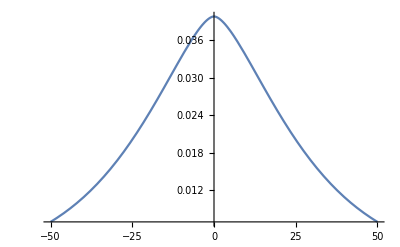

```mathematica
Normal@dsar[
"fs","rk","mu1","d0","ndenefs",
1
/*
(
Plot[
#[x,0],
{x,-50,50}
]&
)
]
```

```mathematica
Normal@dsar[
"fs","rk","mu1","d0","ndenefs",
{"i1","i6"}/*Values
/*
(
Map[
{f[#[0,0]]}&,
#
]
&)
]
```

{{f[0.0398142]},{f[9.13166×10^-12]}}

# Figures

## Direct

## Last change to Fig. 1 - remove it and replace with table (07/22)

```mathematica
dsar[
All
/*
KeyMap[shortenvleg],
"rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
{Max[#],Min[#]}&
],
"d0",
"ndeevs"/*(;;6)
/*
Map[-Abs[QuantityMagnitude[#]]&]
][Transpose][Dataset]
```

Dataset[<>]

## New approach for EVs: Vertical/Horizontal spectrum (07/18)

```mathematica
<|"fs"->"FS","ss"->"SS","hs"->"HS","he"->"HE"|>[[Key["fs"]]]
Dataset[<|"fs"->"FS","ss"->"SS","hs"->"HS","he"->"HE"|>]["fs"]
```

FS

FS

```mathematica
shortenvleg=Dataset[<|"fs"->"FS","ss"->"SS","hs"->"HS","he"->"HE"|>];
spectrumxconv=Dataset[<|"FS"->1,"SS"->2,"HS"->3,"HE"->4|>];
```

```mathematica
randash
randash[[;;,1]]
```

{{RGBColor[0.65, 0., 0.],Dashing[{Large,Tiny,Small}]},{RGBColor[0.212151, 0.39271, 0.8],Dashing[{Large,Medium,Tiny}]},{RGBColor[1, 0.212037, 0.300311],Dashing[{Tiny}]},{RGBColor[0.111025, 0.56, 0.418696],Dashing[{Tiny,Small}]},{RGBColor[0.752461, 0.362306, 0.125339],Dashing[{Large}]},{RGBColor[0.7055434835026511, 0.5895048315002945, 0.],Dashing[{Large}]},{RGBColor[0.0504678, 0.526626, 0.627561],Dashing[{Large,Tiny,Medium}]},{RGBColor[0.435888, 0.259065, 0.71028],Dashing[{Large,Small,Tiny,Medium}]},{RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],Dashing[{Large}]},{RGBColor[0.784922, 0.524612, 0.0407096],Dashing[{Tiny,Small}]},{RGBColor[0.515278, 0.224, 0.530342],Dashing[{Small,Medium,Large}]},{RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278],Dashing[{Large,Small}]}}

{RGBColor[0.65, 0., 0.],RGBColor[0.212151, 0.39271, 0.8],RGBColor[1, 0.212037, 0.300311],RGBColor[0.111025, 0.56, 0.418696],RGBColor[0.752461, 0.362306, 0.125339],RGBColor[0.7055434835026511, 0.5895048315002945, 0.],RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],RGBColor[0.784922, 0.524612, 0.0407096],RGBColor[0.515278, 0.224, 0.530342],RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278]}

Can’t really do spectrum w/ intervals because ranges of higher states overlap..

### Vertical “spectrum”, one plot

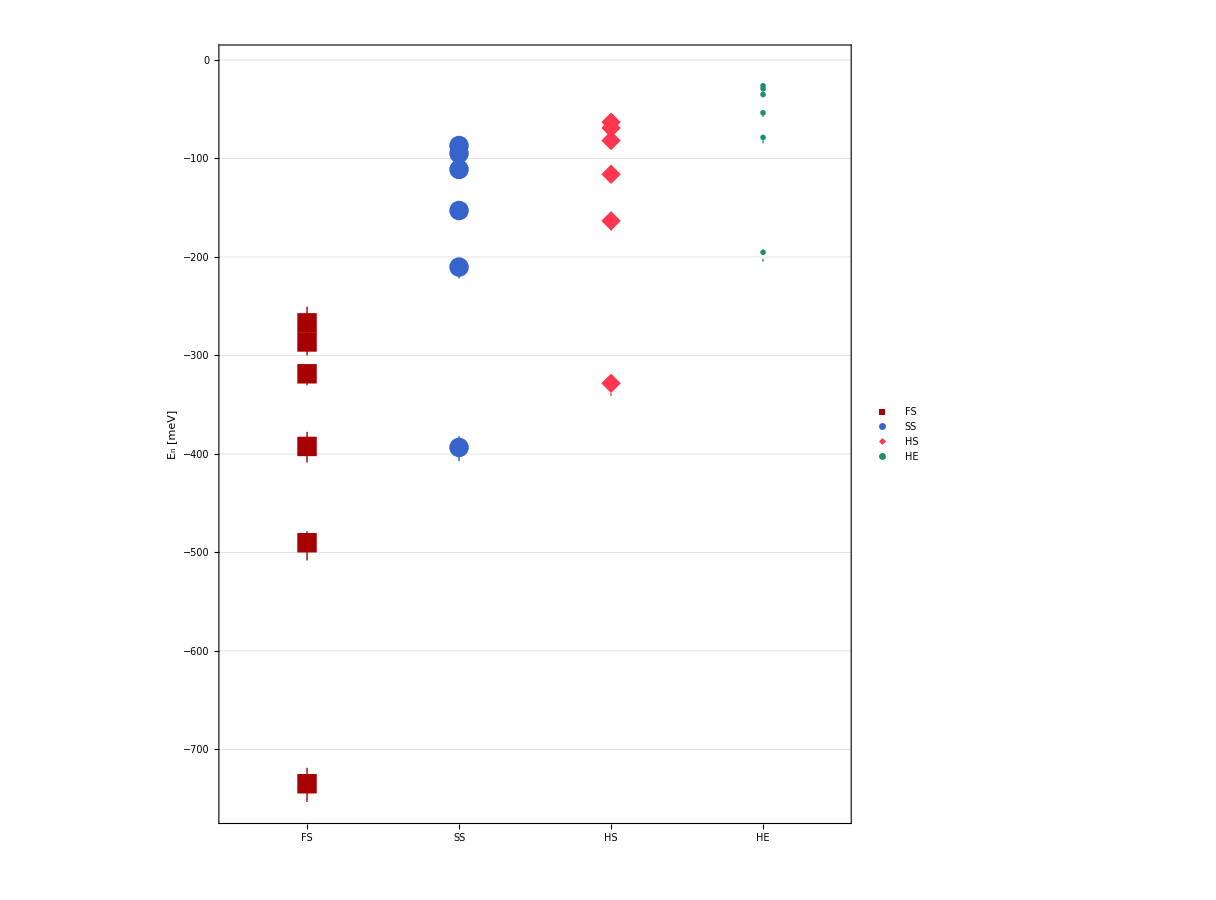
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0722-dir-vert-spectrum.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0722-dir-vert-spectrum.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0722-dir-vert-spectrum.pdf}}
-Graphics-

```mathematica
showandexp["0722-dir-vert-spectrum",#]&@
Normal@dsar[
All
/*
KeyMap[shortenvleg[#]&]
/*
MapIndexed[
With[
{xcoord=First@Normal@spectrumxconv[#2/*Values]},
Map[{xcoord,#}&]@#1
]&
],
"rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&
]
/*
Values,
"d0",
"ndeevs"/*(;;6)
/*
Map[QuantityMagnitude[#]&]
][
(
ListPlot[
#,
PlotTheme->"Detailed",
PlotStyle->randash,
PlotMarkers->Transpose[{feordered,Table[20,{8}]}],
GridLines->{None,Automatic},
GridLinesStyle->Gray,
PlotRange->{{0.5,4.5},{0,-760}},
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{None,None}},
FrameTicks->{{Automatic,None},{{{1,"FS"},{2,"SS"},{3,"HS"},{4,"HE"}},None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Fences",
IntervalMarkersStyle->Thick,
ImageSize->{wx=900,hx=900},
AspectRatio->hx/wx(*,
PlotLegends->Placed[PointLegend[
randash,
Values[envlegabbr],
LegendMarkers->Transpose[{fullmarks4,Table[22,{4}]}],
LegendLayout->{"Row",1}
],Above]*)
]&)
]
```

### Horizontal “Spectrum”, 1 plot

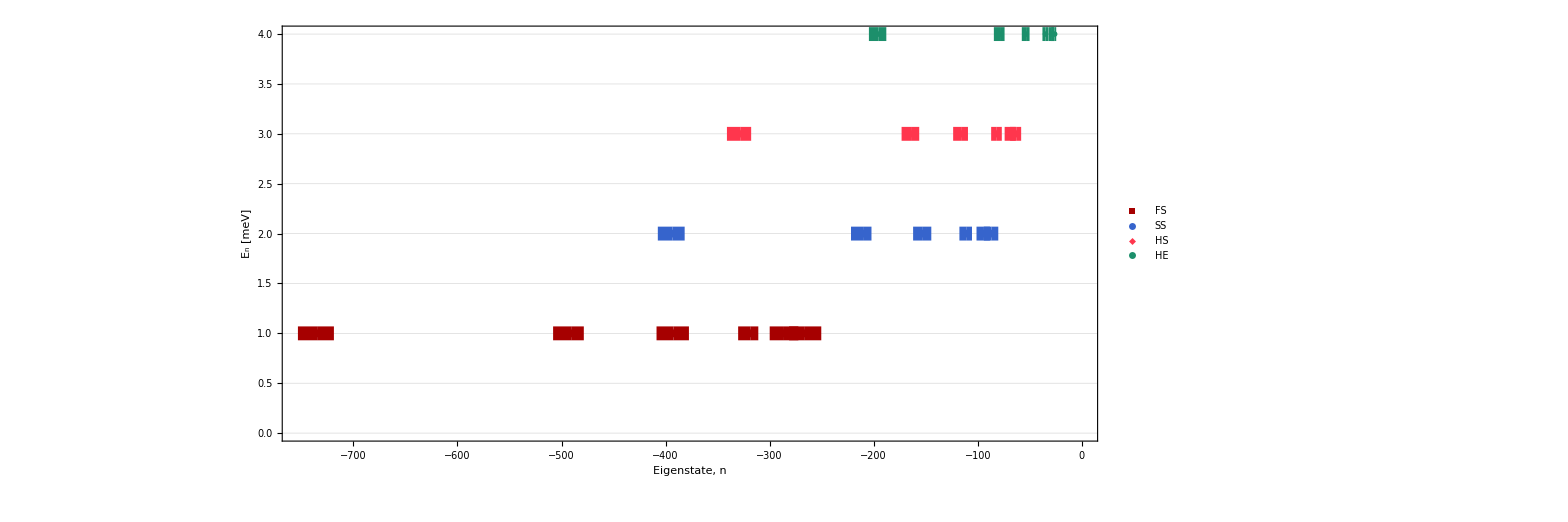

```mathematica
LightMagenta~bg~Normal@dsar[
All
/*
KeyMap[shortenvleg[#]&]
/*
MapIndexed[
With[
{xcoord=First@Normal@spectrumxconv[#2/*Values]},
Map[{#,xcoord}&]@#1
]&
],
"rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&
]
/*
Values,
"d0",
"ndeevs"/*(;;6)
/*
Map[QuantityMagnitude[#]&]
][
(
ListPlot[
#,
PlotTheme->"Detailed",
PlotStyle->randash[[;;,1]],
PlotMarkers->Transpose[{feordered,Table[8,{8}]}],
GridLines->{None,Automatic},
GridLinesStyle->Gray,
PlotRange->Automatic,
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["Eigenstate, n"],None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Bars",
IntervalMarkersStyle->AbsoluteThickness[10](*<|"FenceWidth"->0.1,"WhiskerStyle"->AbsoluteThickness[5],"FenceStyle"->Thick|>*),
ImageSize->{wx=900,hx=300}*2,
AspectRatio->hx/wx
]&)
]
```

### Horizontal “spectrum”, split plots

Export::inselem: There are insufficient elements to export to PDF format.

General::stop: Further output of Export::inselem will be suppressed during this calculation.

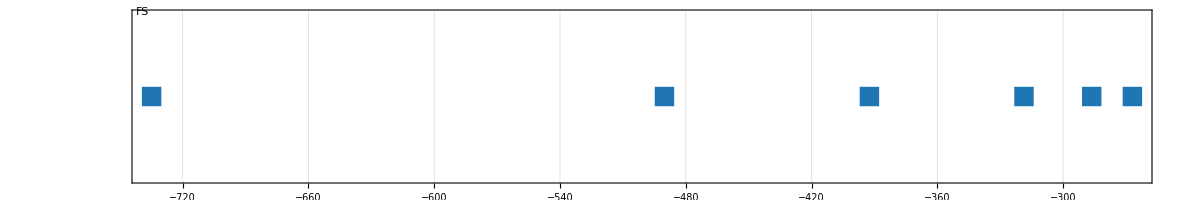
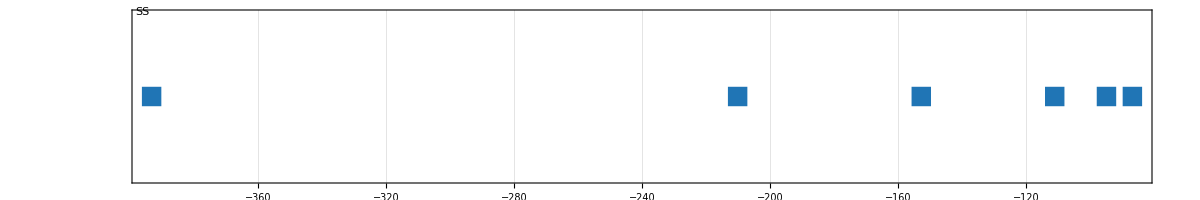
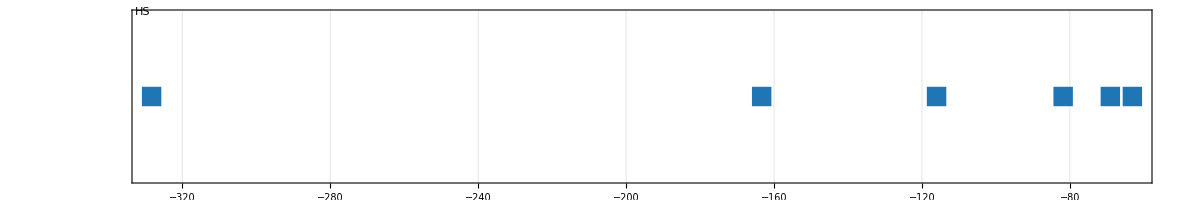
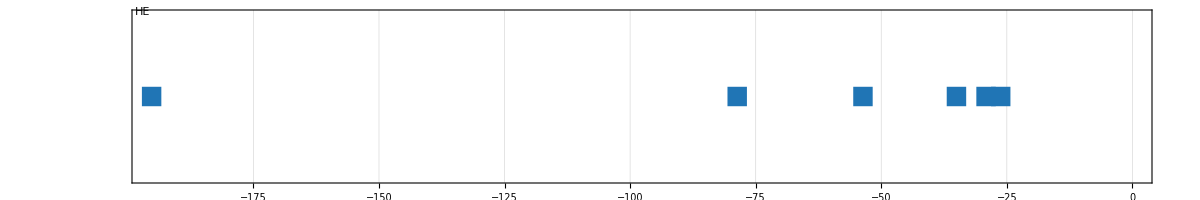
{{{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0722-dir-FS-horiz-indiv-spectrum.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0722-dir-FS-horiz-indiv-spectrum.pdf,$Failed}}
-Graphics-},{{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0722-dir-SS-horiz-indiv-spectrum.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0722-dir-SS-horiz-indiv-spectrum.pdf,$Failed}}
-Graphics-},{{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0722-dir-HS-horiz-indiv-spectrum.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0722-dir-HS-horiz-indiv-spectrum.pdf,$Failed}}
-Graphics-},{{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0722-dir-HE-horiz-indiv-spectrum.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0722-dir-HE-horiz-indiv-spectrum.pdf,$Failed}}
-Graphics-}}

```mathematica
Normal@dsar[
All
/*
KeyMap[shortenvleg[#]&]
/*
MapIndexed[
With[
{xcoord=First@Normal@spectrumxconv[#2/*Values]},
Map[{#,xcoord}&]@#1
]&
],
"rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
(*Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&*)
Mean[#]&
]
/*
Values,
"d0",
"ndeevs"/*(;;6)
/*
Map[QuantityMagnitude[#]&]
][
KeyValueMap[(
<|#1->ListPlot[
#2,
PlotTheme->"Detailed",
FrameTicks->{{None,None},{Automatic,None}},
PlotStyle->randash[[;;,1]],
PlotMarkers->Transpose[{feordered,Table[20,{8}]}],
GridLines->{Automatic,None},
GridLinesStyle->Gray,
PlotRange->Automatic,
FrameLabel->{{None,None},{None,None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Fences",
IntervalMarkersStyle->AbsoluteThickness[5](*<|"FenceWidth"->0.1,"WhiskerStyle"->AbsoluteThickness[5],"FenceStyle"->Thick|>*),
ImageSize->{wx=600,hx=100}*2,
AspectRatio->hx/wx,
PlotLegends->PointLegend[Red,"hi"],
Epilog->{
Inset[
Framed[
Style[#1,22,Black],
Background->White,FrameStyle->None],
Scaled@{0.01,0.99},
Scaled@{0.01,0.99}
]
}
]|>&)]
];
KeyValueMap[showandexp[tssf["0722-dir-`1`-horiz-indiv-spectrum",#1],#2]&]/@%
```

```mathematica
LightPink~bg~Normal@dsar[
All
/*
KeyMap[shortenvleg[#]&]
/*
MapIndexed[
With[
{xcoord=First@Normal@spectrumxconv[#2/*Values]},
Map[{#,xcoord}&]@#1
]&
],
"rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&
]
/*
Values,
"d0",
"ndeevs"/*(;;6)
/*
Map[QuantityMagnitude[#]&]
][
Map[(
ListPlot[
#,
PlotTheme->"Detailed",
FrameTicks->{{None,None},{Automatic,None}},
PlotStyle->randash[[;;,1]],
PlotMarkers->Transpose[{feordered,Table[20,{8}]}],
GridLines->{None,Automatic},
GridLinesStyle->Gray,
PlotRange->Automatic,
FrameLabel->{{None,None},{None,None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Fences",
IntervalMarkersStyle->AbsoluteThickness[5](*<|"FenceWidth"->0.1,"WhiskerStyle"->AbsoluteThickness[5],"FenceStyle"->Thick|>*),
ImageSize->{wx=900,hx=100}*2,
AspectRatio->hx/wx
]&)]
]
```

## EVs w/ error bars (FS values inset)

### Update (7/17): Discrete data points

```mathematica
showandexp["0717-dir-En-allenv-ebars",#]&@
Normal@dsar[
All
/*
KeyMap[envleg]
/*
(
ListPlot[
#[[2;;]],
PlotTheme->"Detailed",
PlotStyle->randash[[2;;,1]],
PlotMarkers->Transpose[{fullmarks4[[2;;]],Table[20,{3}]}],
GridLines->{None,Automatic},
GridLinesStyle->Gray,
PlotRange->{{0.5,6.5},{0,-425}},
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["Eigenstate, n"],None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Fences",
IntervalMarkersStyle->Thick,
ImageSize->{wx=900,hx=900},
AspectRatio->hx/wx,
PlotLegends->Placed[PointLegend[
randash[[;;4,1]],
Values[envlegabbr],
LegendMarkers->Transpose[{fullmarks4,Table[22,{4}]}],
LegendLayout->{"Row",1}
],Above],
Epilog->Inset[Framed[dsar["fs","rk",All/*Transpose/*Map[Values]/*Map[Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&]/*Values/*
(
ListPlot[
#,
PlotTheme->"Detailed",
GridLines->{None,Automatic},
GridLinesStyle->Gray,
PlotStyle->randash[[1,1]],
PlotMarkers->{fullmarks4[[1]],18},
PlotRange->{{0.5,6.5},{-200,-800}},
FrameLabel->None,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
IntervalMarkers->"Fences",
IntervalMarkersStyle->Thick,
ImageSize->{wx=400,hx=250}*1.45,
AspectRatio->hx/wx,
PlotLegends->None
]&),
"d0","ndeevs"/*(;;6)/*Map[-Abs[QuantityMagnitude[#]]&]],
Background->White,FrameStyle->None
],
Scaled[{0.98,0.01}],
Scaled[{0.98,0.01}]
]
]&),
"rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&
]
/*
Values,
"d0",
"ndeevs"/*(;;6)
/*
Map[-Abs[QuantityMagnitude[#]]&]
]
```

MapAt::partw: Part {All,2} of <|fs→FS,ss→SS,hs→HS,he→HE|> does not exist.

{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0717-dir-En-allenv-ebars.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0717-dir-En-allenv-ebars.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0717-dir-En-allenv-ebars.pdf}}
-Graphics-

### Update (6/25): “fences”->”bands”, only show up to n=6

```mathematica
showandexp["0626-dir-En-allenv-ebars",#]&@
Normal@dsar[
All
/*
KeyMap[envleg]
/*
(
ListPlot[
#[[2;;]],
PlotTheme->"Detailed",
PlotStyle->randash[[2;;,1]],
PlotMarkers->Transpose[{fullmarks4[[2;;]],Table[22,{3}]}],
GridLinesStyle->Gray,
PlotRange->{{0.5,6.5},{0,-425}},
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["Eigenstate, n"],None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Bands",
ImageSize->{wx=900,hx=900},
AspectRatio->hx/wx,
PlotLegends->Placed[PointLegend[
randash[[;;4,1]],
Values[envlegabbr],
LegendMarkers->Transpose[{fullmarks4,Table[22,{4}]}],
LegendLayout->{"Row",1}
],Above],
Epilog->Inset[Framed[dsar["fs","rk",All/*Transpose/*Map[Values]/*Map[Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&]/*Values/*
(
ListPlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Gray,
PlotStyle->randash[[1,1]],
PlotMarkers->{fullmarks4[[1]],20},
PlotRange->{{0.5,6.5},{-200,-800}},
FrameLabel->None,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
IntervalMarkers->"Bands",
ImageSize->{wx=400,hx=250}*1.45,
AspectRatio->hx/wx,
PlotLegends->None
]&),
"d0","ndeevs"/*(;;6)/*Map[-Abs[QuantityMagnitude[#]]&]],
Background->White,FrameStyle->None
],
Scaled[{0.98,0.01}],
Scaled[{0.98,0.01}]
]
]&),
"rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&
]
/*
Values,
"d0",
"ndeevs"/*(;;6)
/*
Map[-Abs[QuantityMagnitude[#]]&]
]
```

MapAt::partw: Part {All,2} of <|fs→FS,ss→SS,hs→HS,he→HE|> does not exist.

{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0626-dir-En-allenv-ebars.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0626-dir-En-allenv-ebars.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0626-dir-En-allenv-ebars.pdf}}
-Graphics-

### Show some numbers to help w/ writing & discussion

```mathematica
LightBlue~bg~dsar[
All,
"rk",
All,
"d0",
"ndeevs"
]
```

Dataset[<>]

#### % Diffs b/w μ_i

```mathematica
LightBlue~bg~dsar[
All,
"rk",
All
/*
Transpose
/*
Map[pdiff[Values[#]]&],
"d0",
"ndeevs"
]
```

Dataset[<>]

```mathematica
LightBlue~bg~dsar[
All,
"rk",
{
All
/*
Transpose
/*
Values,
All
/*
Transpose
/*
Map[pdiff[Values[#]]&]
},
"d0",
"ndeevs"
]
```

Dataset[<>]

### Paper figure (6/25)

```mathematica
(*showandexp["dir-En-allenv-ebars",#]&@*)
Normal@dsar[
All
/*
KeyMap[envleg]
/*
(
ListPlot[
#[[2;;]],
PlotTheme->"Detailed",
PlotStyle->randash[[2;;,1]],
PlotMarkers->Transpose[{fullmarks4[[2;;]],Table[22,{3}]}],
GridLinesStyle->Gray,
PlotRange->{{0,13},{0,425}},
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["Eigenstate, n"],None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Fences",
IntervalMarkersStyle->Black,
ImageSize->{wx=900,hx=900},
AspectRatio->hx/wx,
PlotLegends->PointLegend[
randash[[;;4,1]],
Values[envleg],
LegendMarkers->Transpose[{fullmarks4,Table[22,{4}]}]
],
Epilog->Inset[Framed[dsar["fs","rk",All/*Transpose/*Map[Values]/*Map[Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&]/*Values/*
(
ListPlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Gray,
PlotStyle->randash[[1,1]],
PlotMarkers->{fullmarks4[[1]],20},
PlotRange->{{0,13},{0,800}},
FrameLabel->None,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
IntervalMarkers->"Fences",
IntervalMarkersStyle->Black,
ImageSize->{wx=400,hx=300}*1.5,
AspectRatio->hx/wx,
PlotLegends->None
]&),
"d0","ndeevs"/*Map[Abs[QuantityMagnitude[#]]&]],
Background->White,FrameStyle->None
],
Scaled[{0.98,0.98}],
Scaled[{0.98,0.98}]
]
]&),
"rk",
All
/*
Transpose
/*
Map[Values]
/*
Map[
Around[Mean[#],{Mean[#]-Min[#],Max[#]-Mean[#]}]&
]
/*
Values,
"d0",
"ndeevs"
/*
Map[Abs[QuantityMagnitude[#]]&]
]
```

MapAt::partw: Part {All,2} of <|fs→Freestanding,ss→SiO_2 Supported,hs→h-BN Supported,he→h-BN Encapsulated|> does not exist.

-Graphics-

## EF visualization

```mathematica
inumtolett=<|"1"->"a","2"->"b","3"->"c","4"->"d"|>;
muntomua=<|"mu1"->"mua","mu2"->"mub","mu3"->"muc","mu4"->"mud"|>;
entonxny=<|"mu1"-><|"i3"->"(0,2)","i4"->"(0,3)","i5"->"(0,4)","i6"->"(1,0)"|>,"mu3"-><|"i3"->"(0,2)","i4"->"(1,0)","i5"->"(0,3)","i6"->"(0,4)"|>,"mu4"-><|"i3"->"(0,2)","i4"->"(0,3)","i5"->"(1,0)","i6"->"(0,4)"|>|>;
```

#### Pull more than just the ndenefs e.g. ndeevs

```mathematica
Thick
```

```mathematica
AbsoluteTiming[
graphlist=Values@Values@Normal@dsar[
"he",
"rk",
KeyDrop["mu2"]
/*
(
MapIndexed[
Module[{ev=#1[[1]],ef=#1[[2]],mukey=#2[[1]],munum=StringTake[ToString[First[#2[[1]]]],-1],inum=StringTake[ToString[First[#2[[2]]]],-1],ikey=#2[[2]],wx=800,hx=450},
(*{f[ev],g[ef],h[keys]}*)
Plot[
{ef[x,0],ef[x,-10],ef[x,10],ef[0,x],ef[-10,x],ef[10,x]},
{x,-500,500},
PlotTheme->"Detailed",
PlotStyle->{Directive[Red,Thick],Directive[Red,Dashed,Thick],Directive[Red,DotDashed,Thick],Directive[Blue,Thin],Directive[Blue,Dashed,Thin],Directive[Blue,DotDashed,Thin]},
ImageSize->{wx,hx},
AspectRatio->hx/wx,
Axes->True,
AxesOrigin->{0,0},
AxesStyle->{Black,Thick},
PlotRange->All, 
FrameTicks->None,
FrameLabel->None,
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
PlotLegends->None,
Epilog->{
Inset[
Framed[
Style[
TraditionalForm[tssf[
"μ_(`2`); `1` → `3`",
inum,
inumtolett[munum],
entonxny[First@mukey,First@ikey]
]],
Black,22,FontFamily->"Arial"
],
Background->White,
RoundingRadius->5
],
Scaled[{0.98,0.02}],
Scaled[{0.98,0.02}]
],
Inset[
Framed[
Style[
TraditionalForm[tssf[
"E_(`1`) = `2` meV",
inum,
NumberForm[Abs@QuantityMagnitude@ev,4]
]],
Black,22,FontFamily->"Arial"
],
Background->White,
RoundingRadius->5
],
Scaled[{0.98,0.98}],
Scaled[{0.98,0.98}]
]
}
]]&,
#,
{2}
]&)
,
"d0",
{
"ndeevs"/*(3;;6),
"ndenefs"/*(3;;6)
}
/*
Transpose
];
]
```

{588.264,Null}

```mathematica
??showandexp
```

```mathematica
??combopltexp
```

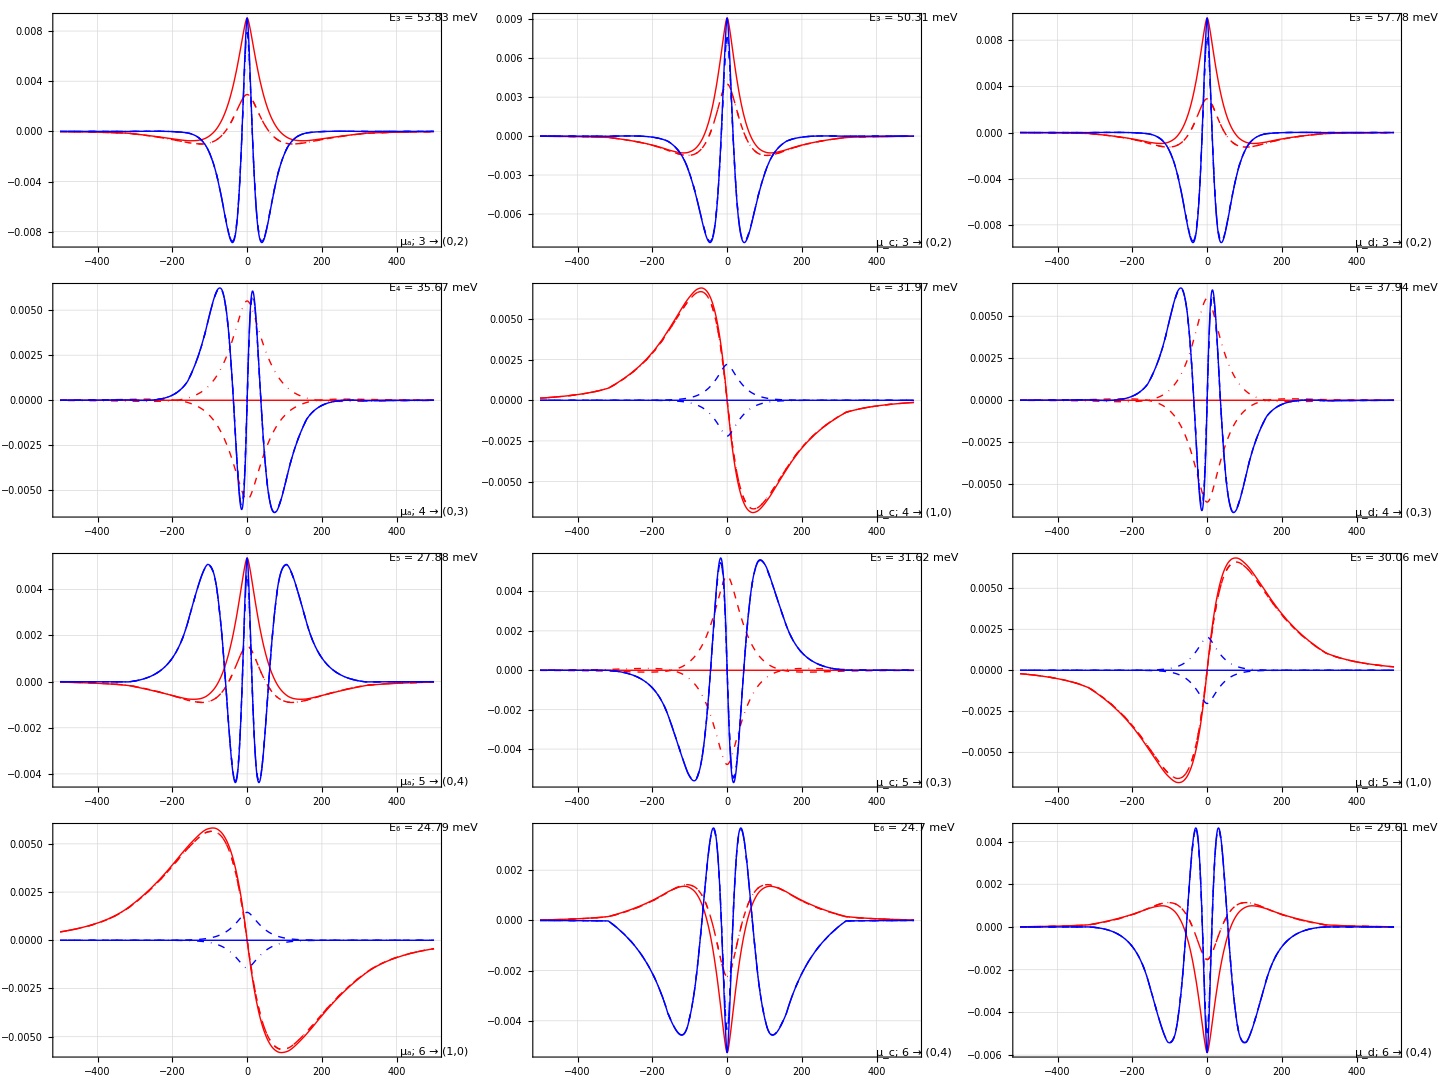

```mathematica
GraphicsGrid[
graphlist//Transpose,
Spacings->{sx=0,sy=0},
ImageSize->{2400+2*sx,1800+3*sy}*0.60
]
```

```mathematica
dfd
```

~/datadrop/Dropbox/Berman-Research/dis/figs/

```mathematica
Export[dfd<>"phos-plt-grid-0724-dir-nefs-i3to6-muacd.pdf",
GraphicsGrid[
graphlist//Transpose,
Spacings->{sx=0,sy=0},
ImageSize->{2400+2*sx,1800+3*sy}*0.60
]
]
```

~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-grid-0724-dir-nefs-i3to6-muacd.pdf

```mathematica
Export[dfd<>"phos-plt-grid-0724-dir-nefs-i3to6-muacd.eps",
GraphicsGrid[
graphlist//Transpose,
Spacings->{sx=0,sy=0},
ImageSize->{2400+2*sx,1800+3*sy}*0.60
]
]
```

~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-grid-0724-dir-nefs-i3to6-muacd.eps

### I feel like I’m taking a roundabout route to what I want.

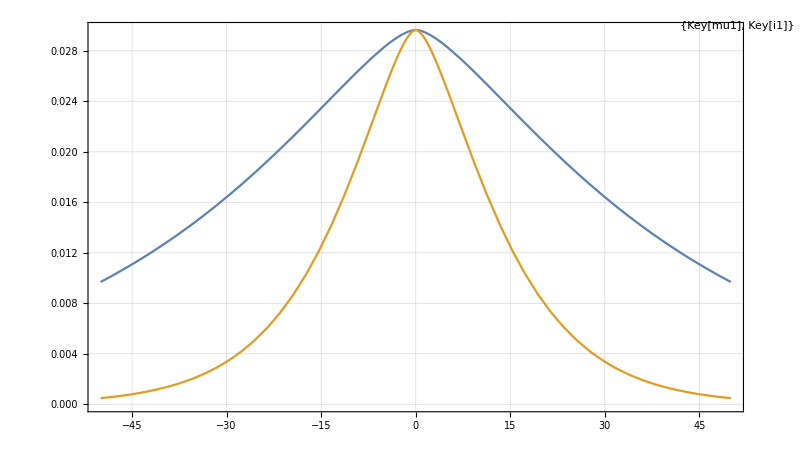
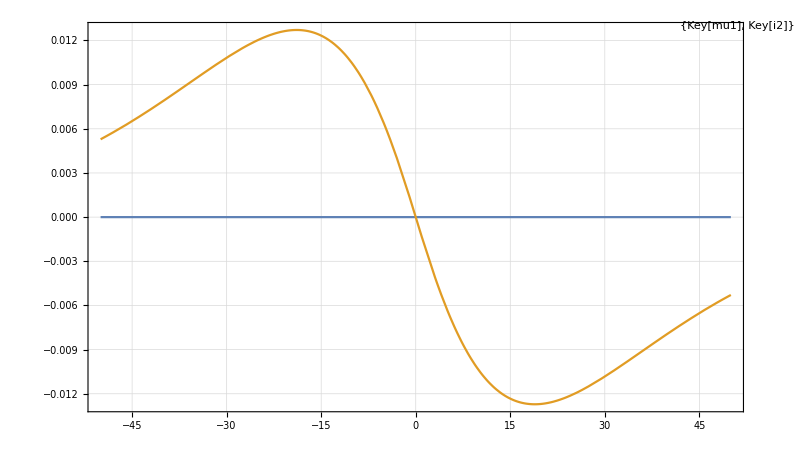
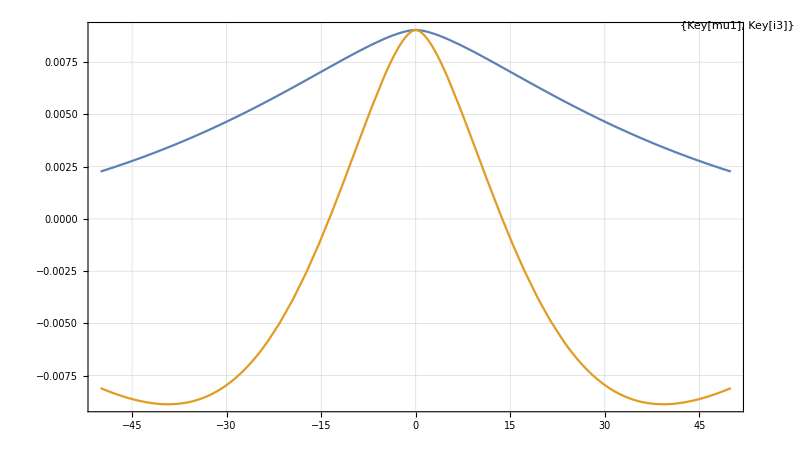
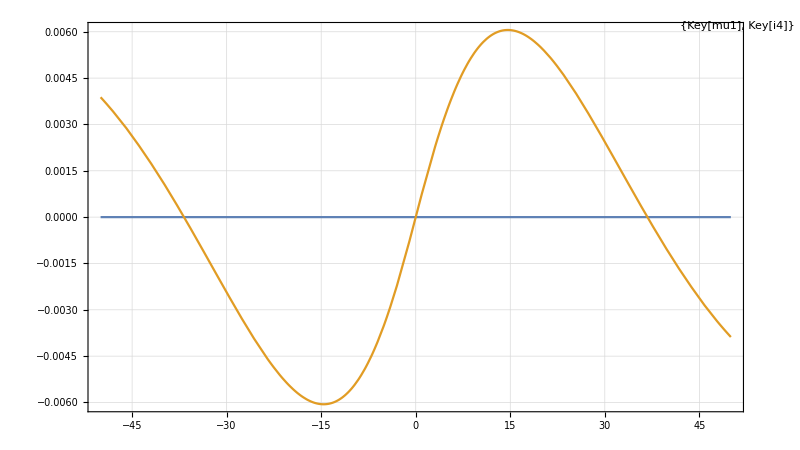
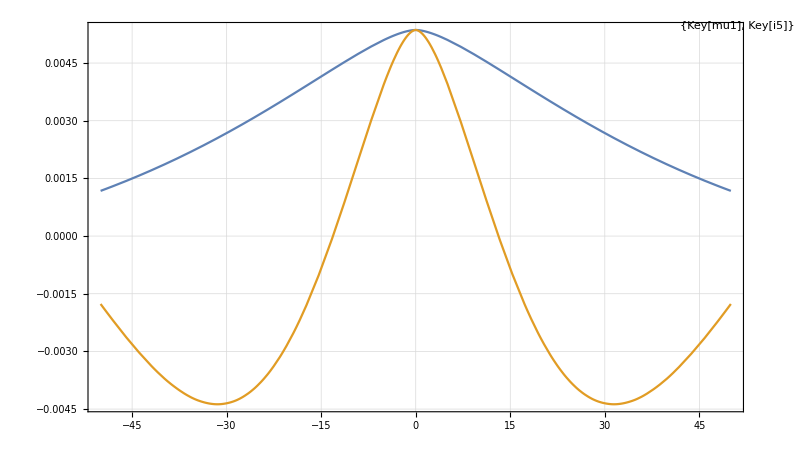
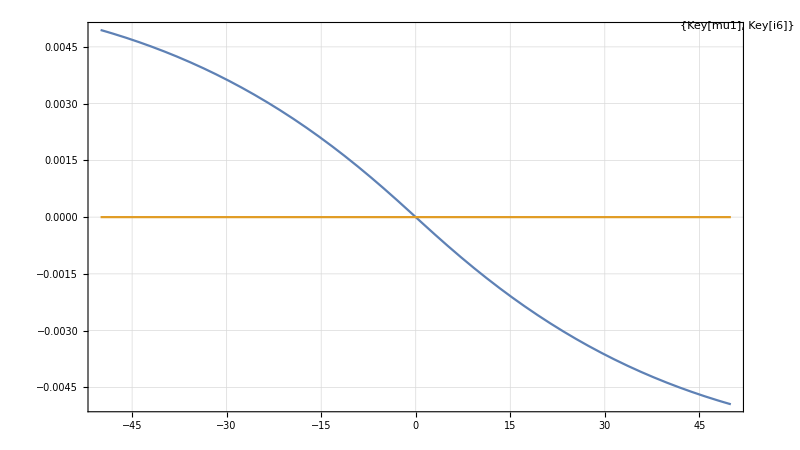
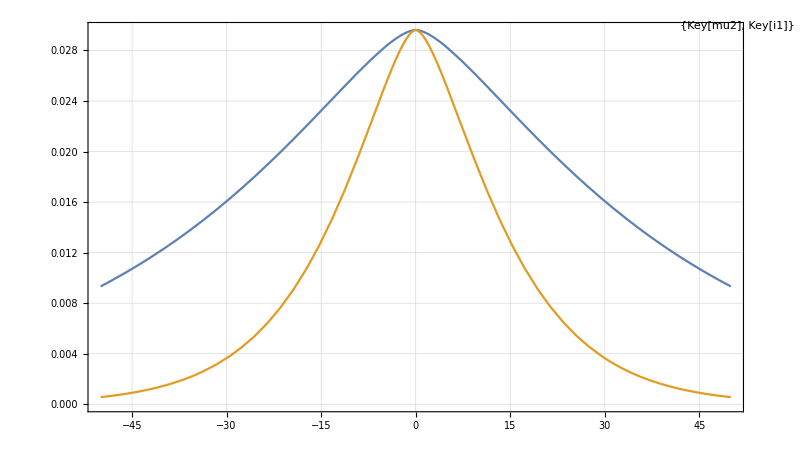
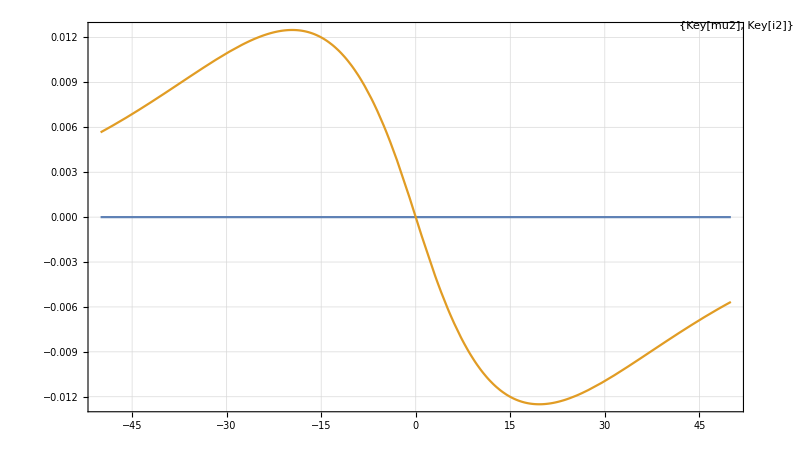
{165.091,<|mu1→<|i1→{5.89723,-Graphics-},i2→{6.37776,-Graphics-},i3→{9.08953,-Graphics-},i4→{5.98976,-Graphics-},i5→{8.9431,-Graphics-},i6→{5.10937,-Graphics-}|>,mu2→<|i1→{5.59241,-Graphics-},i2→{6.56701,-Graphics-},i3→{9.01866,-Graphics-},i4→{5.99736,-Graphics-},i5→{9.01751,-Graphics-},i6→{5.56729,-Graphics-}|>,mu3→<|i1→{4.22212,-Graphics-},i2→{6.50481,-Graphics-},i3→{8.26344,-Graphics-},i4→{5.24042,-Graphics-},i5→{6.12313,-Graphics-},i6→{8.93757,-Graphics-}|>,mu4→<|i1→{6.14008,-Graphics-},i2→{6.19788,-Graphics-},i3→{9.24634,-Graphics-},i4→{6.14863,-Graphics-},i5→{5.99264,-Graphics-},i6→{8.89911,-Graphics-}|>|>}

```mathematica
AbsoluteTiming@Normal@dsar["he","rk",
All
/*
(
MapIndexed[
Module[{keys=#2,ef=#1,wx=800,hx=450},
AbsoluteTiming[Plot[
{ef[x,0],ef[0,x]},
{x,-50,50},
PlotTheme->"Detailed",
ImageSize->{wx,hx},
AspectRatio->hx/wx,
Axes->True,
AxesOrigin->{0,0},
FrameTicks->None,
PlotLegends->None,
Epilog->{
Inset[
Framed[
Style[
tssf["`1`",keys],18,Black,FontFamily->"Arial"
],
Background->White,FrameStyle->None
],
Scaled@{0.99,0.99},
Scaled@{0.99,0.99}
]
}
]]]&,
#,
{2}
]&)
,"d0","ndenefs"/*(;;6)]
```

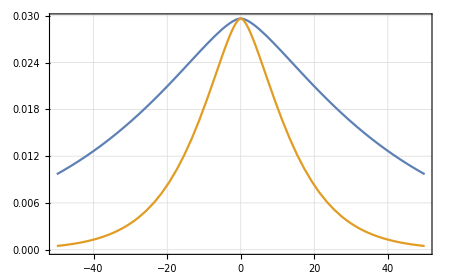
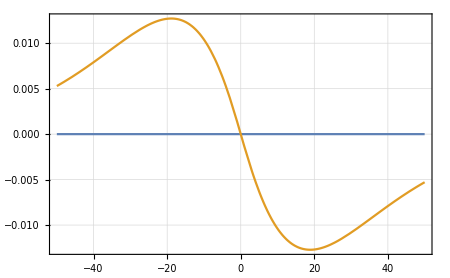
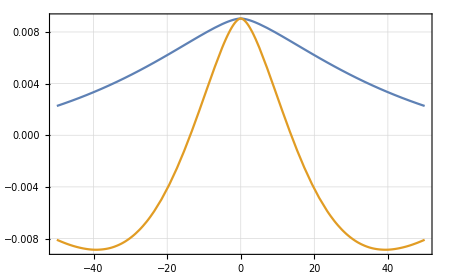
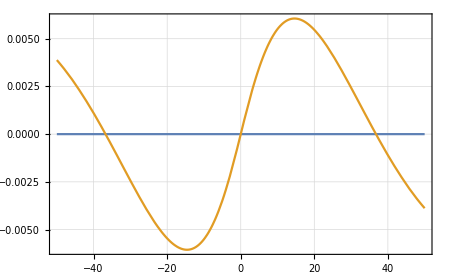
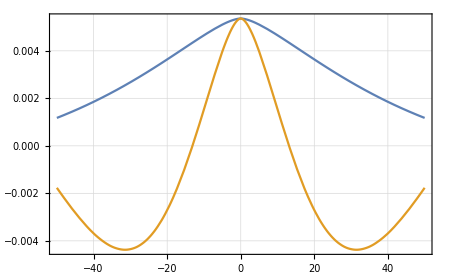
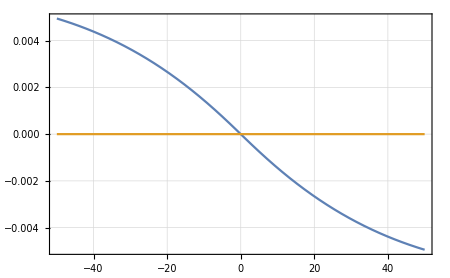
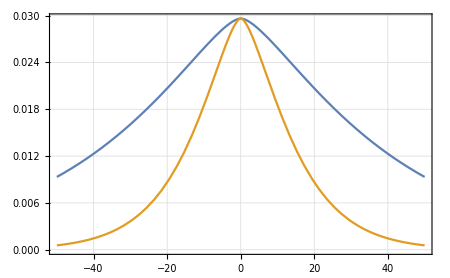
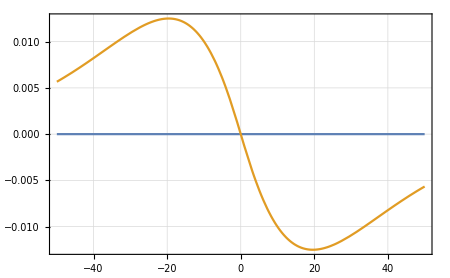
{387.541,<|mu1→<|i1→{5.92026,-Graphics-},i2→{6.41363,-Graphics-},i3→{9.1398,-Graphics-},i4→{6.23088,-Graphics-},i5→{8.93827,-Graphics-},i6→{5.16872,-Graphics-}|>,mu2→<|i1→{6.88124,-Graphics-},i2→{7.33099,-Graphics-},i3→{10.1105,-Graphics-},i4→{6.47567,-Graphics-},i5→{9.50523,-Graphics-},i6→{5.90067,-Graphics-}|>,mu3→<|i1→{6.27676,-Graphics-},i2→{9.71842,-Graphics-},i3→{12.0456,-Graphics-},i4→{5.59384,-Graphics-},i5→{6.44446,-Graphics-},i6→{9.30052,-Graphics-}|>,mu4→<|i1→{6.35205,-Graphics-},i2→{6.66458,-Graphics-},i3→{9.91501,-Graphics-},i4→{6.61029,-Graphics-},i5→{6.77174,-Graphics-},i6→{9.57374,-Graphics-}|>|>}

```mathematica
AbsoluteTiming@Normal@dsar["he","rk",All,"d0","ndenefs"/*(;;6),
Map[
AbsoluteTiming[Plot[
{#[x,0],#[0,x]},
{x,-50,50},
PlotTheme->"Detailed",
ImageSize->{450,450},
Axes->True,
AxesOrigin->{0,0},
FrameTicks->None,
PlotLegends->None
]]&
]
]
```

```mathematica
dsar["he","rk",All,"d0","ndenefs"/*(;;6),
Map[
AbsoluteTiming[Plot[
{#[x,0],#[0,x]},
{x,-50,50},
PlotTheme->"Detailed",
ImageSize->{450,450},
Axes->True,
AxesOrigin->{0,0},
PlotLegends->None
]]&
]
]//AbsoluteTiming
```

{382.484,Dataset[<>]}

### Why does this damn function keep BREAKING?

```mathematica
Dataset[<|Table[
tssf["`1`",muntomua[mukey]]->Normal@dsar["he","rk",mukey,"d0","ndenefs",
(;;6)/*Map[
Plot[
{#[x,0],#[0,x]},
{x,-50,50},
PlotTheme->"Detailed",
ImageSize->{450,450},
Axes->True,
AxesOrigin->{0,0}
]&
]
],
{mukey,{"mu1","mu2","mu3","mu4"}}
]|>]
```

Dataset[<>]

### Paper figure (UPDATE 07/23)

```mathematica
Table[
MapIndexed[
(*showandexp[tssf["0723-dir-nef-i`1`-`2`",First[#2],mukey],#1]&*)
{f[#1],g[#2]}&,
Values@Normal@dsar["he","rk",mukey,"d0","ndenefs",
All
/*
(
MapIndexed[
Module[{data=#1,key=First[#2][[1]],keynum=(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])[[1]]},
Plot[
Evaluate[Flatten@Transpose@Table[{data[x,x0],data[x0,x]},{x0,{0,-10,10}}]],
{
x,
(-100-(50*keynum)),
(100+(50*keynum))
},
PlotTheme->"Detailed",
PlotStyle->{Directive[Red,Thick],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue,Thick],Directive[Blue,Dashed],Directive[Blue,Dotted]},
ImageSize->{wx=500,hx=250},
AspectRatio->hx/wx,
AxesOrigin->{0,0},
Axes->True,
AxesStyle->{Black,Thick},
PlotRange->All,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
FrameTicks->None,FrameLabel->None,
Epilog->{
Inset[
Framed[
Style[TraditionalForm[tssf["μ_(`2`);n=`1`",keynum,inumtolett[StringTake[mukey,-1]]]],Black,18,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.95}],
Scaled[{0.95,0.95}]
],
Inset[
Framed[
Style[TraditionalForm[tssf["E_(`1`) = `2` meV",keynum,NumberForm[dsar["he","rk",mukey,"d0","ndeevs",keynum/*QuantityMagnitude/*Abs],4]]],Black,18,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.05}],
Scaled[{0.95,0.05}]
]
},
PlotLegends->Placed[
LineLegend[
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ_(`4`)(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0,keynum]],20,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2}
],
Above
]
]
]&,
#
]&)
]
],
{mukey,{"mu1","mu2","mu3","mu4"}}
]
```

Values::invrl: The argument … is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

{Values[{f[Failure[…]],g[{1}]}],Values[{f[Failure[…]],g[{1}]}],Values[{f[Failure[…]],g[{1}]}],Values[{f[Failure[…]],g[{1}]}]}

### Paper figure (6/25)

```mathematica
Table[
MapIndexed[
showandexp[tssf["dir-nef-i`1`-`2`",First[#2],mukey],#1]&,
Values@Normal@dsar["he","rk",mukey,"d0","ndenefs",
All
/*
(
MapIndexed[
Module[{data=#1,key=First[#2][[1]],keynum=(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])[[1]]},
Plot[
Evaluate[Flatten@Transpose@Table[{data[x,x0],data[x0,x]},{x0,{0,-10,10}}]],
{
x,
(-100-(50*keynum)),
(100+(50*keynum))
},
PlotTheme->"Detailed",
PlotStyle->{Directive[Red,Thick],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue,Thick],Directive[Blue,Dashed],Directive[Blue,Dotted]},
ImageSize->{wx=500,hx=250},
AspectRatio->hx/wx,
AxesOrigin->{0,0},
Axes->True,
AxesStyle->{Black,Thick},
PlotRange->All,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
FrameTicks->None,FrameLabel->None,
Epilog->{
Inset[
Framed[
Style[TraditionalForm[tssf["μ_(`2`);n=`1`",keynum,StringTake[mukey,-1]]],Black,18,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.95}],
Scaled[{0.95,0.95}]
],
Inset[
Framed[
Style[TraditionalForm[tssf["E_(`1`) = `2` meV",keynum,NumberForm[dsar["he","rk",mukey,"d0","ndeevs",keynum/*QuantityMagnitude/*Abs],4]]],Black,18,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.05}],
Scaled[{0.95,0.05}]
]
},
PlotLegends->Placed[
LineLegend[
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ_(`4`)(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0,keynum]],20,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2}
],
Above
]
]
]&,
#
]&)
]
],
{mukey,{"mu1","mu2","mu3","mu4"}}
]
```

### Standalone legend

```mathematica
LineLegend[
{Directive[Red,Thick],Directive[Red,Dashed,Thick],Directive[Red,DotDashed,Thick],Directive[Blue,Thin],Directive[Blue,Dashed,Thin],Directive[Blue,DotDashed,Thin]},
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0]],18,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2},
LegendFunction->(Framed[#1, FrameMargins->0, RoundingRadius->5] & )
]
{Export[dfd<>"leg-general-efs-xy-slice.pdf",%,"PDF"],Export[dfd<>"leg-general-efs-xy-slice.eps",%,"EPS"]}
```

{~/datadrop/Dropbox/Berman-Research/dis/figs/leg-general-efs-xy-slice.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/leg-general-efs-xy-slice.eps}

### Just the graphs (for viewing w/in MMA)

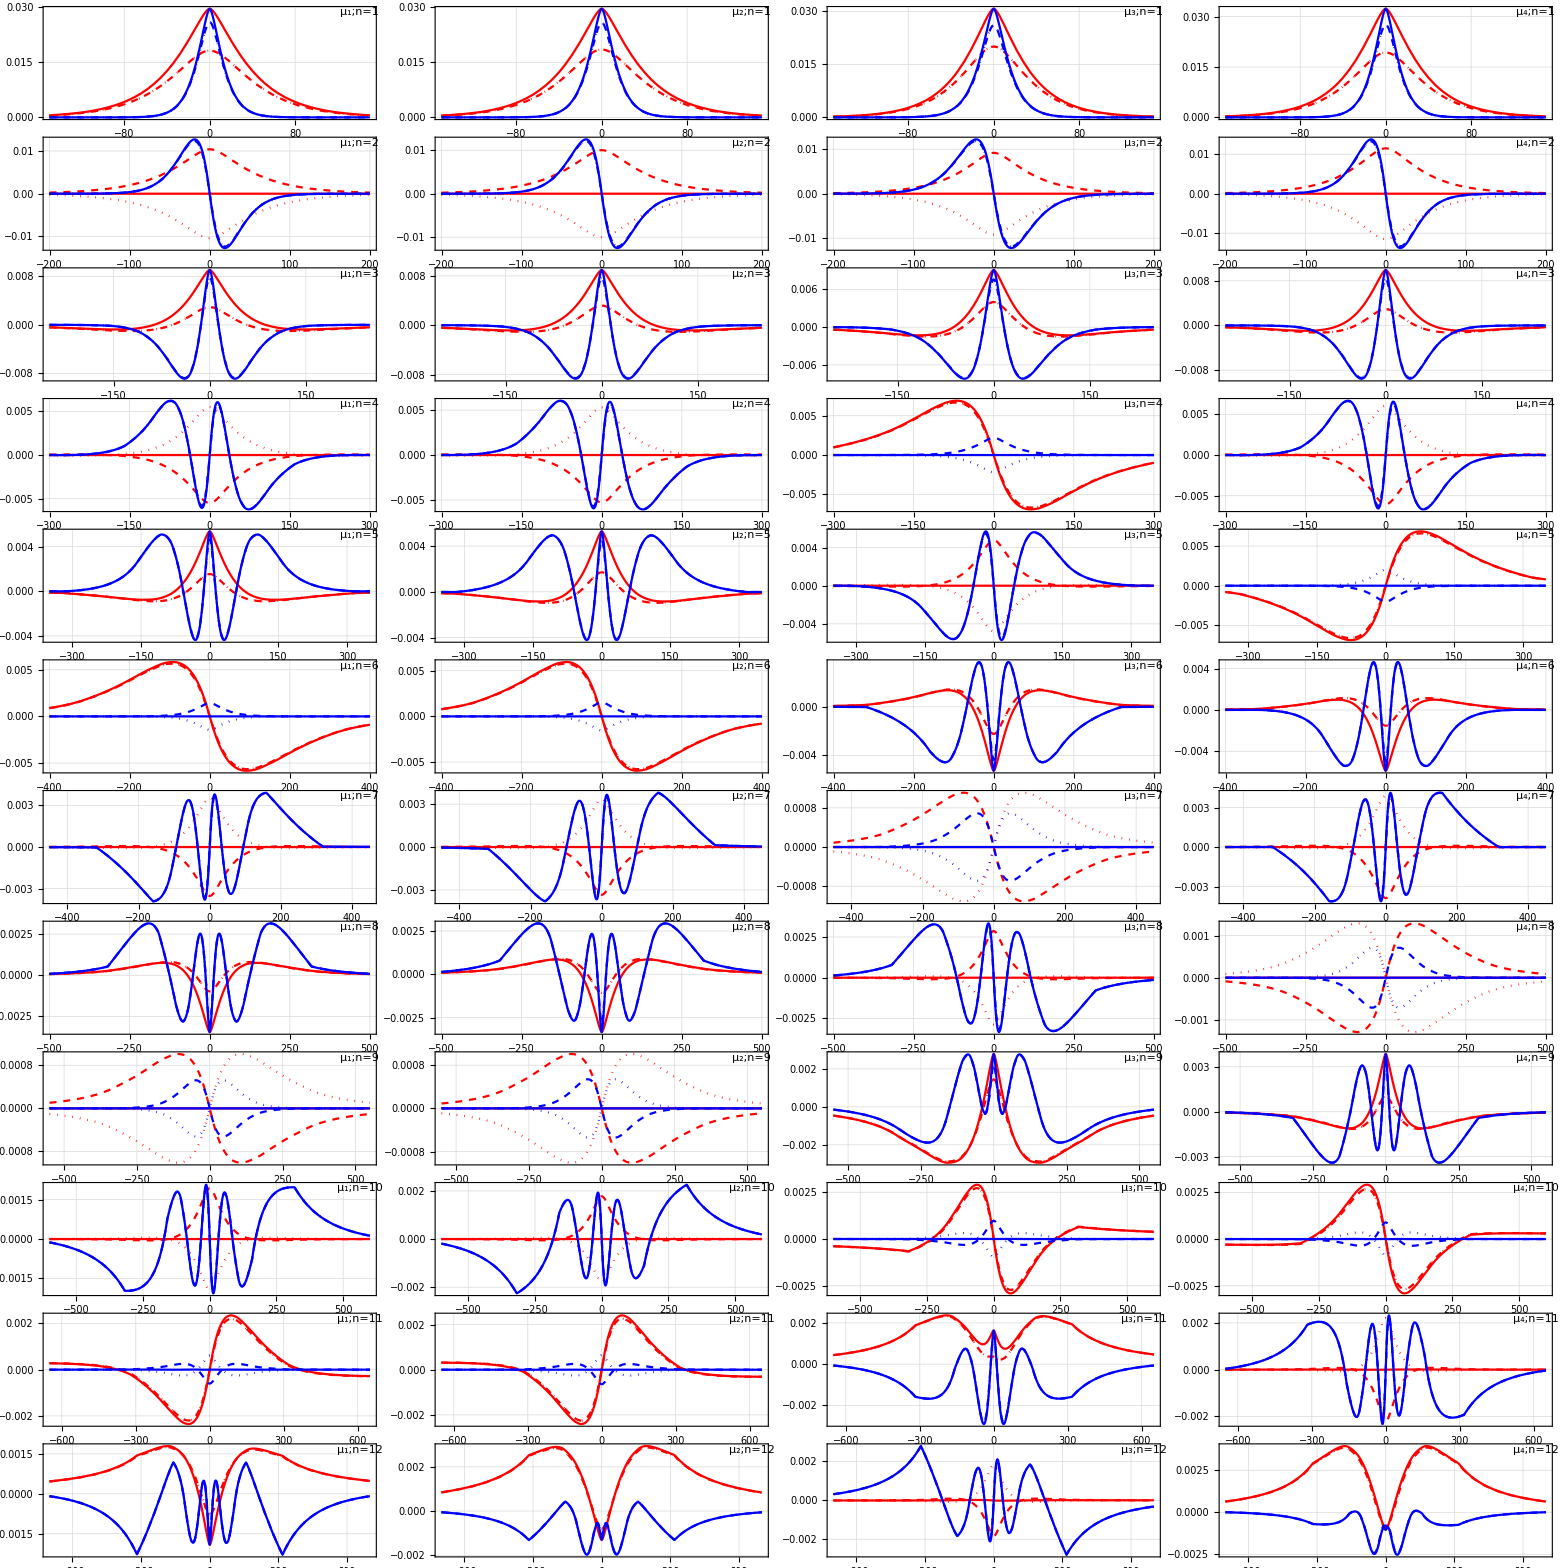

```mathematica
Table[
(Values@Normal@dsar["he","rk",mukey,"d0","ndenefs",
All
/*
(
MapIndexed[
Module[{data=#1,key=First[#2][[1]],keynum=(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])[[1]]},
Plot[
Evaluate[Flatten@Transpose@Table[{data[x,x0],data[x0,x]},{x0,{0,-10,10}}]],
{
x,
(-100-(50*keynum)),
(100+(50*keynum))
},
PlotTheme->"Detailed",
PlotStyle->{Directive[Red],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue],Directive[Blue,Dashed],Directive[Blue,Dotted]},
ImageSize->{wx=500,hx=250}*0.5,
AspectRatio->hx/wx,
AxesOrigin->{0,0},
Axes->True,
AxesStyle->{Black,Thick},
PlotRange->Full,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
(*FrameLabel->{{tssf["ψ_(`1`)(x,y)",keynum],None},{"x,y",None}},*)
FrameTicks->None,FrameLabel->None,
Epilog->{
Inset[
Framed[
Style[TraditionalForm[tssf["μ_(`2`);n=`1`",keynum,StringTake[mukey,-1]]],Black,20,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.95}],
Scaled[{0.95,0.95}]
]
},
PlotLegends->Placed[
LineLegend[
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ_(`4`)(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0,keynum]],20,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2}
],
Above
]
]
]&,
#
]&)
])[[;;,1]],
{mukey,{"mu1","mu2","mu3","mu4"}}
]//Transpose//TableForm
```

WTF... sometimes this works, sometimes it doesn’t...

```mathematica
Table[
(Values@Normal@dsar["he","rk",mukey,"d0","ndenefs",
All
/*
(
MapIndexed[
Module[{data=#1,key=First[#2][[1]],keynum=(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])[[1]]},
Plot[
Evaluate[Flatten@Transpose@Table[{data[x,x0],data[x0,x]},{x0,{0,-10,10}}]],
{
x,
(-100-(50*keynum)),
(100+(50*keynum))
},
PlotTheme->"Detailed",
PlotStyle->{Directive[Red],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue],Directive[Blue,Dashed],Directive[Blue,Dotted]},
ImageSize->{wx=500,hx=250}*0.5,
AspectRatio->hx/wx,
AxesOrigin->{0,0},
Axes->True,
AxesStyle->{Black,Thick},
PlotRange->Full,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
(*FrameLabel->{{tssf["ψ_(`1`)(x,y)",keynum],None},{"x,y",None}},*)
FrameTicks->None,FrameLabel->None,
Epilog->{
Inset[
Framed[
Style[TraditionalForm[tssf["μ_(`2`);n=`1`",keynum,StringTake[mukey,-1]]],Black,20,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.95}],
Scaled[{0.95,0.95}]
]
},
PlotLegends->Placed[
LineLegend[
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ_(`4`)(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0,keynum]],20,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2}
],
Above
]
]
]&,
#
]&)
])[[;;,1]],
{mukey,{"mu1","mu2","mu3","mu4"}}
]//Transpose//TableForm
```

Values::invrl: The argument … is not a valid Association or a list of rules.

Part::partd: Part specification … is longer than depth of object.

Values::invrl: The argument … is not a valid Association or a list of rules.

Part::partd: Part specification … is longer than depth of object.

Values::invrl: The argument … is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose[{Values[Failure[…]]⟦1;;All,1⟧,Values[Failure[…]]⟦1;;All,1⟧,Values[Failure[…]]⟦1;;All,1⟧,Values[Failure[…]]⟦1;;All,1⟧}]

## Array plot of allowed transitions

### Change from black to gray squares

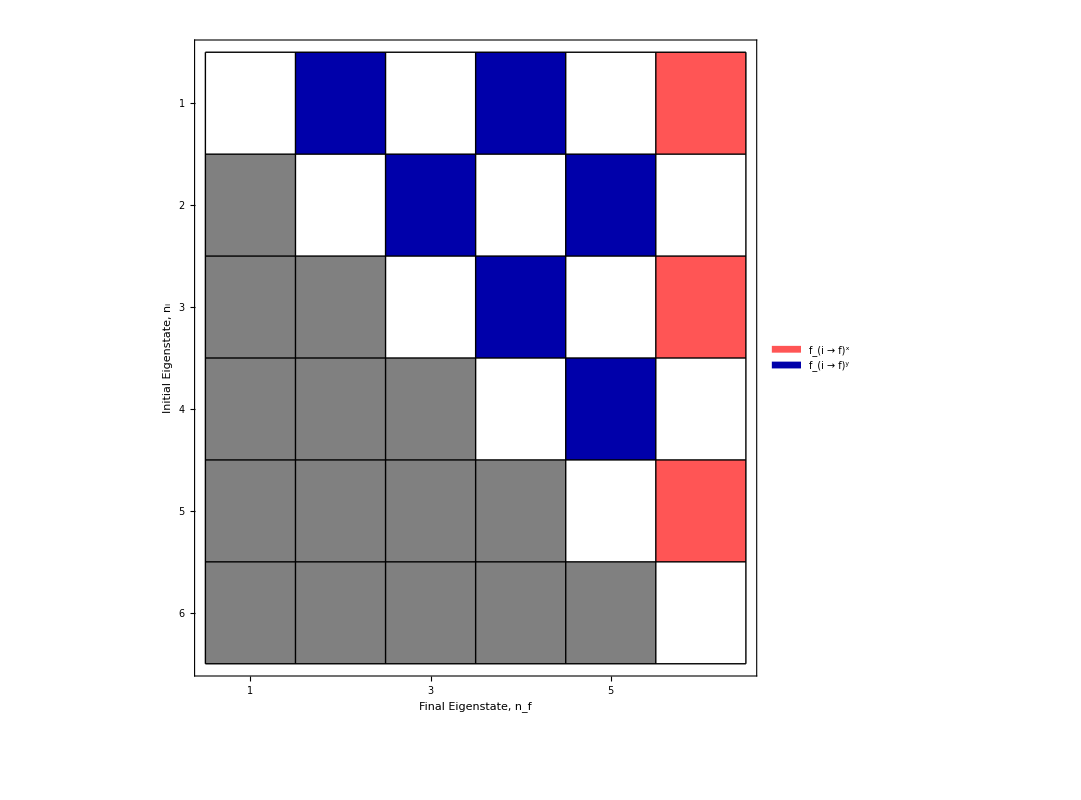

~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0725-dir-foxy-arrplt.pdf

```mathematica
ArrayPlot[
Chop[PadLeft[Subtract@@(nvv[dsar["he","rk","mu1","d0",#]]&/@{"fox","foy"}),{12,12},"-"],10^-5],
PlotTheme->"Detailed",
ColorRules->{"-"->Gray,0->White,x_/;x>0->Lighter@Red,x_/;x<0->Darker@Blue},
PlotLegends->Placed[SwatchLegend[
{Lighter@Red,Darker@Blue},
{"f_(i → f)^x","f_(i → f)^y"},
LegendMarkerSize->30,
LabelStyle->{Black,30,FontFamily->"Arial"},
LegendFunction->(Framed[#,RoundingRadius->5]&)
],
Above
],
ImageSize->{800,800},
PlotRange->{{1,6},{1,6}},
Mesh->True,
MeshStyle->Black,
DataReversed->{False,False},
Frame->True,
FrameTicks->{#,#,#,#}&@Table[i,{i,12}],
LabelStyle->labsty,
FrameLabel->{{"Final Eigenstate, n_f",None},{"Initial Eigenstate, n_i",None}}
]
Export[dfd<>"phos-comb-0725-dir-foxy-arrplt.pdf",%,"PDF"]
```

### Experimenting 07/23?

```mathematica
LightOrange~bg~dsar[All,"rk",All,"d0","fox"/*(Map[ScientificForm[#,3]&,#,{-1}]&)]
LightMagenta~bg~dsar[All,"rk",All,"d0","foy"/*Map[ScientificForm[#,3]&]]
```

Dataset[<>]

Dataset[<>]

### Replace 12x12 grid w/ 6x6 grid (DONE 6/26)

TODO: SWITCH FROM 12 TO 6

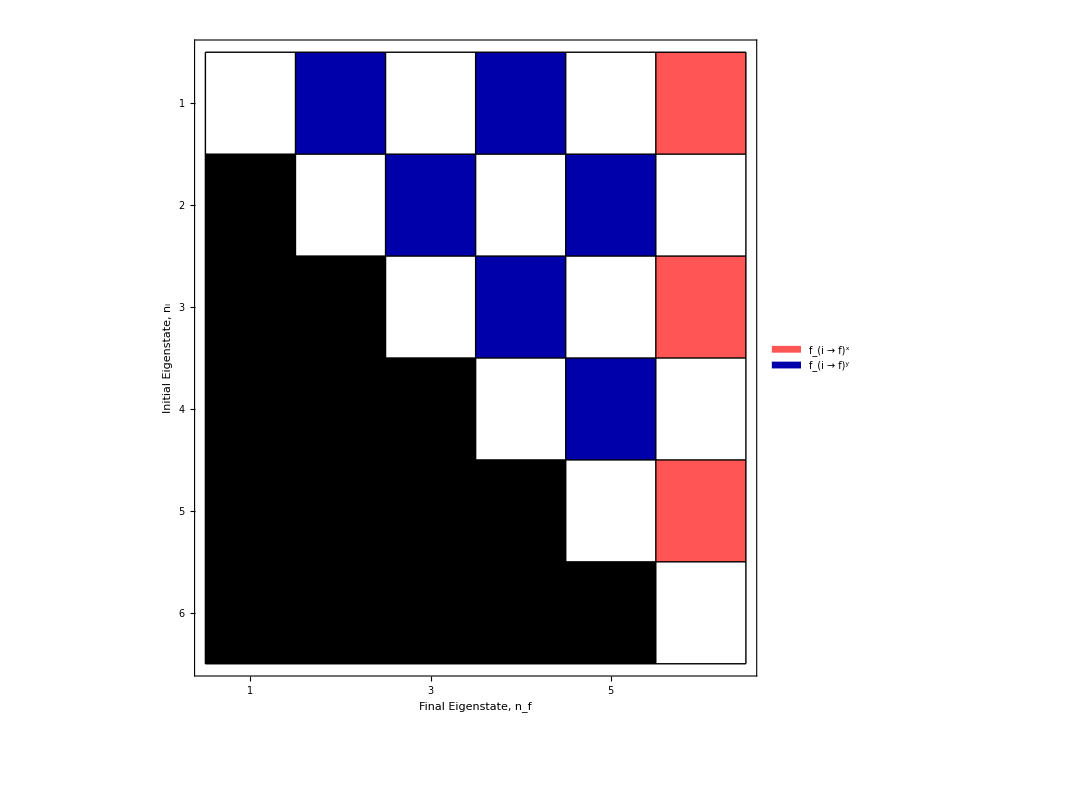

~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0626-dir-foxy-arrplt.pdf

```mathematica
ArrayPlot[
Chop[PadLeft[Subtract@@(nvv[dsar["he","rk","mu1","d0",#]]&/@{"fox","foy"}),{12,12},"-"],10^-5],
PlotTheme->"Detailed",
ColorRules->{"-"->Black,0->White,x_/;x>0->Lighter@Red,x_/;x<0->Darker@Blue},
PlotLegends->Placed[SwatchLegend[
{Lighter@Red,Darker@Blue},
{"f_(i → f)^x","f_(i → f)^y"},
LegendMarkerSize->30,
LabelStyle->{Black,30,FontFamily->"Arial"},
LegendFunction->(Framed[#,RoundingRadius->5]&)
],
Above
],
ImageSize->{800,800},
PlotRange->{{1,6},{1,6}},
Mesh->True,
MeshStyle->Black,
DataReversed->{False,False},
Frame->True,
FrameTicks->{#,#,#,#}&@Table[i,{i,12}],
LabelStyle->labsty,
FrameLabel->{{"Final Eigenstate, n_f",None},{"Initial Eigenstate, n_i",None}}
]
Export[dfd<>"phos-comb-0626-dir-foxy-arrplt.pdf",%,"PDF"]
```

### Paper figure (6/25) (all 12 n)

```mathematica
ArrayPlot[
Chop[PadLeft[Subtract@@(nvv[dsar["he","rk","mu1","d0",#]]&/@{"fox","foy"}),{12,12},"-"],10^-5],
PlotTheme->"Detailed",
ColorRules->{"-"->Black,0->White,x_/;x>0->Lighter@Red,x_/;x<0->Darker@Blue},
PlotLegends->Placed[SwatchLegend[
{Lighter@Red,Darker@Blue},
{"f_(i → f)^x","f_(i → f)^y"},
LegendMarkerSize->30,
LabelStyle->{Black,30,FontFamily->"Arial"},
LegendFunction->(Framed[#,RoundingRadius->5]&)
],
Above
],
ImageSize->{800,800},
Mesh->True,
MeshStyle->Black,
DataReversed->{False,False},
Frame->True,
FrameTicks->{#,#,#,#}&@Table[i,{i,12}],
LabelStyle->labsty,
FrameLabel->{{"Final Eigenstate, n_f",None},{"Initial Eigenstate, n_i",None}}
]
Export[figdir<>"comb-dir-foxy-arrplt.pdf",%,"PDF"]
```

### Experimenting with color-coding the squares to show f_0 magnitude

```mathematica
ArrayPlot[
PadLeft[dsar["he","rk","mu1","d0",#]//nvv,{12,12},-1],
PlotTheme->"Detailed",
ColorFunction->Function[f,logblend[f]],
ColorFunctionScaling->False,
PlotLegends->BarLegend[
{Automatic,{0,1}},
barleglogcont,
LegendMarkerSize->800
],
ImageSize->{800,800},
Mesh->True,
MeshStyle->Black,
DataReversed->{True,False},
Frame->True,
FrameTicks->{#,#,#,#}&@Table[i,{i,12}],
PlotRange->{0,100},
ClippingStyle->{Pink,None},
LabelStyle->labsty,
FrameLabel->{{"Final Eigenstate, n_f",#},{"Initial Eigenstate, n_i",None}}/.{"fox"->"f_(i → f)^x","foy"->"f_(i → f)^y"}
]&/@{"fox","foy"}
```

## Slight modifications to f_0:show ratio f_0/μ and use C_α^(D/I) for α and 𝒜

### New figure 07/01

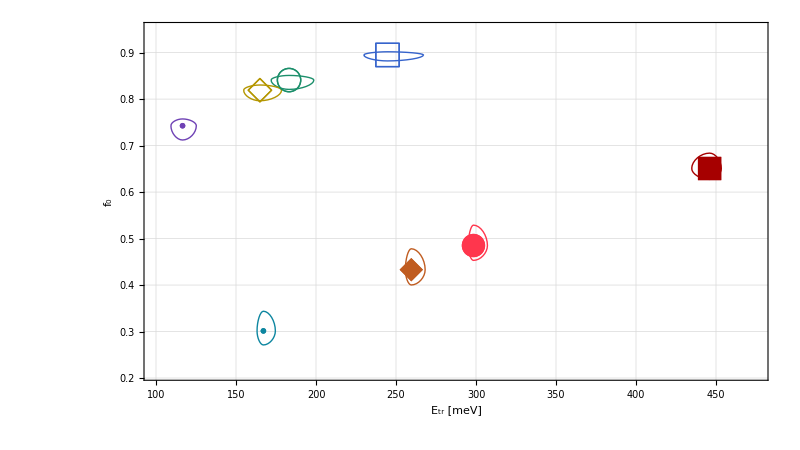
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0701-dir-foxy-vs-etr-allmus-abbrleg.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0701-dir-foxy-vs-etr-allmus-abbrleg.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0701-dir-foxy-vs-etr-allmus-abbrleg.pdf}}
-Graphics-

```mathematica
showandexp["0701-dir-foxy-vs-etr-allmus-abbrleg",#]&@
Normal@dsar[
KeyValueMap[
Module[{outkey=#1,inass=#2},
KeyValueMap[{
#1<>", "<>ToString[envlegabbr[outkey]]->{#2}
}&][inass]
]&]
/*
Association
/*
(dslp[
{
FrameLabel->{{"f_0",None},{"E_tr [meV]",None}},
PlotRange->{{100,475},{0.21,0.95}},
PlotLegends->Placed[PointLegend[Automatic,
LegendLayout->(framegrid[
Map[
Row,
Transpose@ArrayReshape[#,{4,2,2}],
{2}
]
]&)
],Above],
"ls"->24,
"mt"->feriff
}
]),
"rk",
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*Map[makeebars]
,
"d0",
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"f_0^x"->#[[1]],"f_0^y"->#[[2]]|>&)
]
```

### For table of f_0^j/μ_i^j

#### UPDATE 7/15: Move tabulated ratios to appendix, in Results section only show average values

```mathematica
dsar[
All,
"rk",
All,
"d0",
<|
"fox/mux"->{
(("fox"/*1/*selchop[])/*1),
("ndeparams"/*"mux")
}
/*(#[[1]]/#[[2]]&),
"foy/muy"->{
(("foy"/*1/*selchop[])/*1),
("ndeparams"/*"muy")
}
/*(#[[1]]/#[[2]]&)
|>
][Dataset];
LightBlue~bg~%[All,Transpose][Dataset][All,All,Values/*Mean]
```

Dataset[<>]

#### Original full table of all values now in appendix (7/15)

```mathematica
LightBlue~bg~dsar[
All,
"rk",
All,
"d0",
<|
"fox/mux"->{
(("fox"/*1/*selchop[])/*1),
("ndeparams"/*"mux")
}
/*(#[[1]]/#[[2]]&),
"foy/muy"->{
(("foy"/*1/*selchop[])/*1),
("ndeparams"/*"muy")
}
/*(#[[1]]/#[[2]]&)
|>
]
```

Dataset[<>]

### Change in fox/y and Etr w/ κ

```mathematica
Normal@dsar[
All/*Transpose,
"rk",
All,
"d0",
{
{
ev2etr/*Values,
"fox"/*1/*Values
}
/*
(Flatten[#,{{2},{1}}]&)
/*
selchpy[]
/*
1,
{
ev2etr/*Values,
"foy"/*1/*Values
}
/*
(Flatten[#,{{2},{1}}]&)
/*
selchpy[]
/*
1
}
][
{
Map[Module[
{
allx=Values[#][[;;,1]],
ally=Values[#][[;;,2]]
},
{
{allx,Table[100*Abs[allx[[i+1,1]]-allx[[i,1]]]/allx[[i,1]],{i,3}],Table[100*Abs[allx[[i+1,2]]-allx[[i,2]]]/allx[[i,2]],{i,3}]},
{ally,Table[100*Abs[ally[[i+1,1]]-ally[[i,1]]]/ally[[i,1]],{i,3}],Table[100*Abs[ally[[i+1,2]]-ally[[i,2]]]/ally[[i,2]],{i,3}]}
}//framegrid
]&],
All
}
]
```

{<|mu1→{{449.506,0.627313},{296.08,0.453054},{256.348,0.400159},{163.153,0.271147}} | {34.1321,13.4193,36.3551} | {27.7787,11.6752,32.2402}
{{229.879,0.901817},{171.919,0.85094},{154.781,0.830339},{109.32,0.757334}} | {25.2132,9.96843,29.3711} | {5.6416,2.42097,8.79215},mu2→{{446.347,0.637568},{295.181,0.466012},{255.839,0.413285},{163.19,0.282915}} | {33.8673,13.328,36.214} | {26.9079,11.3144,31.5449}
{{236.532,0.898173},{176.451,0.845118},{158.718,0.823697},{111.778,0.748191}} | {25.4008,10.05,29.5742} | {5.90694,2.53469,9.16669},mu3→{{434.827,0.683802},{295.225,0.528886},{257.822,0.478058},{167.542,0.343657}} | {32.1052,12.6693,35.0163} | {22.655,9.61039,28.1141}
{{267.174,0.882142},{198.651,0.82089},{178.466,0.796464},{125.195,0.712005}} | {25.6475,10.1608,29.8494} | {6.94352,2.9756,10.6042},mu4→{{453.299,0.654179},{307.149,0.492189},{268.222,0.440529},{174.602,0.307583}} | {32.2415,12.6736,34.9038} | {24.7623,10.496,30.1788}
{{245.188,0.897753},{185.609,0.846828},{167.807,0.826268},{120.062,0.753342}} | {24.2993,9.59151,28.4523} | {5.67258,2.42783,8.82594}|>,<|mu1→<|fs→{{449.506,0.627313},{229.879,0.901817}},ss→{{296.08,0.453054},{171.919,0.85094}},hs→{{256.348,0.400159},{154.781,0.830339}},he→{{163.153,0.271147},{109.32,0.757334}}|>,mu2→<|fs→{{446.347,0.637568},{236.532,0.898173}},ss→{{295.181,0.466012},{176.451,0.845118}},hs→{{255.839,0.413285},{158.718,0.823697}},he→{{163.19,0.282915},{111.778,0.748191}}|>,mu3→<|fs→{{434.827,0.683802},{267.174,0.882142}},ss→{{295.225,0.528886},{198.651,0.82089}},hs→{{257.822,0.478058},{178.466,0.796464}},he→{{167.542,0.343657},{125.195,0.712005}}|>,mu4→<|fs→{{453.299,0.654179},{245.188,0.897753}},ss→{{307.149,0.492189},{185.609,0.846828}},hs→{{268.222,0.440529},{167.807,0.826268}},he→{{174.602,0.307583},{120.062,0.753342}}|>|>}

## Make a table of E_tr,f_0,α, and 𝒜:

```mathematica
dsar[
All,
"rk",
All
/*
Transpose,
"d0",
<|
"X"->{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values,
gsabx/*(;;6)/*Map[#[5*10^15,10^13]&]/*QuantityMagnitude/*Values,
gsafx/*(;;6)/*Map[#[5*10^15,10^13]&]/*QuantityMagnitude/*Values
}
/*
flatrans
/*
selchpy[]/*1,
"Y"->{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values,
gsaby/*(;;6)/*Map[#[5*10^15,10^13]&]/*QuantityMagnitude/*Values,
gsafy/*(;;6)/*Map[#[5*10^15,10^13]&]/*QuantityMagnitude/*Values
}
/*
flatrans
/*
selchpy[]/*1
|>
][Dataset];
TableForm[
{
LightCyan~bg~(dxoptprop=%[All,"X"][Dataset]),
LightGreen~bg~(dyoptprop=%[All,"Y"][Dataset])
}
]
```

Dataset[<>]
Dataset[<>]

```mathematica
dxoptprop[All,({Mean[Values[#][[;;,1]]],Mean[Values[#][[;;,2]]],Mean[Values[#][[;;,3]]],Mean[Values[#][[;;,4]]]}&)]
dyoptprop[All,({Mean[Values[#][[;;,1]]],Mean[Values[#][[;;,2]]],Mean[Values[#][[;;,3]]],Mean[Values[#][[;;,4]]]}&)]
```

Dataset[<>]

Dataset[<>]

```mathematica
11.3/5.4
24.4/6.5
2716/5//N
```

2.09259

3.75385

543.2

### Unsimplify a bit to look under the hood

For all quantities except E_tr^X, the order of the μ_i changes...
Is something wrong? Is it because the n of the (1,0) state changes?
Nothing is wrong, but it’s apparently not because of how (1,0) gets shuffled around when changing environments...
hmmm...

```mathematica
dsar[
All,
"rk",
All
/*
Transpose,
"d0",
<|
"X"-><|
"En"->"ndeevs"/*(;;6)/*Values,
"Etr"->ev2etr/*(;;6)/*Values,
"f0x"->gsfox/*(;;6)/*Values/*Map[If[QuantityMagnitude[#]<0.1,Style[#,Red,FontSize->6],NumberForm[#,4]]&],
"alx"->gsabx/*(;;6)/*Map[#[10^15,10^13]&]/*Values/*Map[If[QuantityMagnitude[#]<0.1,Style[#,Red,FontSize->6],NumberForm[#,4]]&],
"afx"->gsafx/*(;;6)/*Map[#[10^15,10^13]&]/*Values/*Map[If[QuantityMagnitude[#]<0.0001,Style[#,Red,FontSize->6],NumberForm[#,4]]&]
|>,
"Y"-><|
"En"->"ndeevs"/*(;;6)/*Values,
"Etr"->ev2etr/*(;;6)/*Values,
"f0y"->gsfoy/*(;;6)/*Values/*Map[If[QuantityMagnitude[#]<0.001,Style[#,Red,FontSize->6],NumberForm[#,4]]&],
"aly"->gsaby/*(;;6)/*Map[#[10^15,10^13]&]/*Values/*Map[If[QuantityMagnitude[#]<0.001,Style[#,Red,FontSize->6],NumberForm[#,4]]&],
"afy"->gsafy/*(;;6)/*Map[#[10^15,10^13]&]/*Values/*Map[If[QuantityMagnitude[#]<0.0001,Style[#,Red,FontSize->6],NumberForm[#,4]]&]
|>
|>
][Dataset];
TableForm[
{
LightMagenta~bg~%[All,"X"/*Transpose][Dataset],
LightOrange~bg~%[All,"Y"/*Transpose][Dataset]
}
]
```

Dataset[<>]
Dataset[<>]

## Indirect

## EVS (n=1,2,3,6) for RK/C (all μ)

TODO: Use error “corridors” here too? (DONE)

### RE-RE-Re-Update (07/22): Label the curves with 1,2,etc.

```mathematica
potleg
shortpotleg=<|"rk"->"RK","c"->"C"|>
```

<|rk→RK, ,c→Coulomb, |>

<|rk→RK,c→C|>

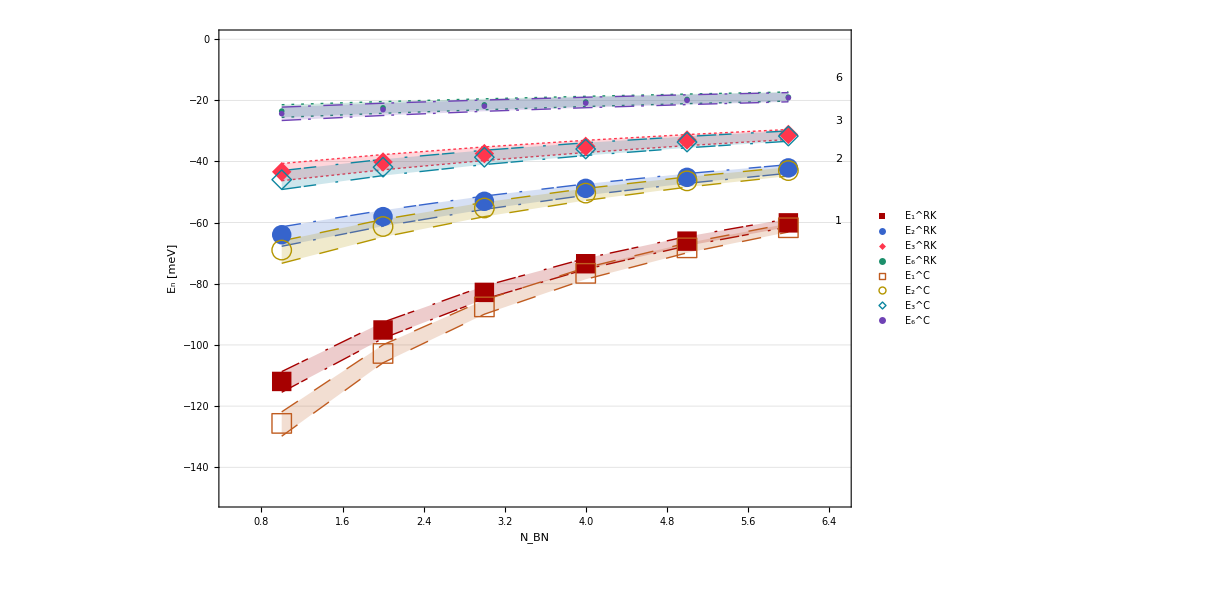
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0722-ind-evs-vs-d-rkc.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0722-ind-evs-vs-d-rkc.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0722-ind-evs-vs-d-rkc.pdf}}
-Graphics-

```mathematica
showandexp["0722-ind-evs-vs-d-rkc",#]&@
Normal@dsar[
"he"(* ENV *),
All (* POT *)
/*
KeyMap[shortpotleg]
/*
KeyValueMap[
Module[{pot=#1,vals=#2},
MapIndexed[
(tssf["E_(`1`)^(`2`)",If[#2[[1]]==4,6,#2[[1]]],pot]->#1)&,
vals
]
]&
]
/*
Flatten
/*
Association
/*
(
ListPlot[
#[[;;,;;6]],
PlotTheme->"Detailed",
PlotStyle->randash,
PlotMarkers->Transpose[{feordered,Table[20,{8}]}],
GridLines->{None,Automatic},
GridLinesStyle->Gray,
PlotRange->{{0.5,6.5},{0,-150}},
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["N_BN"],None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Bands",
IntervalMarkersStyle->Thick,
ImageSize->{wx=900,hx=600},
AspectRatio->hx/wx,
PlotLegends->Placed[PointLegend[
Automatic,Automatic,
LegendLayout->{"Row",1}],
Above],
Epilog->Table[
Inset[Framed[Style[tssf["`1`",tabind[[1]]],18,Black,FontFamily->"Arial"],FrameStyle->None,Background->White],
Scaled[tabind[[2]]],Scaled[tabind[[2]]]],
{tabind,
{
{1,{0.98,0.6}},
{2,{0.98,0.73}},
{3,{0.98,0.81}},
{6,{0.98,0.9}}
}
}
](*,
PlotLegends->Placed[PointLegend[
randash,
Values[envlegabbr],
LegendMarkers->Transpose[{fullmarks4,Table[22,{4}]}],
LegendLayout->{"Row",1}
],Above]*)
]&),
Values (* MUS *)/*
(Flatten[#,{{3},{2},{1},{4}}]&)/*
(Map[
Module[{nh=#[[1,1]],vals=#[[;;,2]]},
{nh,Around[Mean[vals],{Mean[vals]-Min[vals],Max[vals]-Mean[vals]}]}
]&,
#,
{2}
]&),
(3;;) (* D *)/*
(KeyValueMap[
Module[{dtox=keytox[#1],vals=#2},
Map[
{dtox,#}&,
vals
]]&,
#
]&),
"ndeevs",
{1,2,3,6}/*Values/*QuantityMagnitude
]
```

### RE-Re-Update (07/18): Bring back the bands b/c the x-axis here is distance.

```mathematica
potleg
shortpotleg=<|"rk"->"RK","c"->"C"|>
```

<|rk→RK, ,c→Coulomb, |>

<|rk→RK,c→C|>

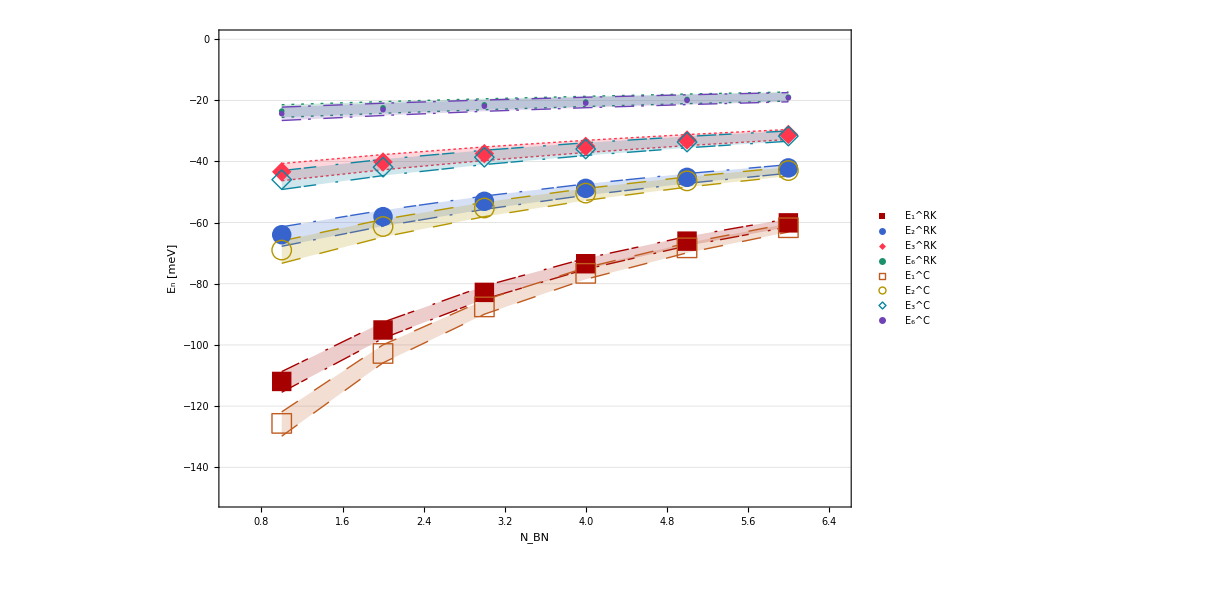
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0718-ind-evs-vs-d-rkc.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0718-ind-evs-vs-d-rkc.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0718-ind-evs-vs-d-rkc.pdf}}
-Graphics-

```mathematica
showandexp["0718-ind-evs-vs-d-rkc",#]&@
Normal@dsar[
"he"(* ENV *),
All (* POT *)
/*
KeyMap[shortpotleg]
/*
KeyValueMap[
Module[{pot=#1,vals=#2},
MapIndexed[
(tssf["E_(`1`)^(`2`)",If[#2[[1]]==4,6,#2[[1]]],pot]->#1)&,
vals
]
]&
]
/*
Flatten
/*
Association
/*
(
ListPlot[
#[[;;,;;6]],
PlotTheme->"Detailed",
PlotStyle->randash,
PlotMarkers->Transpose[{feordered,Table[20,{8}]}],
GridLines->{None,Automatic},
GridLinesStyle->Gray,
PlotRange->{{0.5,6.5},{0,-150}},
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["N_BN"],None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Bands",
IntervalMarkersStyle->Thick,
ImageSize->{wx=900,hx=600},
AspectRatio->hx/wx,
PlotLegends->Placed[PointLegend[
Automatic,Automatic,
LegendLayout->{"Row",1}],
Above](*,
PlotLegends->Placed[PointLegend[
randash,
Values[envlegabbr],
LegendMarkers->Transpose[{fullmarks4,Table[22,{4}]}],
LegendLayout->{"Row",1}
],Above]*)
]&),
Values (* MUS *)/*
(Flatten[#,{{3},{2},{1},{4}}]&)/*
(Map[
Module[{nh=#[[1,1]],vals=#[[;;,2]]},
{nh,Around[Mean[vals],{Mean[vals]-Min[vals],Max[vals]-Mean[vals]}]}
]&,
#,
{2}
]&),
(3;;) (* D *)/*
(KeyValueMap[
Module[{dtox=keytox[#1],vals=#2},
Map[
{dtox,#}&,
vals
]]&,
#
]&),
"ndeevs",
{1,2,3,6}/*Values/*QuantityMagnitude
]
```

### Re-Update (07/17): Discrete points (UPDATE 07/18: trimming to N_BN≤6)

```mathematica
potleg
shortpotleg=<|"rk"->"RK","c"->"C"|>
```

<|rk→RK, ,c→Coulomb, |>

<|rk→RK,c→C|>

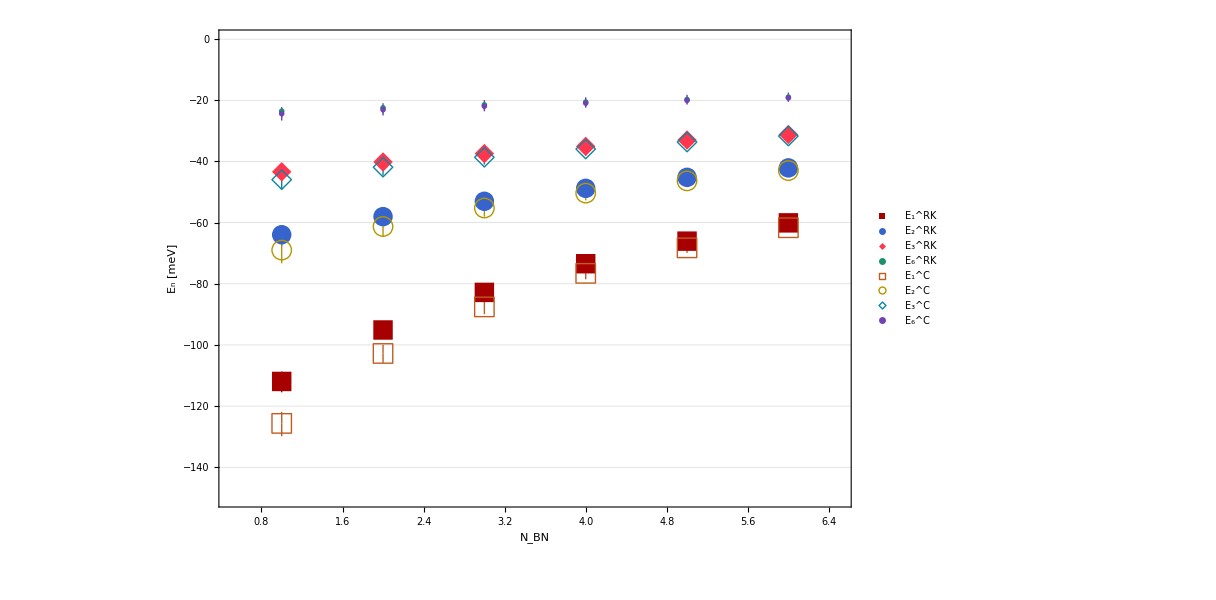
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0717-ind-evs-vs-d-rkc.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0717-ind-evs-vs-d-rkc.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0717-ind-evs-vs-d-rkc.pdf}}
-Graphics-

```mathematica
showandexp["0717-ind-evs-vs-d-rkc",#]&@
Normal@dsar[
"he"(* ENV *),
All (* POT *)
/*
KeyMap[shortpotleg]
/*
KeyValueMap[
Module[{pot=#1,vals=#2},
MapIndexed[
(tssf["E_(`1`)^(`2`)",If[#2[[1]]==4,6,#2[[1]]],pot]->#1)&,
vals
]
]&
]
/*
Flatten
/*
Association
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
PlotStyle->randash,
PlotMarkers->Transpose[{feordered,Table[20,{8}]}],
GridLines->{None,Automatic},
GridLinesStyle->Gray,
PlotRange->{{0.5,6.5},{0,-150}},
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["N_BN"],None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Fences",
IntervalMarkersStyle->Thick,
ImageSize->{wx=900,hx=600},
AspectRatio->hx/wx,
PlotLegends->Placed[PointLegend[
Automatic,Automatic,
LegendLayout->{"Row",1}],
Above](*,
PlotLegends->Placed[PointLegend[
randash,
Values[envlegabbr],
LegendMarkers->Transpose[{fullmarks4,Table[22,{4}]}],
LegendLayout->{"Row",1}
],Above]*)
]&),
Values (* MUS *)/*
(Flatten[#,{{3},{2},{1},{4}}]&)/*
(Map[
Module[{nh=#[[1,1]],vals=#[[;;,2]]},
{nh,Around[Mean[vals],{Mean[vals]-Min[vals],Max[vals]-Mean[vals]}]}
]&,
#,
{2}
]&),
(3;;) (* D *)/*
(KeyValueMap[
Module[{dtox=keytox[#1],vals=#2},
Map[
{dtox,#}&,
vals
]]&,
#
]&),
"ndeevs",
{1,2,3,6}/*Values/*QuantityMagnitude
]
```

### Update w/ error “corridors”

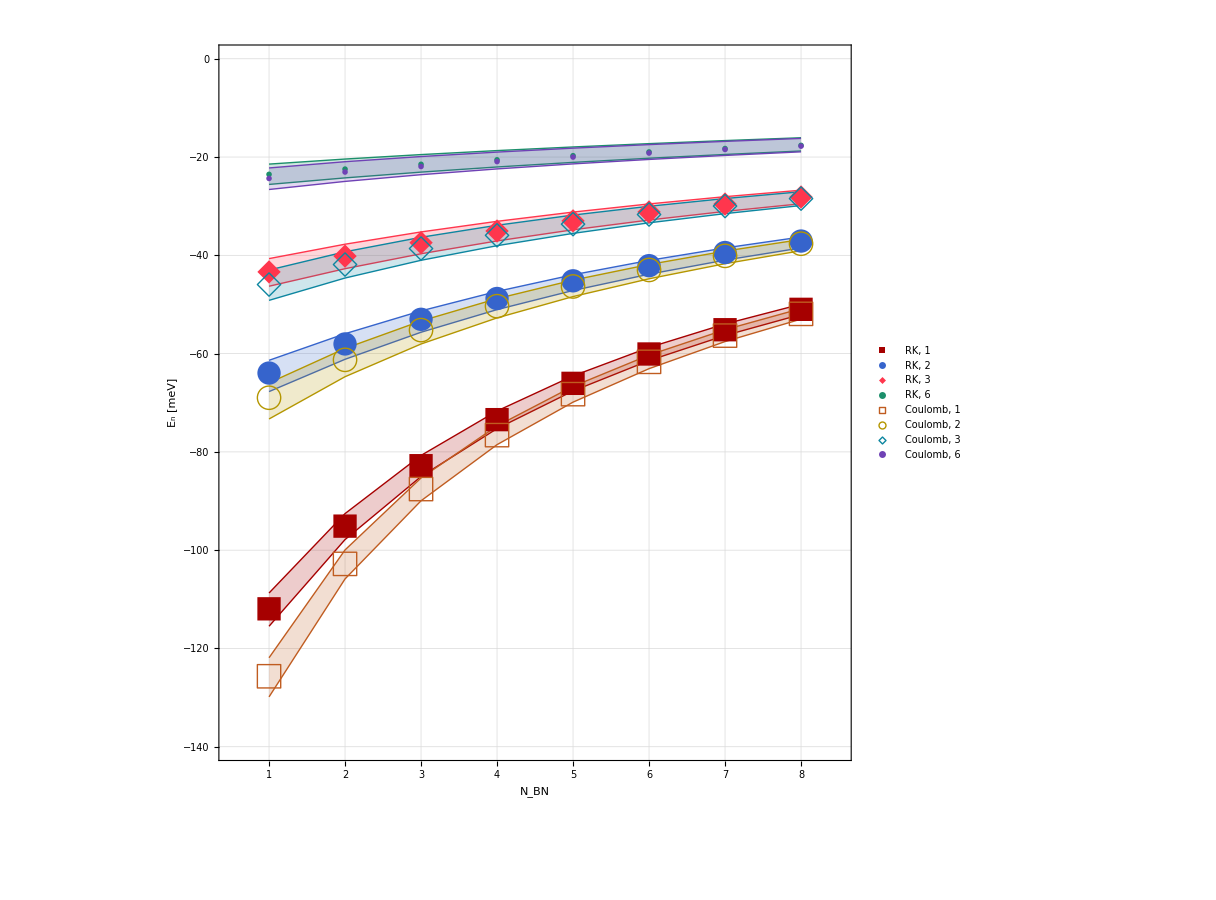
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0701-ind-evs-vs-d-rkc.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0701-ind-evs-vs-d-rkc.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0701-ind-evs-vs-d-rkc.pdf}}
-Graphics-

```mathematica
showandexp["0701-ind-evs-vs-d-rkc",#]&@
Normal@dsar[
"he"(* ENV *),
All (* POT *)
/*
KeyMap[potleg]
/*
KeyValueMap[
Module[{pot=#1,vals=#2},
MapIndexed[
{pot<>tssf["`1`",If[First[#2]==4,6,First[#2]]]->#1}&,
vals
]
]&
]
/*
Flatten
/*
Association
/*
(dslp[
{
FrameLabel->{{"E_n [meV]",None},{"N_BN",None}},
IntervalMarkers->"Bands",
PlotRange->{{0.5,8.5},{-140,0}},
"is"->{900,900}
}
]),
Values (* MUS *)
/*
(Flatten[#,{{3},{2},{1},{4}}]&)/*
(Map[
Module[{nh=#[[1,1]],vals=#[[;;,2]]},
{nh,Around[Mean[vals],{Mean[vals]-Min[vals],Max[vals]-Mean[vals]}]}
]&,
#,
{2}
]&),
(3;;) (* D *)/*
(KeyValueMap[
Module[{dtox=keytox[#1],vals=#2},
Map[
{dtox,#}&,
vals
]]&,
#
]&),
"ndeevs",
{1,2,3,6}/*Values/*QuantityMagnitude
]
```

### Compare results for different μ_i

```mathematica
dsar[
"he",
All,
All/*Transpose,
(3;;),
"ndeevs"/*1
][
All,
All,
Values/*pdiff
]
```

Dataset[<>]

### Calculate percent diffs between RK and C for analysis in the text

```mathematica
LightCyan~bg~Normal@dsar[
"he",
(<|
"pdiff"->framegrid@Transpose@Map[
TableForm,
Table[
pdiff[#["rk",mukey,dkey,"ndeevs",ikey],#["c",mukey,dkey,"ndeevs",ikey]],
{mukey,mukeys},{dkey,{"d2","d3","d4","d5","d6","d7","d8","d9"}},{ikey,{"i1","i2","i3","i4","i5","i6"}}
],
{2}
]
|>&)
]
```

<|pdiff→11.4258
7.58428
5.75019
4.42985
3.76532
2.65149 | 11.4398
7.47405
5.67082
4.34213
2.7544
3.69811 | 11.615
7.21714
5.55681
3.4345
4.14941
3.59125 | 11.7166
7.90597
6.02238
4.65575
3.24817
3.95833
7.68202
5.43021
4.16764
3.29244
2.77536
2.17349 | 7.69211
5.36438
4.10854
3.23151
2.24844
2.71635 | 7.80512
5.21294
4.00462
2.73287
3.0896
2.62025 | 7.86325
5.63157
4.34499
3.44147
2.60041
2.90815
5.52185
4.06708
3.16932
2.54926
2.13995
1.80081 | 5.52939
4.02441
3.12498
2.50396
1.85661
2.09161 | 5.60792
3.92753
3.03902
2.21044
2.3915
2.02131 | 5.64481
4.20311
3.29242
2.65388
2.1139
2.23668
4.15865
3.15511
2.495
2.03597
1.5111
1.70406 | 4.16447
3.12574
2.46122
2.00027
1.5537
1.66711 | 4.222
3.05995
2.39174
1.81874
1.90728
1.62264 | 4.24701
3.25221
2.58438
2.11301
1.74667
1.77671
3.24273
2.51676
2.01707
1.66529
1.28388
1.3925 | 3.24736
2.4956
1.99091
1.63582
1.31719
1.36628 | 3.29119
2.44886
1.93462
1.52041
1.55767
1.34182 | 3.30896
2.58898
2.08421
1.72427
1.46543
1.44796
2.59783
2.05326
1.66572
1.38785
1.10336
1.16349 | 2.60159
2.03746
1.64508
1.36279
1.13002
1.14636 | 2.63601
2.00308
1.59883
1.28918
1.29733
1.13453 | 2.64909
2.10871
1.71752
1.4344
1.24644
1.20629
2.12685
1.70648
1.39975
1.17419
0.957977
0.99141 | 2.12996
1.69434
1.38314
1.15267
0.979791
0.981244 | 2.15763
1.66834
1.34436
1.10689
1.09871
0.975146 | 2.16753
1.75012
1.44061
1.21181
1.07308
1.02483
1.7726
1.44048
1.19345
1.00597
0.839326
0.859436 | 1.7752
1.43093
1.17978
0.987576
0.857545
0.854038 | 1.79787
1.41081
1.14659
0.960891
0.944101
0.848175 | 1.80554
1.47551
1.22629
1.0369
0.933721
0.885926|>

### Paper figure (as of 6/25)

```mathematica
(*showandexp["ind-evs-vs-d-rkc",#]&@*)
dsar[
"he",
All
/*
flatassmerge
/*
KeyMap[
StringReplace[
#,
{
"rk"->"RK, ",
"c"->"Coulomb, ",
"i"->"",
n:DigitCharacter..:>tssf["`1`",n]
}
]&
],
"mu1",
(2;;)
/*
Transpose
/*
Map[
KeyValueMap[
{
QuantityMagnitude[Quantity[rightd[(ToExpression@StringCases[#1,DigitCharacter..])[[1]]-1],"BohrRadius"],"Nanometers"],
Abs@QuantityMagnitude@#2
}&,
#
]&
],
"ndeevs",
(;;4),
QuantityMagnitude/*Abs
][
(
ListLinePlot[
#,
PlotTheme->"Detailed",
PlotStyle->randash,
PlotMarkers->Transpose[{Flatten[{fullmarks4,emmarks4}],Table[22,{8}]}],
GridLinesStyle->Gray,
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["Vertical separation, D [nm]"],None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Bands",
ImageSize->{wx=900,hx=900},
AspectRatio->hx/wx,
PlotLegends->Placed[LineLegend[
Automatic,
LegendLayout->{"Column",1}
],
Right]
]
&)
]
```

## Indirect Optical Properties: Thin plots (one for each N_BN) w/ all μ ellipses, x/y and RK/C

Within each plot we can do the same thing as for direct:
DIR: (e.g.) f_0 vs. E_tr; {x & y} & {all envs}
IND: f_0 vs. E_tr; {x & y} & {RK & C}

### Table of f_0 vs. E_tr for N_BN≤6 (new figure as of 07/18)

```mathematica
etrxrange=<|1->{40,105},2->{30,80},3->{20,70},4->{20,55},5->{15,50},6->{10,45},7->{10,40},8->{10,35}|>;
```

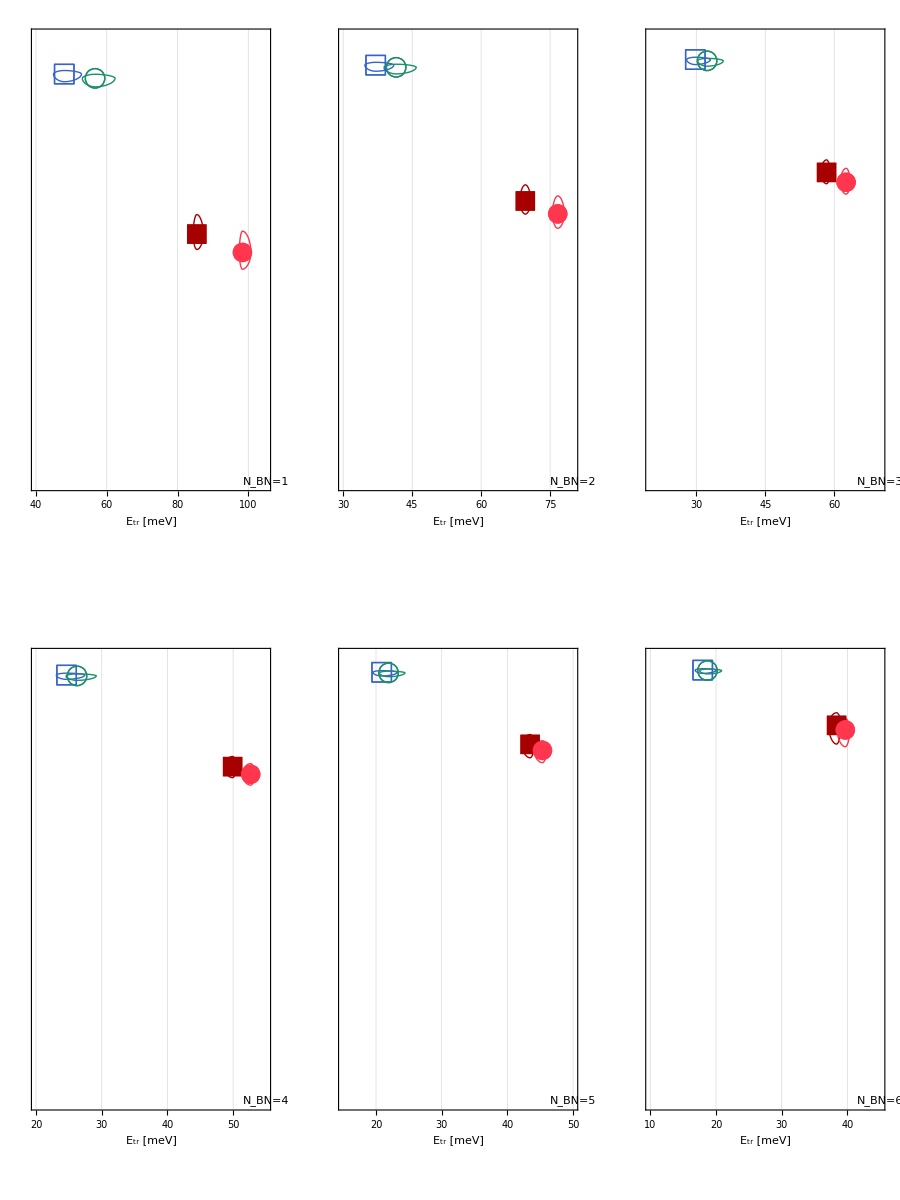
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0718-ind-foxy-allmus-rkc-nbnleq6.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0718-ind-foxy-allmus-rkc-nbnleq6.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0718-ind-foxy-allmus-rkc-nbnleq6.pdf}}
-Graphics-

```mathematica
showandexp["0718-ind-foxy-allmus-rkc-nbnleq6",#]&@
GraphicsGrid[ArrayReshape[
Table[
Normal@dsar[
"he",
All
/*
KeyMap[potleg]
/*
flasme
/*
Merge[Identity]
/*
(dslpe[
{
FrameLabel->{{None,None},{"E_tr [meV]",None}},
FrameTicks->{{None,None},{Automatic,None}},
PlotRange->{etrxrange[[Key[nbn]]],{0,1}},
PlotLegends->None(*Placed[PointLegend[Automatic,
LegendLayout->{"Row",1}
],Above]*),
Epilog->{
Inset[
Framed[
Style[TraditionalForm@StringForm["N_BN=`1`",nbn],24,Black,FontFamily->"Arial"],
FrameStyle->None,Background->White
],
Scaled[{0.98,0.02}],
Scaled[{0.98,0.02}]
]
},
"ls"->24,
"ms"->20,
"mt"->feriff,
"is"->{150,300}*2
}
]),
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*
Map[makeebars]
,
tssf["d`1`",nbn+1],
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"f_0^x"->#[[1]],"f_0^y"->#[[2]]|>&)
],
{nbn,6}],{2,3}],
ImageSize->{900,1200}]
```

### Table of f_0 vs. E_tr for all N_BN (new figure as of 07/07)

```mathematica
etrxrange=<|1->{40,105},2->{30,80},3->{20,70},4->{20,55},5->{15,50},6->{10,45},7->{10,40},8->{10,35}|>;
```

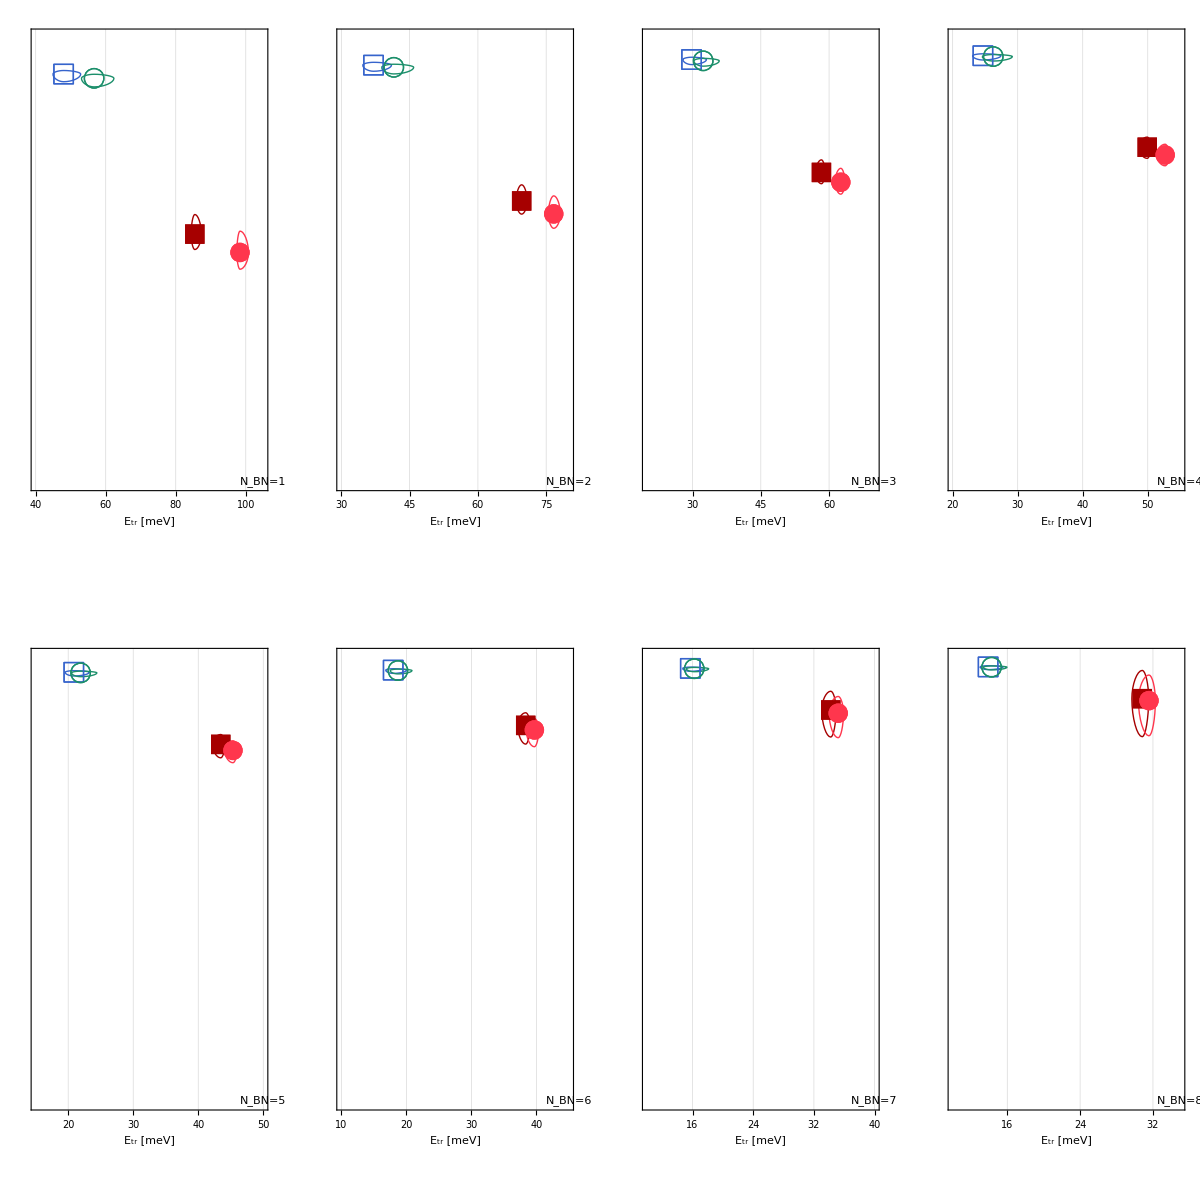
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0707-ind-foxy-allmus-rkc-allnbn.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0707-ind-foxy-allmus-rkc-allnbn.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0707-ind-foxy-allmus-rkc-allnbn.pdf}}
-Graphics-

```mathematica
showandexp["0707-ind-foxy-allmus-rkc-allnbn",#]&@
GraphicsGrid[ArrayReshape[
Table[
Normal@dsar[
"he",
All
/*
KeyMap[potleg]
/*
flasme
/*
Merge[Identity]
/*
(dslpe[
{
FrameLabel->{{None,None},{"E_tr [meV]",None}},
FrameTicks->{{None,None},{Automatic,None}},
PlotRange->{etrxrange[[Key[nbn]]],{0,1}},
PlotLegends->None(*Placed[PointLegend[Automatic,
LegendLayout->{"Row",1}
],Above]*),
Epilog->{
Inset[
Framed[
Style[TraditionalForm@StringForm["N_BN=`1`",nbn],24,Black,FontFamily->"Arial"],
FrameStyle->None,Background->White
],
Scaled[{0.98,0.02}],
Scaled[{0.98,0.02}]
]
},
"ls"->24,
"ms"->20,
"mt"->feriff,
"is"->{150,300}*2
}
]),
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*
Map[makeebars]
,
tssf["d`1`",nbn+1],
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"f_0^x"->#[[1]],"f_0^y"->#[[2]]|>&)
],
{nbn,8}],{2,4}],
ImageSize->{1200,1200}]
```

### f_0^j/μ_i^j ratios vs. N_BN

```mathematica
LightBlue~bg~dsar[
"he",
All,
All,
(3;;),
<|
"fox/mux"->{
(("fox"/*1/*selchop[])/*1),
("ndeparams"/*"mux")
}
/*(#[[1]]/#[[2]]&),
"foy/muy"->{
(("foy"/*1/*selchop[])/*1),
("ndeparams"/*"muy")
}
/*(#[[1]]/#[[2]]&)
|>
][All,Transpose][Transpose][All,Transpose][All,All,Transpose]
```

Dataset[<>]

### Make plots for α for analysis

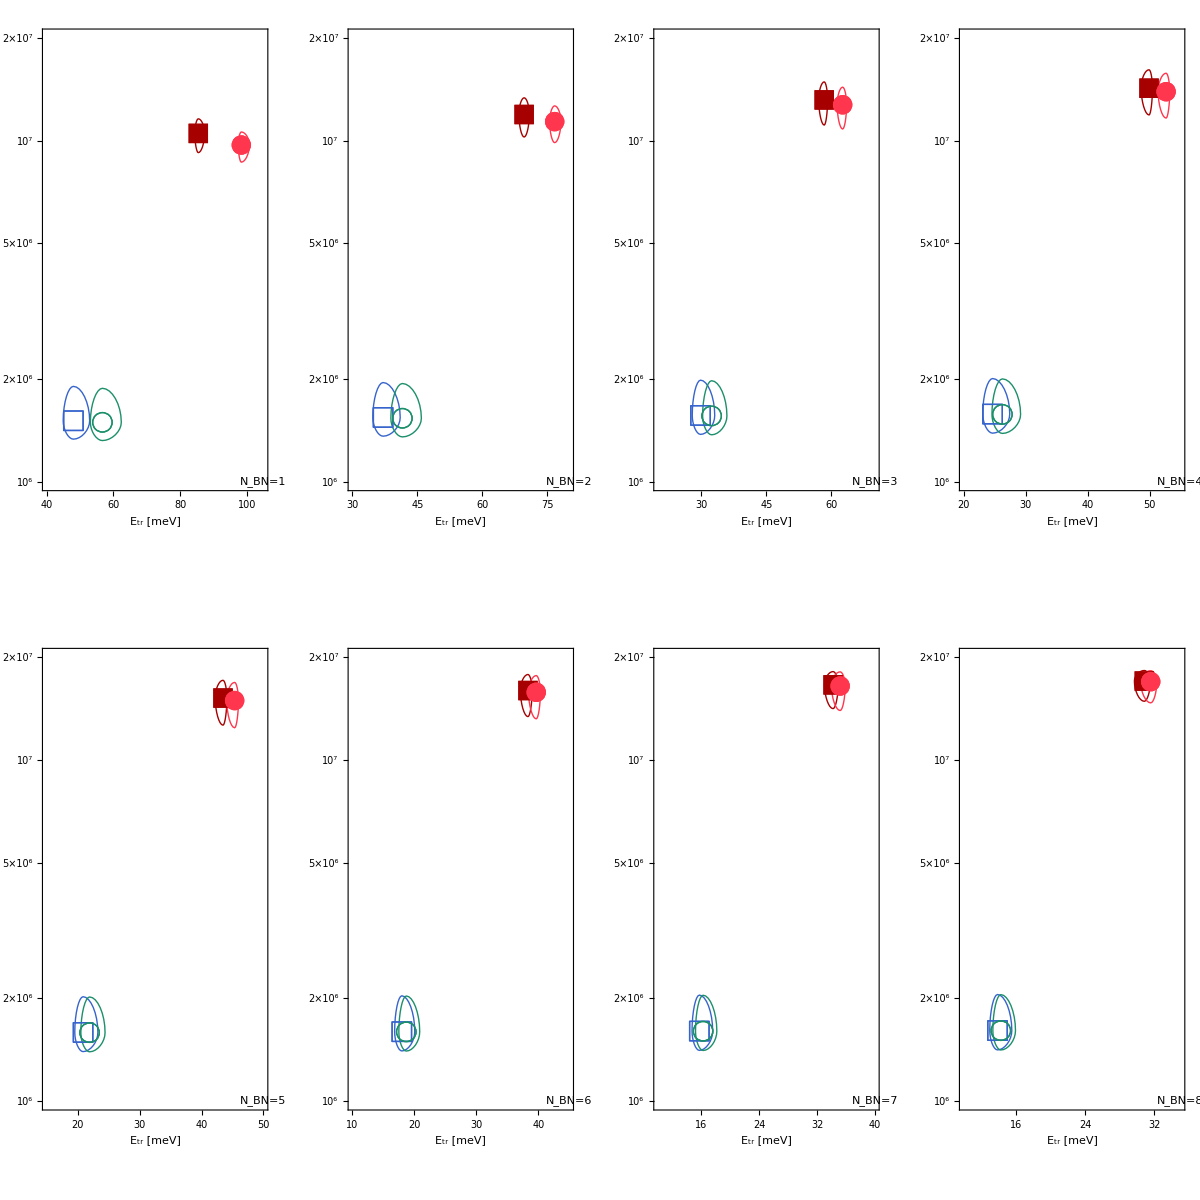

```mathematica
GraphicsGrid[ArrayReshape[
Table[
Normal@dsar[
"he",
All
/*
KeyMap[potleg]
/*
flasme
/*
Merge[Identity]
/*
(dslpe[
{
FrameLabel->{{None,None},{"E_tr [meV]",None}},
FrameTicks->{{None,None},{Automatic,None}},
PlotRange->{etrxrange[[Key[nbn]]],{10^6,2*10^7}},
GridLines->{Automatic,Flatten[Table[i*10^n,{i,10},{n,6,8}]]},
ScalingFunctions->"Log",
PlotLegends->None(*Placed[PointLegend[Automatic,
LegendLayout->{"Row",1}
],Above]*),
Epilog->{
Inset[
Framed[
Style[TraditionalForm@StringForm["N_BN=`1`",nbn],24,Black,FontFamily->"Arial"],
FrameStyle->None,Background->White
],
Scaled[{0.98,0.02}],
Scaled[{0.98,0.02}]
]
},
"ls"->24,
"ms"->20,
"mt"->feriff,
"is"->{150,300}*2
}
]),
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*
Map[makeebars]
,
tssf["d`1`",nbn+1],
{
{
ev2etr/*(;;6)/*Values,
gsabx/*(;;6)/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsaby/*(;;6)/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"α^x"->#[[1]],"α^y"->#[[2]]|>&)
],
{nbn,8}],{2,4}],
ImageSize->{1200,1200}]
```

### Make plots for 𝒜 for analysis

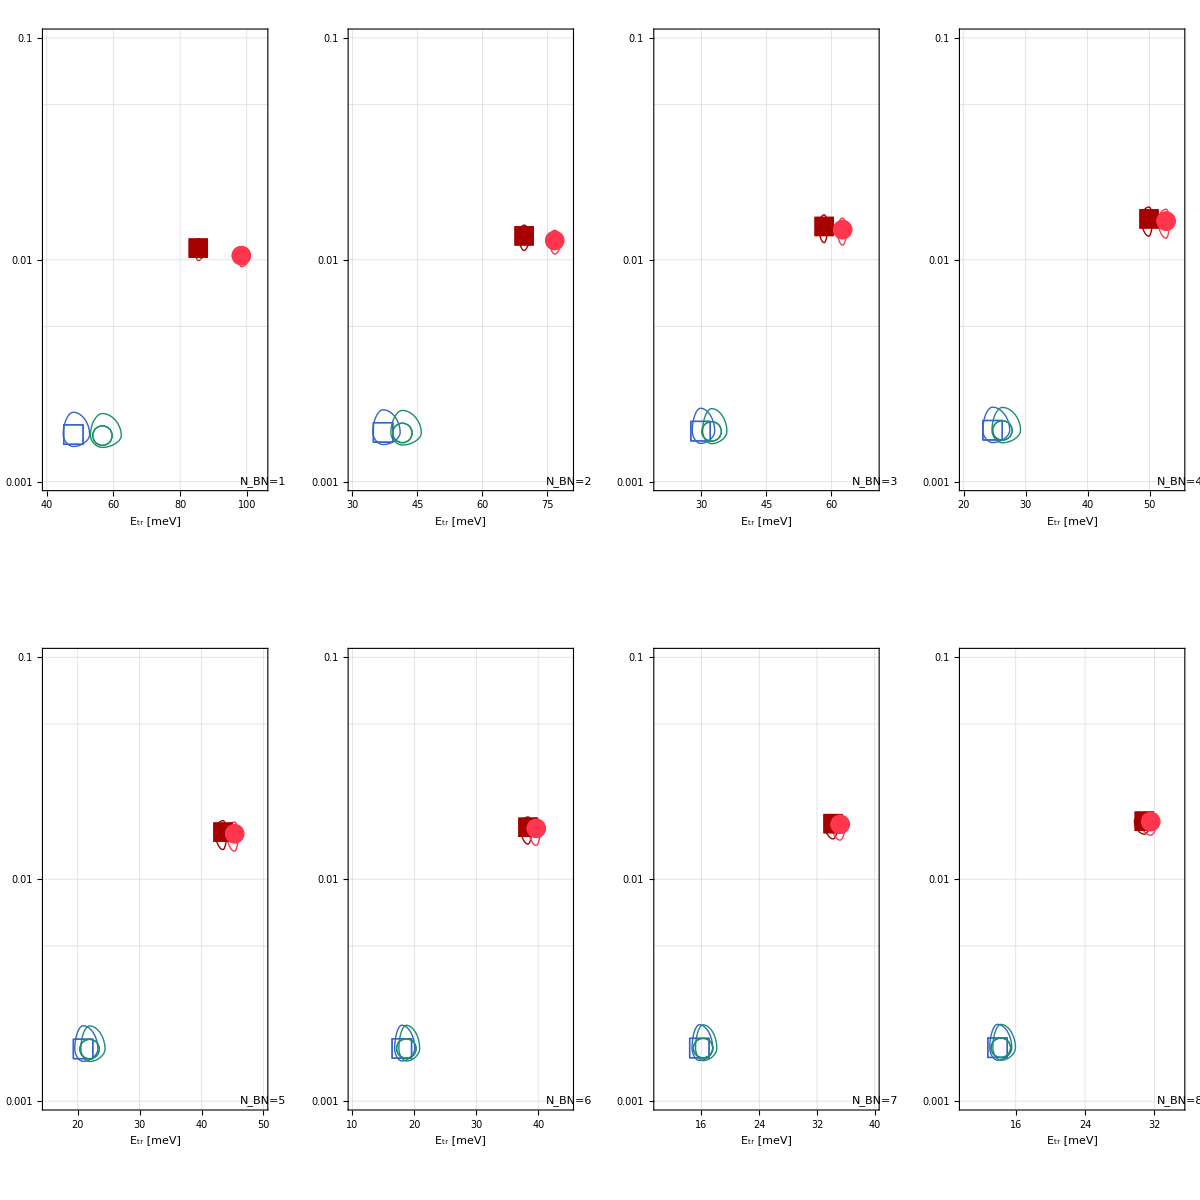

```mathematica
GraphicsGrid[ArrayReshape[
Table[
Normal@dsar[
"he",
All
/*
KeyMap[potleg]
/*
flasme
/*
Merge[Identity]
/*
(dslpe[
{
FrameLabel->{{None,None},{"E_tr [meV]",None}},
FrameTicks->{{None,None},{Automatic,None}},
PlotRange->{etrxrange[[Key[nbn]]],{0.001,0.1}},
ScalingFunctions->"Log",
PlotLegends->None(*Placed[PointLegend[Automatic,
LegendLayout->{"Row",1}
],Above]*),
Epilog->{
Inset[
Framed[
Style[TraditionalForm@StringForm["N_BN=`1`",nbn],24,Black,FontFamily->"Arial"],
FrameStyle->None,Background->White
],
Scaled[{0.98,0.02}],
Scaled[{0.98,0.02}]
]
},
"ls"->24,
"ms"->20,
"mt"->feriff,
"is"->{150,300}*2
}
]),
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*
Map[makeebars]
,
tssf["d`1`",nbn+1],
{
{
ev2etr/*(;;6)/*Values,
gsafx/*(;;6)/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsafy/*(;;6)/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"𝒜^x"->#[[1]],"𝒜^y"->#[[2]]|>&)
],
{nbn,8}],{2,4}],
ImageSize->{1200,1200}]
```

### Just make one table with E_tr,f_0,α, and 𝒜

#### Update: just present average values in Results Section

```mathematica
dsar["he","rk","mu1"]
```

$Aborted[]

```mathematica
?flatrans
```

```mathematica
dsar[
"he",
All,
Transpose,
(3;;),
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values,
{
(gsfox/*(;;6)/*Values),
("ndeparams"/*"mux")
}/*(#[[1]]/#[[2]]&),
gsabx/*(;;6)/*Map[#[5*10^15,10^13]&]/*QuantityMagnitude/*Values,
gsafx/*(;;6)/*Map[#[5*10^15,10^13]&]/*QuantityMagnitude/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values,
{
(gsfoy/*(;;6)/*Values),
("ndeparams"/*"muy")
}/*(#[[1]]/#[[2]]&),
gsaby/*(;;6)/*Map[#[5*10^15,10^13]&]/*QuantityMagnitude/*Values,
gsafy/*(;;6)/*Map[#[5*10^15,10^13]&]/*QuantityMagnitude/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"X"->#[[1]],"Y"->#[[2]]|>&)
][Dataset];
TableForm[
{
LightCyan~bg~(ixoptprop2=%[All,All,All,"X"][Dataset]),
LightGreen~bg~(iyoptprop2=%[All,All,All,"Y"][Dataset])
}
]
LightCyan~bg~(ixoptprop2avg=ixoptprop2[Transpose,All,({Mean[#[[;;,1]]],Mean[#[[;;,2]]],Mean[#[[;;,3]]],ScientificForm@Mean[#[[;;,4]]],ScientificForm@Mean[#[[;;,5]]]}&)])
LightGreen~bg~(iyoptprop2avg=iyoptprop2[Transpose,All,({Mean[#[[;;,1]]],Mean[#[[;;,2]]],Mean[#[[;;,3]]],ScientificForm@Mean[#[[;;,4]]],ScientificForm@Mean[#[[;;,5]]]}&)])
```

Dataset[<>]
Dataset[<>]

Dataset[<>]

Dataset[<>]

```mathematica
ixoptprop2avg[Transpose,All,3]
iyoptprop2avg[Transpose,All,3]
```

Dataset[<>]

Dataset[<>]

#### Calcs for all μ_i, now found in Appendix

```mathematica
dsar[
"he",
All,
Transpose,
(3;;),
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values,
gsabx/*(;;6)/*Map[#[5*10^15,10^13]&]/*QuantityMagnitude/*Values,
gsafx/*(;;6)/*Map[#[5*10^15,10^13]&]/*QuantityMagnitude/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values,
gsaby/*(;;6)/*Map[#[5*10^15,10^13]&]/*QuantityMagnitude/*Values,
gsafy/*(;;6)/*Map[#[5*10^15,10^13]&]/*QuantityMagnitude/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"X"->#[[1]],"Y"->#[[2]]|>&)
][Dataset];
TableForm[
{
LightCyan~bg~(ixoptprop=%[All,All,All,"X"][Dataset]),
LightGreen~bg~(iyoptprop=%[All,All,All,"Y"][Dataset])
}
]
```

Dataset[<>]
Dataset[<>]

```mathematica
ixoptprop[All,All,f]
```

Dataset[<>]

```mathematica
LightBlue~bg~ixoptprop[Transpose,All,({Mean[#[[;;,1]]],Mean[#[[;;,2]]],ScientificForm@Mean[#[[;;,3]]],ScientificForm@Mean[#[[;;,4]]]}&)]
LightGreen~bg~iyoptprop[Transpose,All,({Mean[#[[;;,1]]],Mean[#[[;;,2]]],ScientificForm@Mean[#[[;;,3]]],ScientificForm@Mean[#[[;;,4]]]}&)]
```

Dataset[<>]

Dataset[<>]

### Calculate % Differences for f_0 b/w RK and C potentials

```mathematica
?nestedgridWheaders
```

```mathematica
Module[{vals,pdiffs,pdiffsalt},
vals=dsar[
"he",
All,
All,
(3;;),
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"fox"->#[[1]],"foy"->#[[2]]|>&)
];
pdiffs=vals[
(Table[
gridWheaders[{
{
pdiff[#["rk",mukey,dkey,"fox"][[1]],#["c",mukey,dkey,"fox"][[1]]],
pdiff[#["rk",mukey,dkey,"fox"][[2]],#["c",mukey,dkey,"fox"][[2]]]
},
{
pdiff[#["rk",mukey,dkey,"foy"][[1]],#["c",mukey,dkey,"foy"][[1]]],
pdiff[#["rk",mukey,dkey,"foy"][[2]],#["c",mukey,dkey,"foy"][[2]]]
}
},
{"X","Y"},{"Etr","f0"}],
{mukey,mukeys},{dkey,{"d2","d3","d4","d5","d6","d7","d8","d9"}}
]&)
];
pdiffsalt=vals[
(Table[
{
{
pdiff[#["rk",mukey,dkey,"fox"][[1]],#["c",mukey,dkey,"fox"][[1]]],
pdiff[#["rk",mukey,dkey,"fox"][[2]],#["c",mukey,dkey,"fox"][[2]]]
},
{
pdiff[#["rk",mukey,dkey,"foy"][[1]],#["c",mukey,dkey,"foy"][[1]]],
pdiff[#["rk",mukey,dkey,"foy"][[2]],#["c",mukey,dkey,"foy"][[2]]]
}
},
{mukey,mukeys},{dkey,{"d2","d3","d4","d5","d6","d7","d8","d9"}}
]&)
/*
(Flatten[#,{{3},{1},{2},{4}}]&)
];
TableForm@{
LightGreen~bg~vals,
(*LightCyan~bg~vals[All,GroupBy[Map[Sort]]],*)
LightMagenta~bg~framegrid@Transpose@Normal@pdiffs,
LightOrange~bg~nestedgridWheaders[Normal@pdiffsalt,{Table[tssf["Nbn = `1`",i],{i,8}],{"Etr","f0"}},{{"X","Y"},mukeys}]
}
]
```

Dataset[<>]
  | Etr | f0
X | 13.7171 | 8.87078
Y | 16.6242 | 0.955837 |   | Etr | f0
X | 13.7982 | 8.52186
Y | 16.567 | 1.03038 |   | Etr | f0
X | 14.3444 | 6.41336
Y | 16.4754 | 1.3002 |   | Etr | f0
X | 14.2944 | 7.20083
Y | 16.869 | 0.918056
  | Etr | f0
X | 9.41515 | 5.44377
Y | 11.323 | 0.476825 |   | Etr | f0
X | 9.47317 | 5.30812
Y | 11.2882 | 0.514212 |   | Etr | f0
X | 9.84631 | 3.79518
Y | 11.2318 | 0.653689 |   | Etr | f0
X | 9.79953 | 4.40775
Y | 11.4721 | 0.457402
  | Etr | f0
X | 6.87938 | 3.56412
Y | 8.22065 | 0.276235 |   | Etr | f0
X | 6.92271 | 3.60183
Y | 8.19735 | 0.297887 |   | Etr | f0
X | 7.19328 | 2.65651
Y | 8.15901 | 0.379324 |   | Etr | f0
X | 7.15341 | 3.13237
Y | 8.32046 | 0.264179
  | Etr | f0
X | 5.25003 | 2.33203
Y | 6.24023 | 0.177168 |   | Etr | f0
X | 5.28351 | 2.49988
Y | 6.22368 | 0.190304 |   | Etr | f0
X | 5.48861 | 2.08927
Y | 6.19617 | 0.242331 |   | Etr | f0
X | 5.45499 | 2.42183
Y | 6.31141 | 0.168746
  | Etr | f0
X | 4.13826 | 1.43308
Y | 4.89673 | 0.123103 |   | Etr | f0
X | 4.16481 | 1.6905
Y | 4.88451 | 0.13282 |   | Etr | f0
X | 4.3257 | 1.75075
Y | 4.86407 | 0.166132 |   | Etr | f0
X | 4.29711 | 1.93555
Y | 4.9499 | 0.116335
  | Etr | f0
X | 3.34498 | 0.738485
Y | 3.94299 | 0.0910791 |   | Etr | f0
X | 3.36643 | 1.05284
Y | 3.93372 | 0.0985443 |   | Etr | f0
X | 3.49605 | 1.50031
Y | 3.91813 | 0.120195 |   | Etr | f0
X | 3.47142 | 1.54451
Y | 3.98419 | 0.0856411
  | Etr | f0
X | 2.75892 | 0.188003
Y | 3.24153 | 0.0713334 |   | Etr | f0
X | 2.77649 | 0.534
Y | 3.23433 | 0.0772732 |   | Etr | f0
X | 2.88308 | 1.27982
Y | 3.22215 | 0.0906851 |   | Etr | f0
X | 2.86163 | 1.20085
Y | 3.27443 | 0.0663408
  | Etr | f0
X | 2.3137 | 0.252058
Y | 2.71064 | 0.0587967 |   | Etr | f0
X | 2.32822 | 0.106846
Y | 2.70493 | 0.0635356 |   | Etr | f0
X | 2.41725 | 1.06821
Y | 2.69523 | 0.0707117 |   | Etr | f0
X | 2.39839 | 0.888607
Y | 2.7376 | 0.053895
  | mu1 | mu2 | mu3 | mu4
X |   | Etr | f0
Nbn = 1 | 13.7171 | 8.87078
Nbn = 2 | 9.41515 | 5.44377
Nbn = 3 | 6.87938 | 3.56412
Nbn = 4 | 5.25003 | 2.33203
Nbn = 5 | 4.13826 | 1.43308
Nbn = 6 | 3.34498 | 0.738485
Nbn = 7 | 2.75892 | 0.188003
Nbn = 8 | 2.3137 | 0.252058 |   | Etr | f0
Nbn = 1 | 13.7982 | 8.52186
Nbn = 2 | 9.47317 | 5.30812
Nbn = 3 | 6.92271 | 3.60183
Nbn = 4 | 5.28351 | 2.49988
Nbn = 5 | 4.16481 | 1.6905
Nbn = 6 | 3.36643 | 1.05284
Nbn = 7 | 2.77649 | 0.534
Nbn = 8 | 2.32822 | 0.106846 |   | Etr | f0
Nbn = 1 | 14.3444 | 6.41336
Nbn = 2 | 9.84631 | 3.79518
Nbn = 3 | 7.19328 | 2.65651
Nbn = 4 | 5.48861 | 2.08927
Nbn = 5 | 4.3257 | 1.75075
Nbn = 6 | 3.49605 | 1.50031
Nbn = 7 | 2.88308 | 1.27982
Nbn = 8 | 2.41725 | 1.06821 |   | Etr | f0
Nbn = 1 | 14.2944 | 7.20083
Nbn = 2 | 9.79953 | 4.40775
Nbn = 3 | 7.15341 | 3.13237
Nbn = 4 | 5.45499 | 2.42183
Nbn = 5 | 4.29711 | 1.93555
Nbn = 6 | 3.47142 | 1.54451
Nbn = 7 | 2.86163 | 1.20085
Nbn = 8 | 2.39839 | 0.888607
Y |   | Etr | f0
Nbn = 1 | 16.6242 | 0.955837
Nbn = 2 | 11.323 | 0.476825
Nbn = 3 | 8.22065 | 0.276235
Nbn = 4 | 6.24023 | 0.177168
Nbn = 5 | 4.89673 | 0.123103
Nbn = 6 | 3.94299 | 0.0910791
Nbn = 7 | 3.24153 | 0.0713334
Nbn = 8 | 2.71064 | 0.0587967 |   | Etr | f0
Nbn = 1 | 16.567 | 1.03038
Nbn = 2 | 11.2882 | 0.514212
Nbn = 3 | 8.19735 | 0.297887
Nbn = 4 | 6.22368 | 0.190304
Nbn = 5 | 4.88451 | 0.13282
Nbn = 6 | 3.93372 | 0.0985443
Nbn = 7 | 3.23433 | 0.0772732
Nbn = 8 | 2.70493 | 0.0635356 |   | Etr | f0
Nbn = 1 | 16.4754 | 1.3002
Nbn = 2 | 11.2318 | 0.653689
Nbn = 3 | 8.15901 | 0.379324
Nbn = 4 | 6.19617 | 0.242331
Nbn = 5 | 4.86407 | 0.166132
Nbn = 6 | 3.91813 | 0.120195
Nbn = 7 | 3.22215 | 0.0906851
Nbn = 8 | 2.69523 | 0.0707117 |   | Etr | f0
Nbn = 1 | 16.869 | 0.918056
Nbn = 2 | 11.4721 | 0.457402
Nbn = 3 | 8.32046 | 0.264179
Nbn = 4 | 6.31141 | 0.168746
Nbn = 5 | 4.9499 | 0.116335
Nbn = 6 | 3.98419 | 0.0856411
Nbn = 7 | 3.27443 | 0.0663408
Nbn = 8 | 2.7376 | 0.053895

```mathematica
dsar[
"he",
{
All,
All,
(3;;),
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"fox"->#[[1]],"foy"->#[[2]]|>&)
}
]
```

Failure[…]

# Old Figures

## Dir

## Figured out how to do f_0, α, and 𝒜!! (07/01: no more α, 𝒜; use scale factor instead)

### f_0 (Paper figure 06/28)

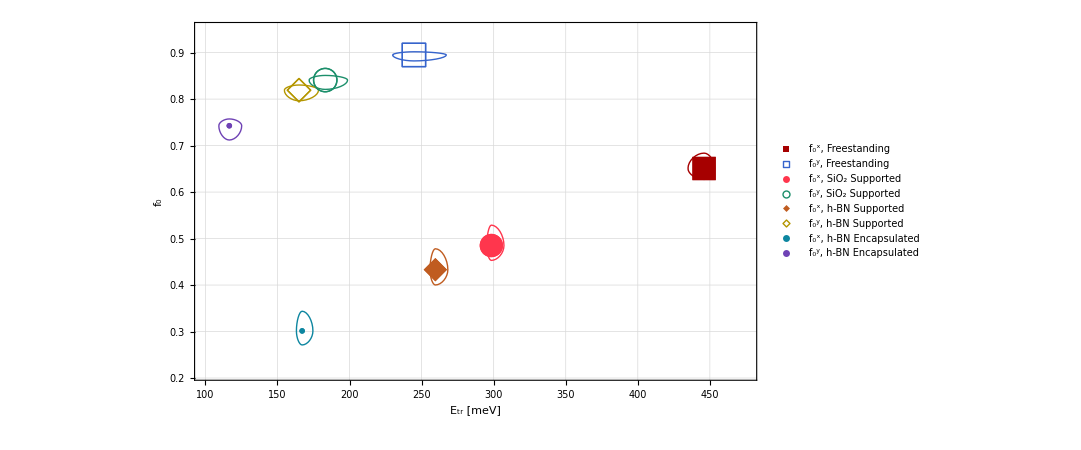
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0628-dir-foxy-vs-etr-allmus.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0628-dir-foxy-vs-etr-allmus.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0628-dir-foxy-vs-etr-allmus.pdf}}
-Graphics-

```mathematica
showandexp["0628-dir-foxy-vs-etr-allmus",#]&@
Normal@dsar[
KeyValueMap[
Module[{outkey=#1,inass=#2},
KeyValueMap[{
#1<>", "<>ToString[envleg[outkey]]->{#2}
}&][inass]
]&]
/*
Association
/*
(dslp[
{
FrameLabel->{{"f_0",None},{"E_tr [meV]",None}},
PlotRange->{{100,475},{0.21,0.95}},
PlotLegends->Placed[PointLegend[Automatic,
LegendLayout->(
framegrid[
Map[
(TableForm[#,TableDirections->Row,TableAlignments->Left]&),
ArrayReshape[#,{4,2,2}],
{2}
]
]&)
],Above],
"ls"->24,
"mt"->feriff
}
]),
"rk",
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*Map[makeebars]
,
"d0",
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"f_0^x"->#[[1]],"f_0^y"->#[[2]]|>&)
]
```

### α (Paper figure 06/28)

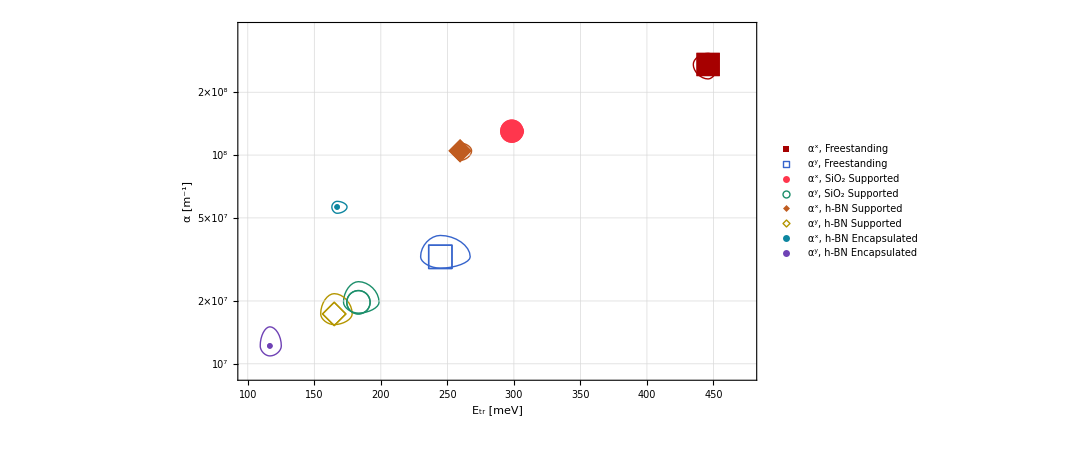
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0628-dir-alphaxy-vs-etr-allmus.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0628-dir-alphaxy-vs-etr-allmus.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0628-dir-alphaxy-vs-etr-allmus.pdf}}
-Graphics-

```mathematica
showandexp["0628-dir-alphaxy-vs-etr-allmus",#]&@
Normal@dsar[
KeyValueMap[
Module[{outkey=#1,inass=#2},
KeyValueMap[{
#1<>", "<>ToString[envleg[outkey]]->{#2}
}&][inass]
]&]
/*
Association
/*
(dslp[
{
FrameLabel->{{"α [m^-1]",None},{"E_tr [meV]",None}},
PlotRange->{{100,475},{9*10^6,4*10^8}},
ScalingFunctions->"Log",
PlotLegends->Placed[PointLegend[Automatic,
LegendLayout->(
framegrid[
Map[
(TableForm[#,TableDirections->Row,TableAlignments->Left]&),
ArrayReshape[#,{4,2,2}],
{2}
]
]&)
],Above],
"ls"->24,
"mt"->feriff
}
]),
"rk",
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*Map[makeebars]
,
"d0",
{
{
ev2etr/*(;;6)/*Values,
gsabx/*(;;6)/*Values/*(Map[#[n0,gam0]&])/*QuantityMagnitude
}
/*
flatrans
/*
selchpy[1]
/*1,
{
ev2etr/*(;;6)/*Values,
gsaby/*(;;6)/*Values/*(Map[#[n0,gam0]&])/*QuantityMagnitude
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"α^x"->#[[1]],"α^y"->#[[2]]|>&)
]
```

### 𝒜 (Paper figure 06/28)

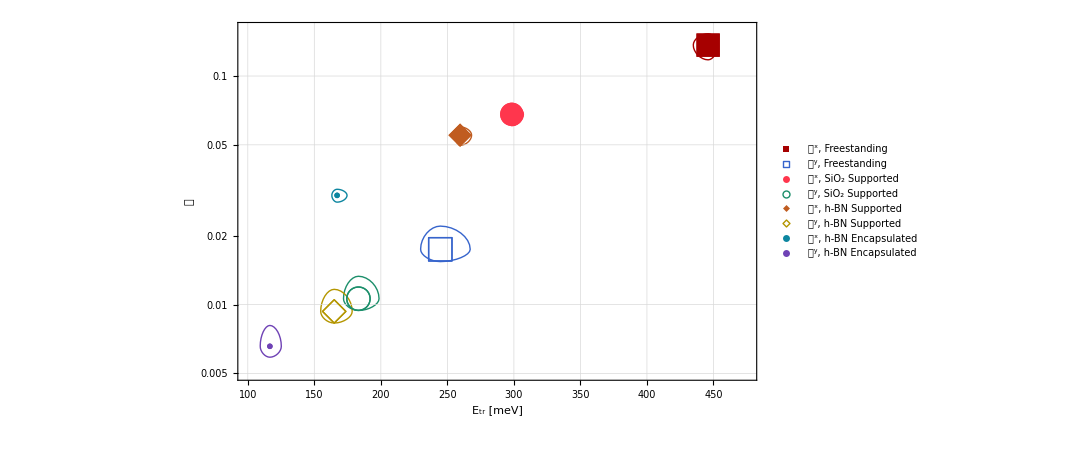
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0628-dir-afaxy-vs-etr-allmus.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0628-dir-afaxy-vs-etr-allmus.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0628-dir-afaxy-vs-etr-allmus.pdf}}
-Graphics-

```mathematica
showandexp["0628-dir-afaxy-vs-etr-allmus",#]&@
Normal@dsar[
KeyValueMap[
Module[{outkey=#1,inass=#2},
KeyValueMap[{
#1<>", "<>ToString[envleg[outkey]]->{#2}
}&][inass]
]&]
/*
Association
/*
(dslp[
{
FrameLabel->{{"𝒜",None},{"E_tr [meV]",None}},
PlotRange->{{100,475},{0.005,0.16}},
ScalingFunctions->"Log",
PlotLegends->Placed[PointLegend[Automatic,
LegendLayout->(
framegrid[
Map[
(TableForm[#,TableDirections->Row,TableAlignments->Left]&),
ArrayReshape[#,{4,2,2}],
{2}
]
]&)
],Above],
"ls"->24,
"mt"->feriff
}
]),
"rk",
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*Map[makeebars]
,
"d0",
{
{
ev2etr/*(;;6)/*Values,
gsafx/*(;;6)/*Values/*(Map[#[n0,gam0]&])/*QuantityMagnitude
}
/*
flatrans
/*
selchpy[]
/*1,
{
ev2etr/*(;;6)/*Values,
gsafy/*(;;6)/*Values/*(Map[#[n0,gam0]&])/*QuantityMagnitude
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"𝒜^x"->#[[1]],"𝒜^y"->#[[2]]|>&)
]
```

## Allowed transitions for n_i = [1,6] with lines connecting points

### Paper figure (6/25)

```mathematica
(*showandexp["i1to6-dir-fox-mu1",#]&@*)(* Raw output of the plotted dataset is captured by 'showandexp[]', then formatted into a centered column. This way, we can save the plot and legend separately as well as together, depending on what we want to show. *)
dsar[
"he","rk","mu1","d0","fox",
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
(#[[;;6]]&)
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
/*
(* Format the remaining "j_n" Keys for display in the graph by turning the association <| "j_n" -> Subscript[f, j_n], ... |> into a list where each data point has a Callout[] with the corresponding formatted Key. *)
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^x",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,24,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(* In order to more clearly show which transitions to and from are allowed, repeatedly draw a data point representing the initial state given by the "i_n" in between each actual transition *)
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(* Want to label each initial state, but implementing Callout[] in the preceding function would create multiple Callout[]'s on the same initial point, so just wrap the first initial point with a Callout[] *)
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1]]],Black,24,FontFamily->"Arial"],
{#[[1,1]]-0.1,((3*(1+Mod[#[[1,1]],2]))*10^-5)}
]
]&,
#
]&)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i=`1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*1.75,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{7*10^-6,1}},
FrameTicks->{{All,None},{All,None}},
FrameTicksStyle->Directive[24,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^x",None},{"Eigenstate, n",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed["h.e.; RK; μ_1; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{75,24}
]
]&)
]
(*showandexp["i1to6-dir-foy-mu1",#]&@*)(* Raw output of the plotted dataset is hidden, instead pull the plot and legend separately, then format it into a centered column. This way, we can save the plot and legend separately as well as together, depending on what we want to show. *)
dsar[
"he","rk","mu1","d0","foy",
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
(#[[;;6]]&)
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]/Chop[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
/*
(* Format the remaining "j_n" Keys for display in the graph by turning the association <| "j_n" -> Subscript[f, j_n], ... |> into a list where each data point has a Callout[] with the corresponding formatted Key. *)
(
Values/@MapIndexed[
Callout[
Flatten[
{
ToExpression@StringCases[#2[[2,1]],DigitCharacter..],
#1
}
],
Style[StandardForm@tssf["f_(`1` → `2`)^y",#1,#2]&@@Flatten[StringCases[#2[[;;,1]],DigitCharacter..]],Black,20,FontFamily->"Arial"]
]&,
#,
{2}
]&
)
/*
(* In order to more clearly show which transitions to and from are allowed, repeatedly draw a data point representing the initial state given by the "i_n" in between each actual transition *)
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(* Want to label each initial state, but implementing Callout[] in the preceding function would create multiple Callout[]'s on the same initial point, so just wrap the first initial point with a Callout[] *)
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1]]],Black,20,FontFamily->"Arial"],
{#[[1,1]]-0.1,((3*(1+Mod[#[[1,1]],2]))*10^-5)}
]
]&,
#
]&)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i=`1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*1.75,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{7*10^-6,10}},
FrameTicks->{{All,None},{All,None}},
FrameTicksStyle->Directive[24,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^y",None},{"Eigenstate, n",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed["h.e.; RK; μ_1; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{75,24}
]
]&)
]
```

## (f_0,α,𝒜) vs. E_tr (ugly, hard to read)

### f_0

```mathematica
(*showandexp["dir-foxy-vs-etr-allmus",#]&@*)
dsar[
"he",
"rk",
KeyMap[<|Table[tssf["mu`1`",i]->tssf["μ_(`1`)",i],{i,4}]|>[#]&]
/*
flatassmerge
/*
(
ListPlot[
Map[Values,#],
PlotTheme->"Detailed",
ImageSize->0.75*{wx=800,hx=450},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"f_0",None},{"Transition Energy, SubscriptBox[StyleBox[\"E\",FontSlant->\"Italic\"], \"tr\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"[\",FontSlant->\"Italic\"]meV]",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.02,0.02}],
Scaled[{0.02,0.02}]
]
}
]&),
"d0",
AssociationThread[
{"x","y"}->{
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
("fox"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1)
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;1)
/*
KeyMap[<|"i4"->{1,0},"i5"->{1,0},"i6"->{1,0},"i10"->{1,1},"i11"->{1,1}|>[#]&],
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
"foy"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;2)
/*
KeyMap[<|"i2"->{0,1},"i4"->{0,3},"i5"->{0,3},"i7"->{0,5},"i8"->{0,5},"i10"->{0,7}|>[#]&]
}
]
]
```

### α

```mathematica
(*showandexp["dir-absxy-vs-etr-allmu",#]&@*)
dsar[
"he","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->0.75*{wx=800,hx=450},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"α [m^-1]",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"alphax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5],
"alphay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
]
```

### 𝒜

```mathematica
(*showandexp["dir-afaxy-vs-etr-allmu",#]&@*)
dsar[
"he","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->0.75*{wx=800,hx=450},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"𝒜",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"afax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4],
"afay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
]
```

### Paper figure (6/25): Combined into grid (very, very ugly)

#### Original (for HE)

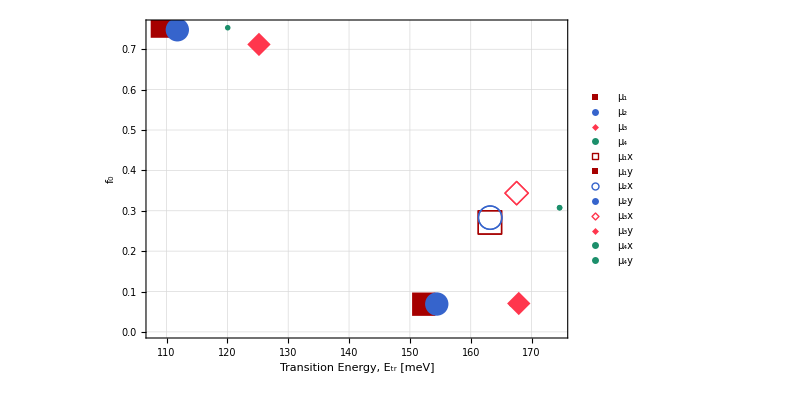
{{../../figures/comb-dir-he-foxy-vs-etr-allmus.pdf,../../figures/plt-dir-he-foxy-vs-etr-allmus.pdf,../../figures/leg-dir-he-foxy-vs-etr-allmus.pdf}}
-Graphics-

```mathematica
showandexp["dir-he-foxy-vs-etr-allmus",#]&@dsar[
"he",
"rk",
KeyMap[<|Table[tssf["mu`1`",i]->tssf["μ_(`1`)",i],{i,4}]|>[#]&]
/*
flatassmerge
/*
(
ListPlot[
Map[Values,#],
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"f_0",None},{"Transition Energy, SubscriptBox[StyleBox[\"E\",FontSlant->\"Italic\"], \"tr\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"[\",FontSlant->\"Italic\"]meV]","h-BN Encapsulated"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.02,0.02}],
Scaled[{0.02,0.02}]
]
}
]&),
"d0",
AssociationThread[
{"x","y"}->{
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
("fox"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1)
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;1)
/*
KeyMap[<|"i4"->{1,0},"i5"->{1,0},"i6"->{1,0},"i10"->{1,1},"i11"->{1,1}|>[#]&],
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
"foy"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;2)
/*
KeyMap[<|"i2"->{0,1},"i4"->{0,3},"i5"->{0,3},"i7"->{0,5},"i8"->{0,5},"i10"->{0,7}|>[#]&]
}
]
]
```

```mathematica
showandexp["dir-he-absxy-vs-etr-allmu",#]&@dsar[
"he","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"α [m^-1]",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","h-BN Encapsulated"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"alphax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5],
"alphay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

```mathematica
showandexp["dir-he-afaxy-vs-etr-allmu",#]&@dsar[
"he","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"𝒜",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","h-BN Encapsulated"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"afax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4],
"afay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

#### FS

```mathematica
showandexp["dir-fs-foxy-vs-etr-allmus",#]&@dsar[
"fs",
"rk",
KeyMap[<|Table[tssf["mu`1`",i]->tssf["μ_(`1`)",i],{i,4}]|>[#]&]
/*
flatassmerge
/*
(
ListPlot[
Map[Values,#],
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"f_0",None},{"Transition Energy, SubscriptBox[StyleBox[\"E\",FontSlant->\"Italic\"], \"tr\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"[\",FontSlant->\"Italic\"]meV]","Freestanding"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.02,0.02}],
Scaled[{0.02,0.02}]
]
}
]&),
"d0",
AssociationThread[
{"x","y"}->{
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
("fox"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1)
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;1)
/*
KeyMap[<|"i4"->{1,0},"i5"->{1,0},"i6"->{1,0},"i10"->{1,1},"i11"->{1,1}|>[#]&],
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
"foy"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;2)
/*
KeyMap[<|"i2"->{0,1},"i4"->{0,3},"i5"->{0,3},"i7"->{0,5},"i8"->{0,5},"i10"->{0,7}|>[#]&]
}
]
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
showandexp["dir-fs-absxy-vs-etr-allmu",#]&@dsar[
"fs","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"α [m^-1]",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","Freestanding"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"alphax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5],
"alphay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
showandexp["dir-fs-afaxy-vs-etr-allmu",#]&@dsar[
"fs","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"𝒜",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","Freestanding"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"afax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4],
"afay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

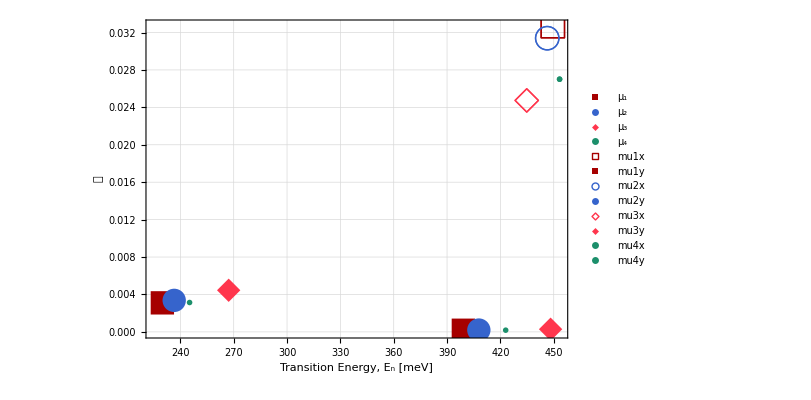
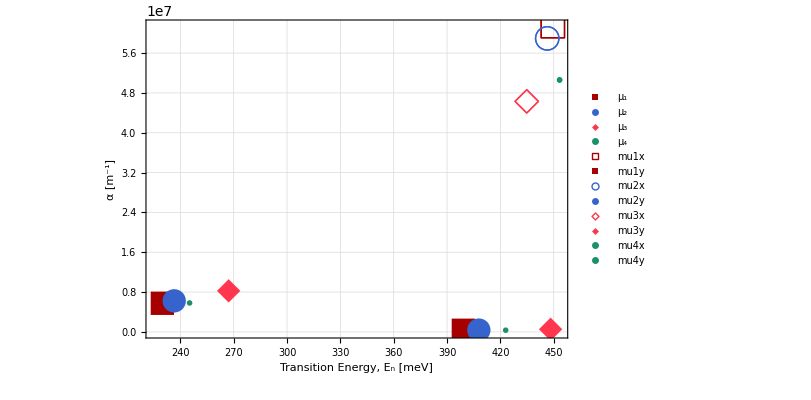
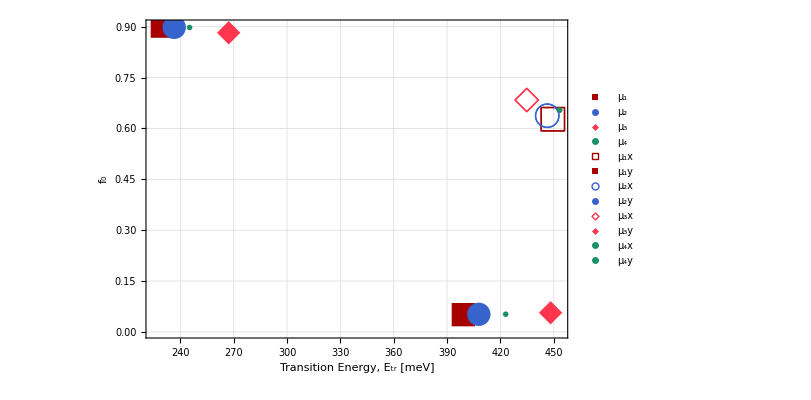
{{{../../figures/comb-dir-fs-afaxy-vs-etr-allmu.pdf,../../figures/plt-dir-fs-afaxy-vs-etr-allmu.pdf,../../figures/leg-dir-fs-afaxy-vs-etr-allmu.pdf}}
-Graphics-,{{../../figures/comb-dir-fs-absxy-vs-etr-allmu.pdf,../../figures/plt-dir-fs-absxy-vs-etr-allmu.pdf,../../figures/leg-dir-fs-absxy-vs-etr-allmu.pdf}}
-Graphics-,{{../../figures/comb-dir-fs-foxy-vs-etr-allmus.pdf,../../figures/plt-dir-fs-foxy-vs-etr-allmus.pdf,../../figures/leg-dir-fs-foxy-vs-etr-allmus.pdf}}
-Graphics-}

```mathematica
{%,%%,%%%}
```

#### SiO_2 substrate

```mathematica
showandexp["dir-ss-foxy-vs-etr-allmus",#]&@dsar[
"ss",
"rk",
KeyMap[<|Table[tssf["mu`1`",i]->tssf["μ_(`1`)",i],{i,4}]|>[#]&]
/*
flatassmerge
/*
(
ListPlot[
Map[Values,#],
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"f_0",None},{"Transition Energy, SubscriptBox[StyleBox[\"E\",FontSlant->\"Italic\"], \"tr\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"[\",FontSlant->\"Italic\"]meV]","SiO_2 Substrate"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.02,0.02}],
Scaled[{0.02,0.02}]
]
}
]&),
"d0",
AssociationThread[
{"x","y"}->{
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
("fox"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1)
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;1)
/*
KeyMap[<|"i4"->{1,0},"i5"->{1,0},"i6"->{1,0},"i10"->{1,1},"i11"->{1,1}|>[#]&],
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
"foy"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;2)
/*
KeyMap[<|"i2"->{0,1},"i4"->{0,3},"i5"->{0,3},"i7"->{0,5},"i8"->{0,5},"i10"->{0,7}|>[#]&]
}
]
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
showandexp["dir-ss-absxy-vs-etr-allmu",#]&@dsar[
"ss","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"α [m^-1]",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","SiO_2 Substrate"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"alphax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5],
"alphay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
showandexp["dir-ss-afaxy-vs-etr-allmu",#]&@dsar[
"ss","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"𝒜",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","SiO_2 Substrate"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"afax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4],
"afay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

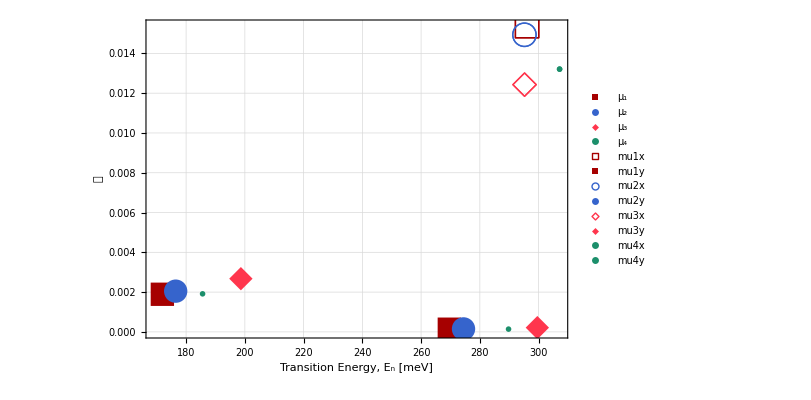
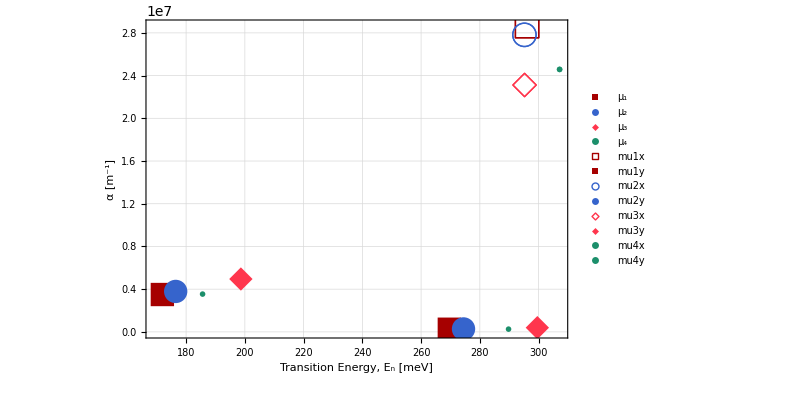
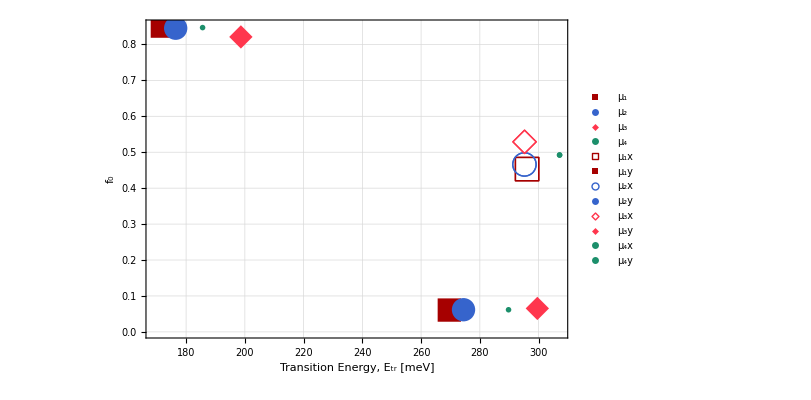
{{{../../figures/comb-dir-ss-afaxy-vs-etr-allmu.pdf,../../figures/plt-dir-ss-afaxy-vs-etr-allmu.pdf,../../figures/leg-dir-ss-afaxy-vs-etr-allmu.pdf}}
-Graphics-,{{../../figures/comb-dir-ss-absxy-vs-etr-allmu.pdf,../../figures/plt-dir-ss-absxy-vs-etr-allmu.pdf,../../figures/leg-dir-ss-absxy-vs-etr-allmu.pdf}}
-Graphics-,{{../../figures/comb-dir-ss-foxy-vs-etr-allmus.pdf,../../figures/plt-dir-ss-foxy-vs-etr-allmus.pdf,../../figures/leg-dir-ss-foxy-vs-etr-allmus.pdf}}
-Graphics-}

```mathematica
{%,%%,%%%}
```

#### h-BN substrate

```mathematica
showandexp["dir-hs-foxy-vs-etr-allmus",#]&@dsar[
"hs",
"rk",
KeyMap[<|Table[tssf["mu`1`",i]->tssf["μ_(`1`)",i],{i,4}]|>[#]&]
/*
flatassmerge
/*
(
ListPlot[
Map[Values,#],
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"f_0",None},{"Transition Energy, SubscriptBox[StyleBox[\"E\",FontSlant->\"Italic\"], \"tr\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"[\",FontSlant->\"Italic\"]meV]","h-BN Substrate"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.02,0.02}],
Scaled[{0.02,0.02}]
]
}
]&),
"d0",
AssociationThread[
{"x","y"}->{
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
("fox"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1)
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;1)
/*
KeyMap[<|"i4"->{1,0},"i5"->{1,0},"i6"->{1,0},"i10"->{1,1},"i11"->{1,1}|>[#]&],
{
("ndeevs"/*QuantityMagnitude/*Abs)/*(#["i1"]-#&),
"foy"/*KeyTake["i1"]/*Values/*Map[KeyMap[StringReplace[#,"j"->"i"]&]]/*(Map[selchop[]])/*1
}
/*
KeyIntersection
/*
Merge[Identity]
/*
(;;2)
/*
KeyMap[<|"i2"->{0,1},"i4"->{0,3},"i5"->{0,3},"i7"->{0,5},"i8"->{0,5},"i10"->{0,7}|>[#]&]
}
]
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
showandexp["dir-hs-absxy-vs-etr-allmu",#]&@dsar[
"hs","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"α [m^-1]",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","h-BN Substrate"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"alphax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5],
"alphay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^5]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

```mathematica
showandexp["dir-hs-afaxy-vs-etr-allmu",#]&@dsar[
"hs","rk",
All
/*
flatassmerge
/*
Map[Values]
(*/*
Map[If[Length[#]==1,Flatten[#],#]&]
/*
Values*)
/*
(
ListPlot[
#,
PlotTheme->"Detailed",
ImageSize->{wx=600,hx=400},
AspectRatio->hx/wx,
PlotStyle->Riffle[randash,randash],
PlotMarkers->Transpose[{Riffle[emmarks4,fullmarks4],Table[24,{8}]}],
FrameLabel->{{"𝒜",None},{"Transition Energy, StyleBox[SubscriptBox[\"E\", \"n\"],FontSlant->\"Italic\"] [meV]","h-BN Substrate"}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Epilog->{
Inset[
PointLegend[
randash[[;;,1]],
Table[tssf["μ_(`1`)",i],{i,4}],
LegendMarkers->Transpose[{fullmarks4,Table[24,{4}]}],
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.05,0.95}],
Scaled[{0.05,0.95}]
]
}
]&),
"d0",
{
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
"afax"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4],
"afay"/*"i1"/*(1;;6)/*KeyMap[StringReplace[#,"j"->"i"]&]/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-4]
}
/*
(AssociationThread[
{"x","y"}->{
Merge[Identity][KeyIntersection[{#[[1]],#[[2]]}]],
Merge[Identity][KeyIntersection[{#[[1]],#[[3]]}]]
}
]&)
];
```

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

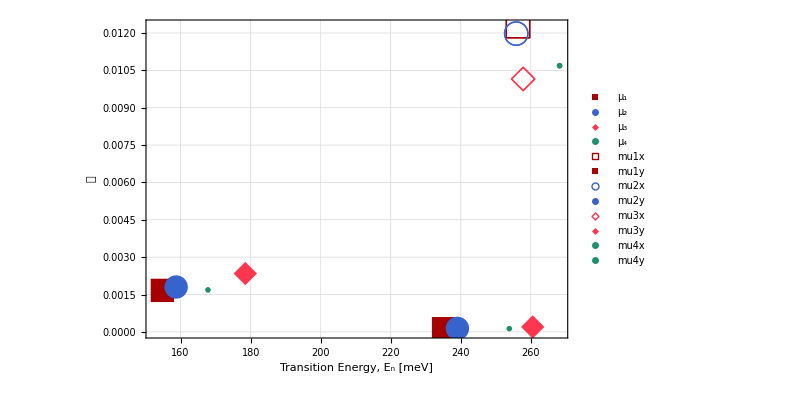
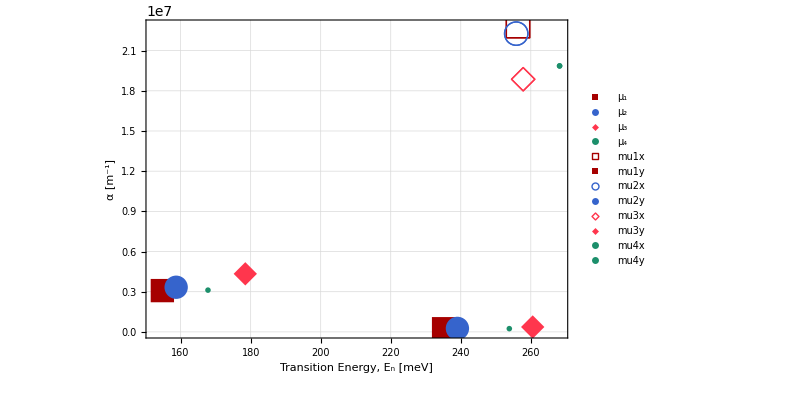
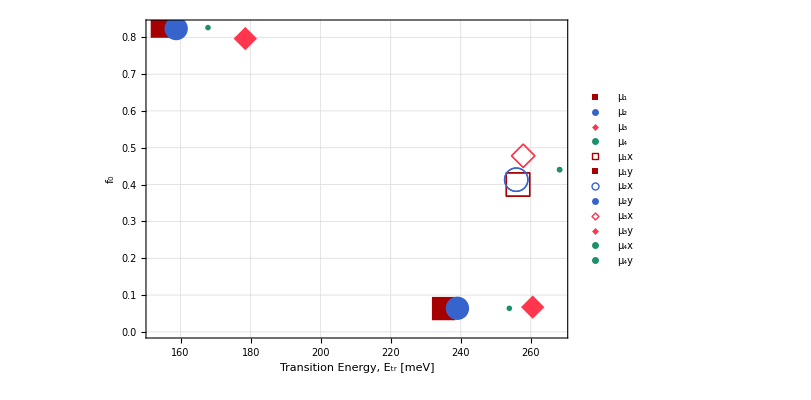
{{{../../figures/comb-dir-hs-afaxy-vs-etr-allmu.pdf,../../figures/plt-dir-hs-afaxy-vs-etr-allmu.pdf,../../figures/leg-dir-hs-afaxy-vs-etr-allmu.pdf}}
-Graphics-,{{../../figures/comb-dir-hs-absxy-vs-etr-allmu.pdf,../../figures/plt-dir-hs-absxy-vs-etr-allmu.pdf,../../figures/leg-dir-hs-absxy-vs-etr-allmu.pdf}}
-Graphics-,{{../../figures/comb-dir-hs-foxy-vs-etr-allmus.pdf,../../figures/plt-dir-hs-foxy-vs-etr-allmus.pdf,../../figures/leg-dir-hs-foxy-vs-etr-allmus.pdf}}
-Graphics-}

```mathematica
{%,%%,%%%}
```

## Back to the drawing board on plotting the optical quantities...

### Adding more points

#### Combine x and y

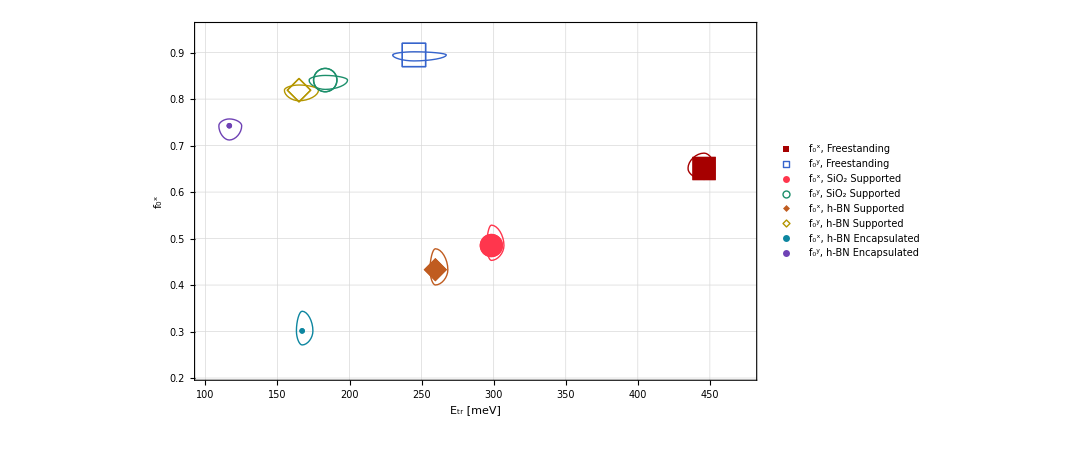

```mathematica
(*showandexp["0626-dir-fox-vs-etr-allmus",#]&@*)
Normal@dsar[
KeyValueMap[
Module[{outkey=#1,inass=#2},
KeyValueMap[{
#1<>", "<>ToString[envleg[outkey]]->{#2}
}&][inass]
]&]
/*
Association
/*
(dslp[
{
FrameLabel->{{"f_0^x",None},{"E_tr [meV]",None}},
PlotRange->{{100,475},{0.21,0.95}},
PlotLegends->Placed[PointLegend[Automatic,
LegendLayout->(
framegrid[
Map[
(TableForm[#,TableDirections->Row,TableAlignments->Left]&),
ArrayReshape[#,{4,2,2}],
{2}
]
]&)
],Above],
"ls"->24,
"mt"->feriff
}
]),
"rk",
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*Map[makeebars]
,
"d0",
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"f_0^x"->#[[1]],"f_0^y"->#[[2]]|>&)
]
```

#### All assocs

```mathematica
dsar[
All,
"rk",
All,
"d0",
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"x"-><|"etr"->#[[1,1]],"f0"->#[[1,2]]|>,"y"-><|"etr"->#[[2,1]],"f0"->#[[2,2]]|>|>&)
]
```

Dataset[<>]

#### f_0^x

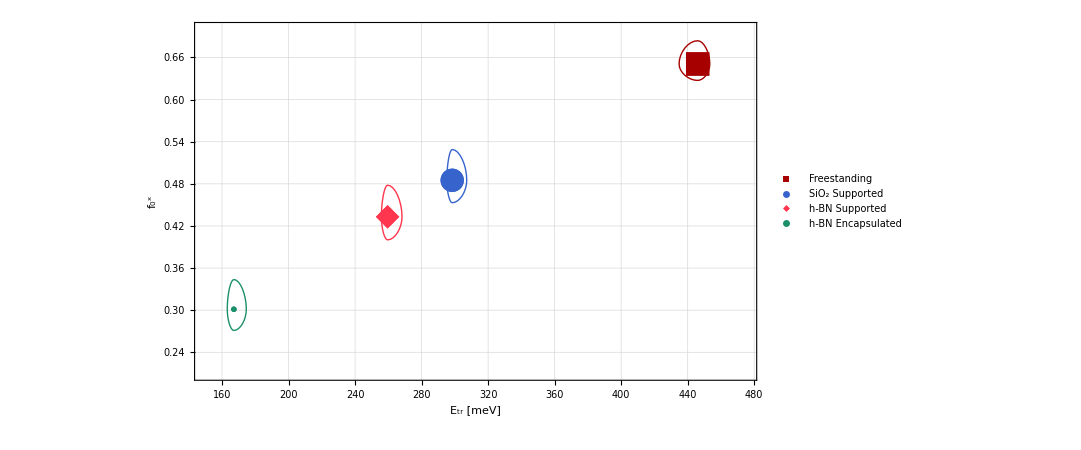
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0626-dir-fox-vs-etr-allmus.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0626-dir-fox-vs-etr-allmus.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0626-dir-fox-vs-etr-allmus.pdf}}
-Graphics-

```mathematica
showandexp["0626-dir-fox-vs-etr-allmus",#]&@
Normal@dsar[
All
/*
KeyMap[envleg[#]&]
/*
(dslp[
{
FrameLabel->{{"f_0^x",None},{"E_tr [meV]",None}},
PlotRange->{{150,475},{0.21,0.7}},
PlotLegends->Placed[PointLegend[Automatic,LegendLayout->{"Row",1}],Above],
"ls"->24
}
]),
"rk",
Values
/*
flatrans
/*
{makeebars}
,
"d0",
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
]
```

```mathematica
Normal@dsar[
All
/*
KeyMap[envleg[#]&],
"rk",
Values
/*
flatrans
/*
{makeebars}
,
"d0",
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
]
```

<|Freestanding→{{446.11.7.,0.6510.0230.033}},SiO_2 Supported→{{298.43.29.,0.4850.0320.04}},h-BN Supported→{{260.4.9.,0.4330.0330.05}},h-BN Encapsulated→{{167.4.7.,0.3010.0300.04}}|>

#### f_0^y

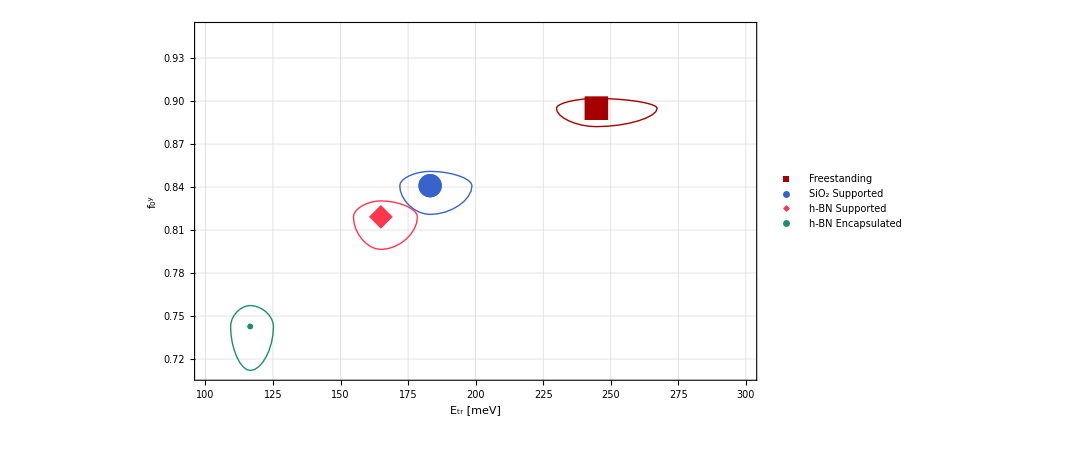
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0626-dir-foy-vs-etr-allmus.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0626-dir-foy-vs-etr-allmus.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0626-dir-foy-vs-etr-allmus.pdf}}
-Graphics-

```mathematica
showandexp["0626-dir-foy-vs-etr-allmus",#]&@
Normal@dsar[
All
/*
KeyMap[envleg[#]&]
/*
(dslp[
{
FrameLabel->{{"f_0^y",None},{"E_tr [meV]",None}},
PlotRange->{{100,300},{0.71,0.95}},
PlotLegends->Placed[PointLegend[Automatic,LegendLayout->{"Row",1}],Above],
"ls"->24
}
]),
"rk",
Values
/*
flatrans
/*
{makeebars}
,
"d0",
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
]
```

### Start small - can I do error bars in both x and y?

Yep!

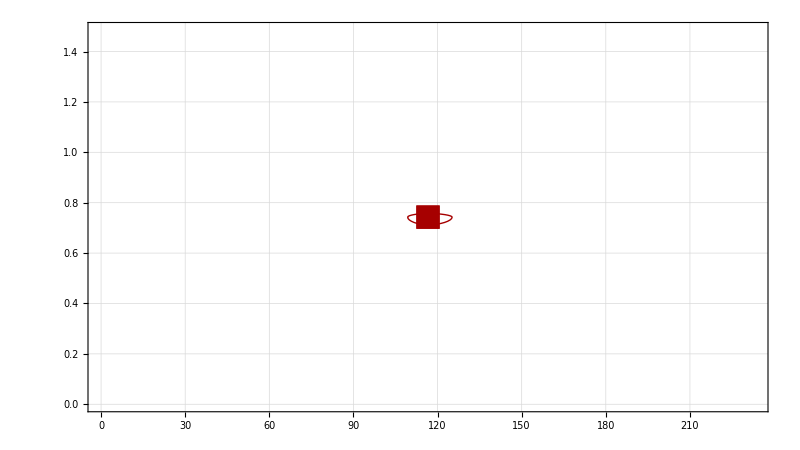

```mathematica
Normal@dsar[
"he",
"rk",
Values
/*
flatrans
/*
{makeebars}
/*
(dslp[]),
"d0",
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
]
```

## Ind

## EVS (n=1-4) for RK/C (all μ)

TODO: Use error “corridors” here too?

### Update w/ error “corridors” (probably going to replace the Figure with only RK)

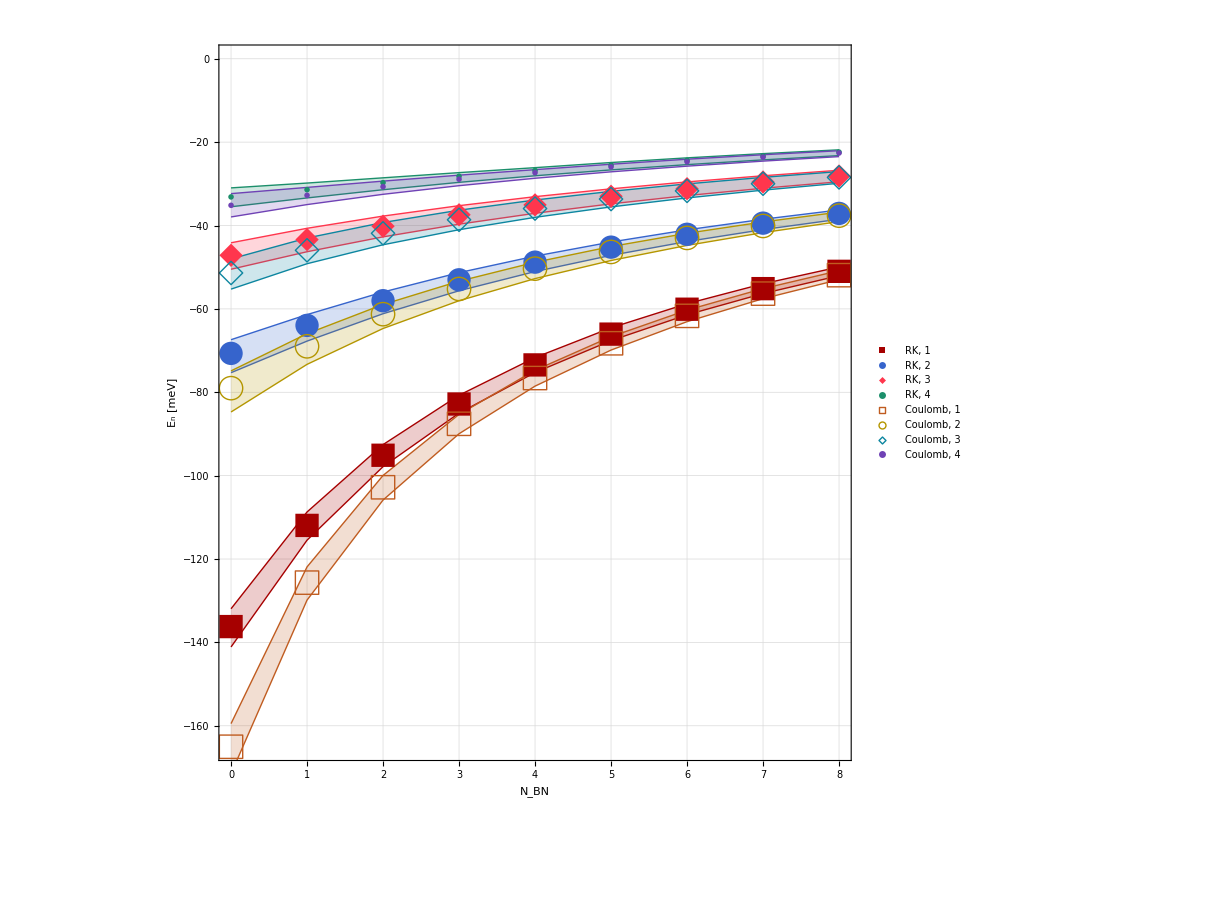
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0628-ind-evs-vs-d-rkc.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0628-ind-evs-vs-d-rkc.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0628-ind-evs-vs-d-rkc.pdf}}
-Graphics-

```mathematica
showandexp["0628-ind-evs-vs-d-rkc",#]&@
Normal@dsar[
"he"(* ENV *),
All (* POT *)
/*
KeyMap[potleg]
/*
KeyValueMap[
Module[{pot=#1,vals=#2},
MapIndexed[
{pot<>tssf["`1`",First[#2]]->#1}&,
vals
]
]&
]
/*
Flatten
/*
Association
/*
(dslp[
{
FrameLabel->{{"E_n [meV]",None},{"N_BN",None}},
IntervalMarkers->"Bands",
"is"->{900,900}
}
]),
Values (* MUS *)
/*
(Flatten[#,{{3},{2},{1},{4}}]&)
/*
(Map[
Module[{nh=#[[1,1]],vals=#[[;;,2]]},
{nh,Around[Mean[vals],{Mean[vals]-Min[vals],Max[vals]-Mean[vals]}]}
]&,
#,
{2}
]&),
(2;;) (* D *)
/*
(KeyValueMap[
Module[{dtox=keytox[#1],vals=#2},
Map[
{dtox,#}&,
vals
]]&,
#
]&),
"ndeevs",
(;;4)/*Values/*QuantityMagnitude
]
```

### Paper figure (as of 6/25)

Values::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

Values::invrl: The argument TypeSystem`UnknownType is not a valid Association or a list of rules.

Keys::invrl: The argument Association[Dataset`Query`PackagePrivate`toop[KeyValueMap[Module[{muky=Slot[«1»],inass=Slot[«1»]},AssociationThread[(«1»&)/@Keys[«1»],Values[inass]]]&]]] is not a valid Association or a list of rules.

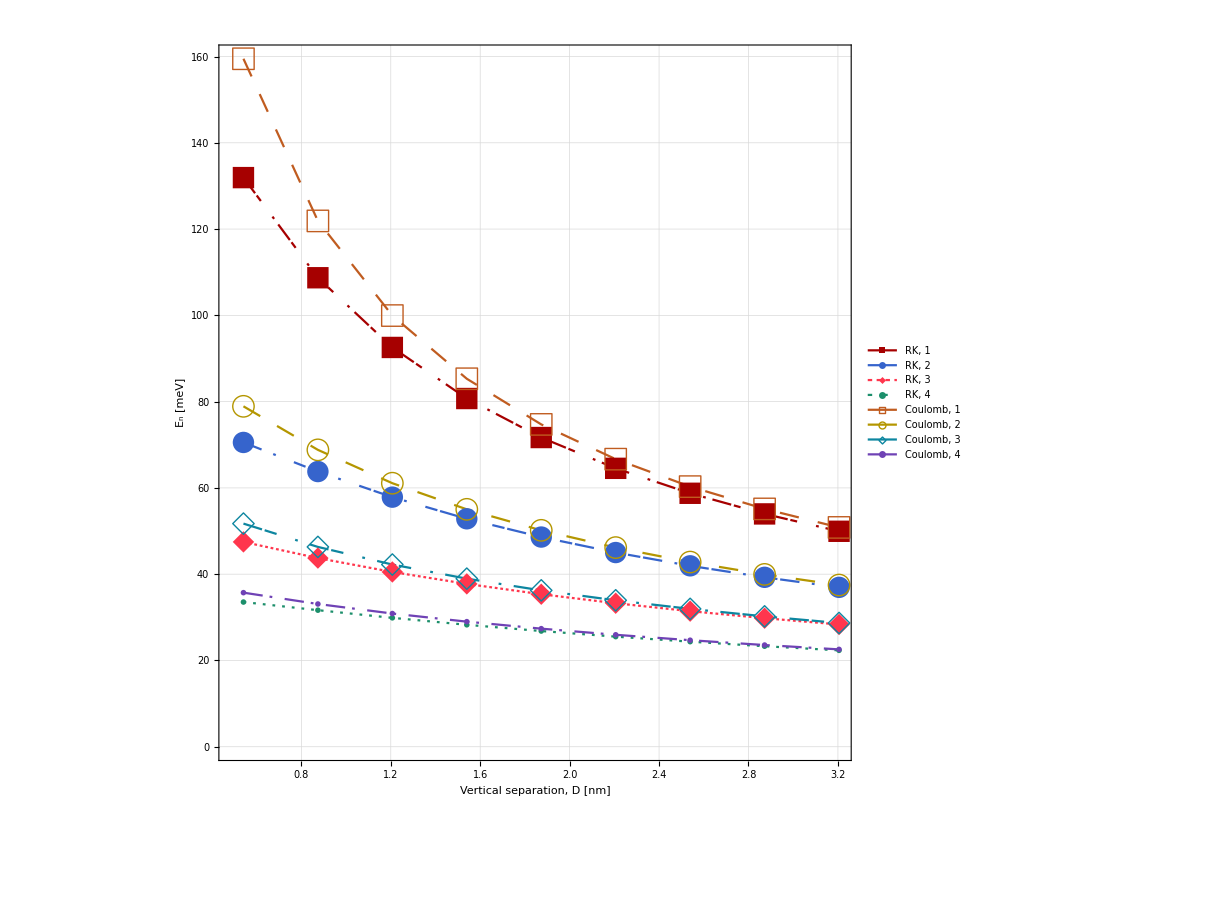

```mathematica
(*showandexp["ind-evs-vs-d-rkc",#]&@*)
dsar[
"he",
All
/*
flatassmerge
/*
KeyMap[
StringReplace[
#,
{
"rk"->"RK, ",
"c"->"Coulomb, ",
"i"->"",
n:DigitCharacter..:>tssf["`1`",n]
}
]&
],
"mu1",
(2;;)
/*
Transpose
/*
Map[
KeyValueMap[
{
QuantityMagnitude[Quantity[rightd[(ToExpression@StringCases[#1,DigitCharacter..])[[1]]-1],"BohrRadius"],"Nanometers"],
Abs@QuantityMagnitude@#2
}&,
#
]&
],
"ndeevs",
(;;4),
QuantityMagnitude/*Abs
][
(
ListLinePlot[
#,
PlotTheme->"Detailed",
PlotStyle->randash,
PlotMarkers->Transpose[{Flatten[{fullmarks4,emmarks4}],Table[22,{8}]}],
GridLinesStyle->Gray,
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["Vertical separation, D [nm]"],None}},
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
IntervalMarkers->"Bands",
ImageSize->{wx=900,hx=900},
AspectRatio->hx/wx,
PlotLegends->Placed[LineLegend[
Automatic,
LegendLayout->{"Column",1}
],
Right]
]
&)
]
```

## E_tr, f_0, α, 𝒜: How to show?

For each quantity, want to examine dependence on N_BN, RK/C
But each quantity has x and y, and I want to do error bars again for the μ_i.
Maybe split graphs for x and y.

### 3D isn’t gonna work

```mathematica
Normal@dsar[
"he",
All (* POT *)
/*
KeyValueMap[
Module[{outkey=#1,outvals=#2},
AssociationThread[
Map[outkey<>#&,Keys[outvals]],
Values[outvals]
]
]&
]
/*
Association
/*
(
ListPointPlot3D[
#,
PlotTheme->"Detailed",
PlotStyle->Flatten[{Darker@LightRed,Lighter[Red],Red,Darker[Red],Darker@LightBlue,Lighter[Blue],Blue,Darker[Blue]}],
Filling->Bottom,
PlotLegends->"Expressions",
ImageSize->{wx=900,hx=900},BoxRatios->{1,1,0.5},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotRange->{Full,Full,{0,1}},
ViewPoint->{-1.5,-1.5,1.5},
Boxed->True,
BoxStyle->Directive[Black,Thick],
FaceGrids->{{1,0,0},{0,1,0},{0,0,-1}},
AxesEdge->Automatic
]&),
All(* MUS *),
(2;;7) (* NBN *)/*
KeyValueMap[
Flatten[{keytox[#1],#2}]&
],
{ (* QUANT *)
ev2etr/*Values,
gsfox/*Values
}
/*
flatrans
/*
selchpy[]
/*
1
]
```

-Graphics3D-

## EVs (n=[1,6]) for RK w/ “corridors”

### Paper figure (6/25)

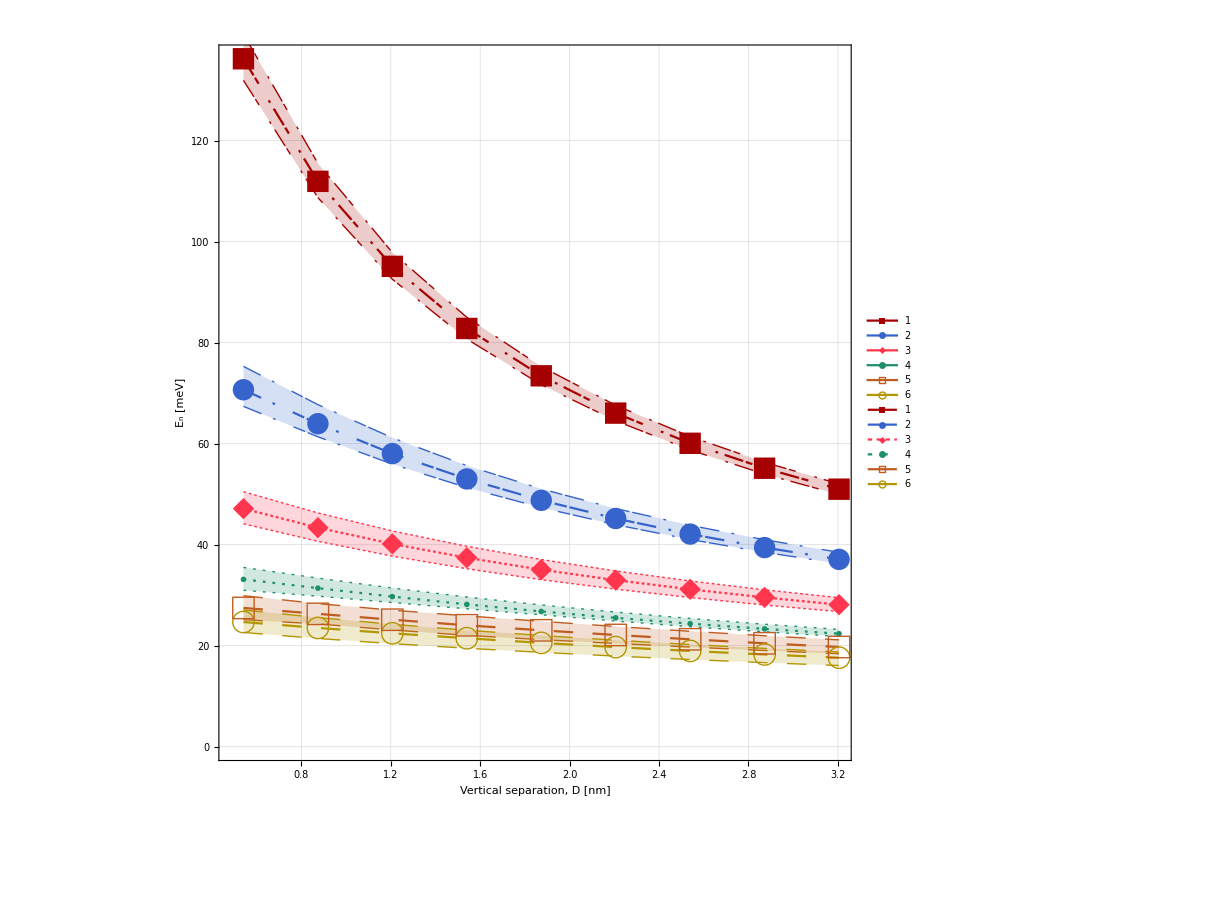

```mathematica
(*showandexp["ind-evs-vs-d-i1to6-bands",#]&@*)
dsar["he","rk",
All,
(2;;)
/*
Transpose
/*
Map[
KeyValueMap[
{
QuantityMagnitude[Quantity[rightd[(ToExpression@StringCases[#1,DigitCharacter..])[[1]]-1],"BohrRadius"],"Nanometers"],
Abs@QuantityMagnitude@#2
}&,
#
]&
]
(*/*
Transpose*),
"ndeevs",
;;6
][
Transpose
][
;;
/*
KeyMap[tssf["`1`",StringCases[#,DigitCharacter..][[1]]]&]
/*
(
ListLinePlot[
#,
PlotTheme->"Detailed",
PlotStyle->randash,
PlotMarkers->Transpose[{Flatten[{fullmarks4,emmarks4}],Table[22,{8}]}],
GridLinesStyle->Gray,
FrameLabel->{{TraditionalForm["E_n [meV]"],None},{TraditionalForm["Vertical separation, D [nm]"],None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
IntervalMarkers->"Bands",
ImageSize->{wx=900,hx=900},
AspectRatio->hx/wx,
Epilog->Inset[
LineLegend[
randash[[;;,1]],
TraditionalForm/@Keys[#],
LegendMarkers->Transpose[{Flatten[{fullmarks4,emmarks4}],Table[24,{8}]}],
LegendMarkerSize->{75,24},
LegendLayout->{"Column",1},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
Background->White
],
Scaled[{0.98,0.98}],
Scaled[{0.98,0.98}]
]
]
&),
Values
/*
Transpose
/*
Map[
{#[[1,1]],makeebars[{#[[;;,2]]}][[1]]}&
]
]
```

## E_tr vs. D for RK/C

### New Paper figure with error bars (06/29)

```mathematica
(*showandexp["0628-ind-etrs-vs-d-rkc",#]&@*)
Normal@dsar[
"he"(* ENV *),
All (* POT *)
/*
KeyMap[potleg]
/*
KeyValueMap[
Module[{pot=#1,vals=#2},
MapIndexed[
{pot<>tssf["`1`",First[#2]]->#1}&,
vals
]
]&
]
/*
Flatten
/*
Association
(*/*
(dslp[
{
FrameLabel->{{"E_n [meV]",None},{"N_BN",None}},
IntervalMarkers->"Bands",
"is"->{900,900}
}
])*),
Values (* MUS *)
/*
(Flatten[#,{{3},{2},{1},{4}}]&)
/*
(Map[
Module[{nh=#[[1,1]],vals=#[[;;,2]]},
{nh,Around[Mean[vals],{Mean[vals]-Min[vals],Max[vals]-Mean[vals]}]}
]&,
#,
{2}
]&),
(2;;) (* D *)
/*
(KeyValueMap[
Module[{dtox=keytox[#1],vals=#2},
Map[
{dtox,#}&,
vals
]]&,
#
]&),
ev2etr/*Values,
(;;4)
]
```

<|RK, 1→{{0,0.},{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.}},RK, 2→{{0,66.4.6.},{1,48.03.15.},{2,37.12.44.},{3,29.81.93.3},{4,24.71.62.8},{5,20.91.32.4},{6,18.01.22.1},{7,15.71.01.8},{8,13.90.91.6}},RK, 3→{{0,89.5.6.},{1,69.4.5.},{2,54.92.94.},{3,45.42.44.},{4,38.42.13.3},{5,33.11.82.9},{6,28.91.62.7},{7,25.61.42.4},{8,22.91.32.2}},RK, 4→{{0,103.5.5.},{1,80.53.54.},{2,65.42.73.0},{3,54.62.22.4},{4,46.71.82.0},{5,40.51.51.7},{6,35.71.31.4},{7,31.81.11.2},{8,28.61.01.1}},Coulomb, 1→{{0,0.},{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.}},Coulomb, 2→{{0,86.5.8.},{1,57.4.6.},{2,41.52.74.},{3,32.32.13.5},{4,26.21.72.9},{5,21.91.42.5},{6,18.71.22.2},{7,16.21.01.9},{8,14.30.91.7}},Coulomb, 3→{{0,114.6.7.},{1,80.4.6.},{2,60.93.25.},{3,48.92.64.},{4,40.72.23.5},{5,34.61.93.1},{6,30.01.62.7},{7,26.41.52.5},{8,23.51.32.2}},Coulomb, 4→{{0,130.6.6.},{1,93.4.5.},{2,72.13.03.4},{3,58.72.42.6},{4,49.31.92.1},{5,42.31.61.8},{6,37.01.41.5},{7,32.71.21.3},{8,29.31.01.1}}|>

### Paper figure (as of 6/25)

```mathematica
(*showandexp["ind-rkc-etr-vs-d-mu1",#]&@*)
dsar[
"he",
All
/*
KeyMap[<|"rk"->"RK, ","c"->"Coulomb, "|>[#]&]
/*
KeyValueMap[
Module[{key=#1,vals=#2},
<|
key<>"E_tr^x"->vals[[;;,1]],
key<>"E_tr^y"->vals[[;;,2]]
|>
]&
]
/*
Merge[Identity]
/*
Map[Flatten[#,1]&]
/*
dslp[{{"E_tr [meV]",None},{"Interlayer separation, D [nm]",None}},{24,24,{800,450}}][],
"mu1",
(2;;)/*Values,
{
"ndeparams"/*"dval"/*(QuantityMagnitude[Quantity[#,"BohrRadius"],"Nanometers"]&),
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
(*"f_0^x"->*)"fox"/*"i1"/*selchop[10^-4]/*KeyMap[StringReplace[#,"j"->"i"]&],
(*"f_0^y"->*)"foy"/*"i1"/*selchop[10^-4]/*KeyMap[StringReplace[#,"j"->"i"]&]
}
/*
(
Module[
{d=#[[1]],etrs=#[[2]],fox=#[[3]],foy=#[[4]],redetrx,redetry},
redetrx=First@Merge[KeyIntersection[{etrs,fox}],{d,#[[1]]}&];
redetry=First@Merge[KeyIntersection[{etrs,foy}],{d,#[[1]]}&];
{redetrx,redetry}
]&)
]
```

## f_0 vs. D, RK/C

### Paper figure (6/25)

```mathematica
(*showandexp["ind-rkc-f0-vs-d-mu1",#]&@*)
dsar[
"he",
All
/*
KeyMap[<|"rk"->"RK, ","c"->"Coulomb, "|>[#]&]
/*
KeyValueMap[
Module[{key=#1,vals=#2},
<|
key<>"f_0^x"->vals[[;;,1]],
key<>"f_0^y"->vals[[;;,2]]
|>
]&
]
/*
Merge[Identity]
/*
Map[Flatten[#,1]&]
/*
dslp[{{"f_0",None},{"Interlayer separation, D [nm]",None}},{24,24,0.75*{800,450}}][],
"mu1",
(2;;)/*Values,
{
"ndeparams"/*"dval"/*(QuantityMagnitude[Quantity[#,"BohrRadius"],"Nanometers"]&),
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
(*"f_0^x"->*)"fox"/*"i1"/*selchop[10^-4]/*KeyMap[StringReplace[#,"j"->"i"]&],
(*"f_0^y"->*)"foy"/*"i1"/*selchop[10^-4]/*KeyMap[StringReplace[#,"j"->"i"]&]
}
/*
(
Module[
{d=#[[1]],etrs=#[[2]],fox=#[[3]],foy=#[[4]],redfox,redfoy},
redfox=First@Merge[KeyIntersection[{etrs,fox}],{d,#[[2]]}&];
redfoy=First@Merge[KeyIntersection[{etrs,foy}],{d,#[[2]]}&];
{redfox,redfoy}
]&)
]
```

dslp[{{f_0,None},{Interlayer separation, D [nm],None}},{24,24,{600.,337.5}}][][<|RK, f_0^x→{{0.541,0.430324},{0.874,0.523207},{1.207,0.602967},{1.54,0.671439},{1.873,0.728643},{2.206,0.773409},{2.539,0.804282},{2.872,0.820207},{3.205,0.820911}},RK, f_0^y→{{0.541,0.891879},{0.874,0.925688},{1.207,0.94435},{1.54,0.955975},{1.873,0.963901},{2.206,0.969695},{2.539,0.974182},{2.872,0.977844},{3.205,0.980973}},Coulomb, f_0^x→{{0.541,0.36318},{0.874,0.478765},{1.207,0.571012},{1.54,0.647927},{1.873,0.711847},{2.206,0.762405},{2.539,0.798365},{2.872,0.818666},{3.205,0.822983}},Coulomb, f_0^y→{{0.541,0.870017},{0.874,0.916882},{1.207,0.939858},{1.54,0.953338},{1.873,0.962195},{2.206,0.968502},{2.539,0.973295},{2.872,0.977147},{3.205,0.980396}}|>]

## f_0 vs. E_tr (individual N_BN plots - figures REPLACED as of 07/07)

#### N_BN=0

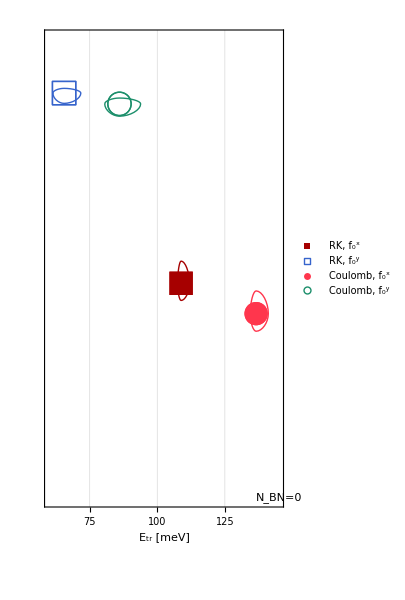
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0628-ind-foxy-allmus-rkc-nbn0.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0628-ind-foxy-allmus-rkc-nbn0.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0628-ind-foxy-allmus-rkc-nbn0.pdf}}
-Graphics-

```mathematica
showandexp["0628-ind-foxy-allmus-rkc-nbn0",#]&@
Normal@dsar[
"he",
All
/*
KeyMap[potleg]
/*
flasme
/*
Merge[Identity]
/*
(dslp[
{
FrameLabel->{{(*"f_0"*)None,None},{"E_tr [meV]",None}},
FrameTicks->{{None,None},{Automatic,None}},
PlotRange->{{60,145},{0,1}},
PlotLegends->Placed[PointLegend[Automatic,
LegendLayout->{"Row",1}
],Above],
Epilog->{
Inset[
Framed[
Style["N_BN=0",24,Black,FontFamily->"Arial"],
FrameStyle->None,Background->White
],
Scaled[{0.98,0.02}],
Scaled[{0.98,0.02}]
]
},
"ls"->24,
"mt"->feriff,
"is"->{150,300}*2
}
]),
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*
Map[makeebars]
,
"d1",
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"f_0^x"->#[[1]],"f_0^y"->#[[2]]|>&)
]
```

#### N_BN=1

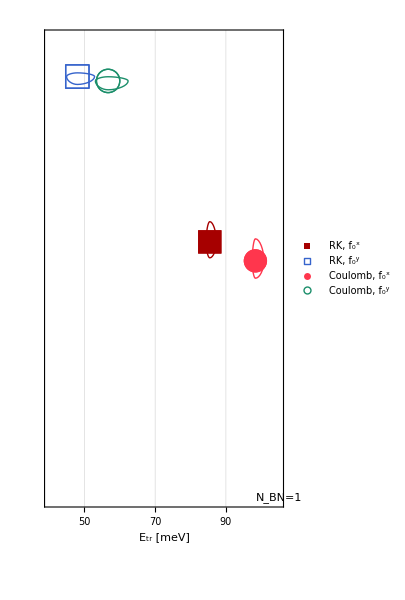
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0628-ind-foxy-allmus-rkc-nbn1.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0628-ind-foxy-allmus-rkc-nbn1.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0628-ind-foxy-allmus-rkc-nbn1.pdf}}
-Graphics-

```mathematica
showandexp["0628-ind-foxy-allmus-rkc-nbn1",#]&@
Normal@dsar[
"he",
All
/*
KeyMap[potleg]
/*
flasme
/*
Merge[Identity]
/*
(dslp[
{
FrameLabel->{{None,None},{"E_tr [meV]",None}},
FrameTicks->{{None,None},{{50,70,90},None}},
PlotRange->{{40,105},{0,1}},
PlotLegends->Placed[PointLegend[Automatic,
LegendLayout->{"Row",1}
],Above],
Epilog->{
Inset[
Framed[
Style["N_BN=1",24,Black,FontFamily->"Arial"],
FrameStyle->None,Background->White
],
Scaled[{0.98,0.02}],
Scaled[{0.98,0.02}]
]
},
"ls"->24,
"mt"->feriff,
"is"->{150,300}*2
}
]),
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*
Map[makeebars]
,
"d2",
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"f_0^x"->#[[1]],"f_0^y"->#[[2]]|>&)
]
```

#### N_BN=2

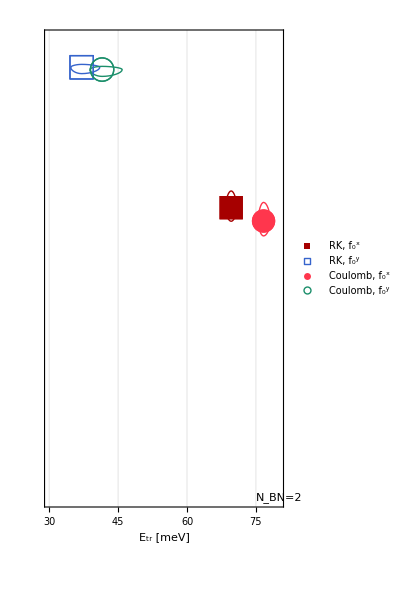
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0628-ind-foxy-allmus-rkc-nbn2.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0628-ind-foxy-allmus-rkc-nbn2.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0628-ind-foxy-allmus-rkc-nbn2.pdf}}
-Graphics-

```mathematica
showandexp["0628-ind-foxy-allmus-rkc-nbn2",#]&@
Normal@dsar[
"he",
All
/*
KeyMap[potleg]
/*
flasme
/*
Merge[Identity]
/*
(dslp[
{
FrameLabel->{{None,None},{"E_tr [meV]",None}},
FrameTicks->{{None,None},{Automatic,None}},
PlotRange->{{30,80},{0,1}},
PlotLegends->Placed[PointLegend[Automatic,
LegendLayout->{"Row",1}
],Above],
Epilog->{
Inset[
Framed[
Style["N_BN=2",24,Black,FontFamily->"Arial"],
FrameStyle->None,Background->White
],
Scaled[{0.98,0.02}],
Scaled[{0.98,0.02}]
]
},
"ls"->24,
"mt"->feriff,
"is"->{150,300}*2
}
]),
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*
Map[makeebars]
,
"d3",
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"f_0^x"->#[[1]],"f_0^y"->#[[2]]|>&)
]
```

#### N_BN=3

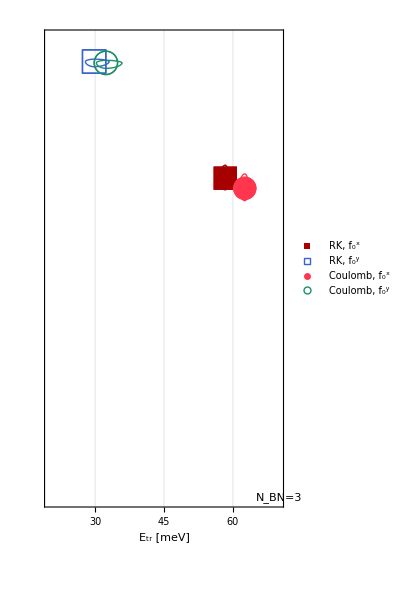
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0628-ind-foxy-allmus-rkc-nbn3.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0628-ind-foxy-allmus-rkc-nbn3.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0628-ind-foxy-allmus-rkc-nbn3.pdf}}
-Graphics-

```mathematica
showandexp["0628-ind-foxy-allmus-rkc-nbn3",#]&@
Normal@dsar[
"he",
All
/*
KeyMap[potleg]
/*
flasme
/*
Merge[Identity]
/*
(dslp[
{
FrameLabel->{{None,None},{"E_tr [meV]",None}},
FrameTicks->{{None,None},{Automatic,None}},
PlotRange->{{20,70},{0,1}},
PlotLegends->Placed[PointLegend[Automatic,
LegendLayout->{"Row",1}
],Above],
Epilog->{
Inset[
Framed[
Style["N_BN=3",24,Black,FontFamily->"Arial"],
FrameStyle->None,Background->White
],
Scaled[{0.98,0.02}],
Scaled[{0.98,0.02}]
]
},
"ls"->24,
"mt"->feriff,
"is"->{150,300}*2
}
]),
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*
Map[makeebars]
,
"d4",
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"f_0^x"->#[[1]],"f_0^y"->#[[2]]|>&)
]
```

#### N_BN=4

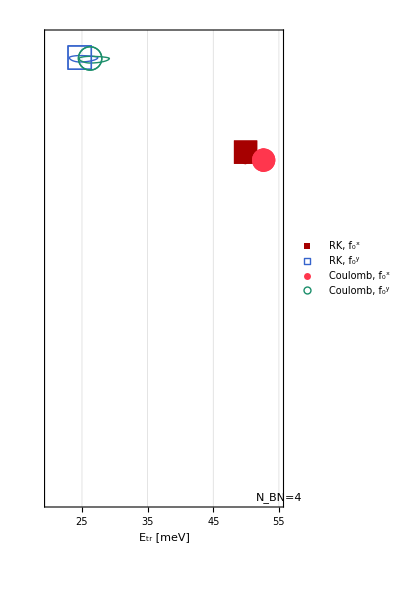
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0628-ind-foxy-allmus-rkc-nbn4.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0628-ind-foxy-allmus-rkc-nbn4.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0628-ind-foxy-allmus-rkc-nbn4.pdf}}
-Graphics-

```mathematica
showandexp["0628-ind-foxy-allmus-rkc-nbn4",#]&@
Normal@dsar[
"he",
All
/*
KeyMap[potleg]
/*
flasme
/*
Merge[Identity]
/*
(dslp[
{
FrameLabel->{{None,None},{"E_tr [meV]",None}},
FrameTicks->{{None,None},{{25,35,45,55},None}},
PlotRange->{{20,55},{0,1}},
PlotLegends->Placed[PointLegend[Automatic,
LegendLayout->{"Row",1}
],Above],
Epilog->{
Inset[
Framed[
Style["N_BN=4",24,Black,FontFamily->"Arial"],
FrameStyle->None,Background->White
],
Scaled[{0.98,0.02}],
Scaled[{0.98,0.02}]
]
},
"ls"->24,
"mt"->feriff,
"is"->{150,300}*2
}
]),
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*
Map[makeebars]
,
"d5",
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"f_0^x"->#[[1]],"f_0^y"->#[[2]]|>&)
]
```

#### N_BN=5

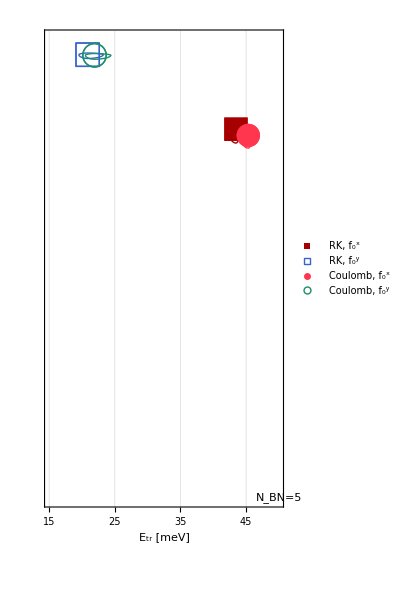
{{~/datadrop/Dropbox/Berman-Research/dis/figs/phos-comb-0628-ind-foxy-allmus-rkc-nbn5.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-plt-0628-ind-foxy-allmus-rkc-nbn5.pdf,~/datadrop/Dropbox/Berman-Research/dis/figs/phos-leg-0628-ind-foxy-allmus-rkc-nbn5.pdf}}
-Graphics-

```mathematica
showandexp["0628-ind-foxy-allmus-rkc-nbn5",#]&@
Normal@dsar[
"he",
All
/*
KeyMap[potleg]
/*
flasme
/*
Merge[Identity]
/*
(dslpe[
{
FrameLabel->{{None,None},{"E_tr [meV]",None}},
FrameTicks->{{None,None},{{15,25,35,45},None}},
PlotRange->{{15,50},{0,1}},
PlotLegends->Placed[PointLegend[Automatic,
LegendLayout->{"Row",1}
],Above],
Epilog->{
Inset[
Framed[
Style["N_BN=5",24,Black,FontFamily->"Arial"],
FrameStyle->None,Background->White
],
Scaled[{0.98,0.02}],
Scaled[{0.98,0.02}]
]
},
"ls"->24,
"mt"->feriff,
"is"->{150,300}*2
}
]),
All
/*
Values
/*
Transpose
/*
Map[Transpose]
/*
Map[makeebars]
,
"d6",
{
{
ev2etr/*(;;6)/*Values,
gsfox/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1,
{
ev2etr/*(;;6)/*Values,
gsfoy/*(;;6)/*Values
}
/*
flatrans
/*
selchpy[]/*1
}
/*
(<|"f_0^x"->#[[1]],"f_0^y"->#[[2]]|>&)
]
```

## α vs. D, RK/C

### Paper figure (6/25)

```mathematica
(*showandexp["ind-rkc-abs-vs-d-mu1",#]&@*)
dsar[
"he",
All
/*
KeyMap[<|"rk"->"RK, ","c"->"Coulomb, "|>[#]&]
/*
KeyValueMap[
Module[{key=#1,vals=#2},
<|
key<>"α^x"->vals[[;;,1]],
key<>"α^y"->vals[[;;,2]]
|>
]&
]
/*
Merge[Identity]
/*
Map[Flatten[#,1]&]
/*
dslp[{{"α [m^-1]",None},{"Interlayer separation, D [nm]",None}},{24,24,0.75*{800,450}}][],
"mu1",
(2;;)/*Values,
{
"ndeparams"/*"dval"/*(QuantityMagnitude[Quantity[#,"BohrRadius"],"Nanometers"]&),
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
(*"f_0^x"->*)"alphax"/*"i1"/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^4]/*KeyMap[StringReplace[#,"j"->"i"]&],
(*"f_0^y"->*)"alphay"/*"i1"/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^4]/*KeyMap[StringReplace[#,"j"->"i"]&]
}
/*
(
Module[
{d=#[[1]],etrs=#[[2]],fox=#[[3]],foy=#[[4]],redfox,redfoy},
redfox=First@Merge[KeyIntersection[{etrs,fox}],{d,#[[2]]}&];
redfoy=First@Merge[KeyIntersection[{etrs,foy}],{d,#[[2]]}&];
{redfox,redfoy}
]&)
]
```

## 𝒜 vs. D, RK/C

### Paper figure (6/25)

```mathematica
(*showandexp["ind-rkc-afac-vs-d-mu1",#]&@*)
dsar[
"he",
All
/*
KeyMap[<|"rk"->"RK, ","c"->"Coulomb, "|>[#]&]
/*
KeyValueMap[
Module[{key=#1,vals=#2},
<|
key<>"𝒜^x"->vals[[;;,1]],
key<>"𝒜^y"->vals[[;;,2]]
|>
]&
]
/*
Merge[Identity]
/*
Map[Flatten[#,1]&]
/*
dslp[{{"𝒜",None},{"Interlayer separation, D [nm]",None}},{24,24,0.75*{800,450}}][],
"mu1",
(2;;)/*Values,
{
"ndeparams"/*"dval"/*(QuantityMagnitude[Quantity[#,"BohrRadius"],"Nanometers"]&),
"ndeevs"/*QuantityMagnitude/*Abs/*(#["i1"]-#&),
(*"f_0^x"->*)"afax"/*"i1"/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-3]/*KeyMap[StringReplace[#,"j"->"i"]&],
(*"f_0^y"->*)"afay"/*"i1"/*Map[#[10^15,10^13]&]/*QuantityMagnitude/*selchop[10^-3]/*KeyMap[StringReplace[#,"j"->"i"]&]
}
/*
(
Module[
{d=#[[1]],etrs=#[[2]],fox=#[[3]],foy=#[[4]],redfox,redfoy},
redfox=First@Merge[KeyIntersection[{etrs,fox}],{d,#[[2]]}&];
redfoy=First@Merge[KeyIntersection[{etrs,foy}],{d,#[[2]]}&];
{redfox,redfoy}
]&)
]
```

# Scrap paper

### Double checking calcs from TMDC and Xene papers because you can never be too careful? (AKA i might be an idiot)

```mathematica
Tcalgiven=(Quantity[#*10^6,"Meters"^(-1)]&/@{82.29,144.01,70.38,80.8,99.55,152.65,80.21,144.38})
Tmusgiven={0.16,0.28,0.27,0.31,0.15,0.23,0.15,0.27};
Tlmlgiven=(Quantity[#,"Angstroms"]&/@{6.18,6.18,6.527,6.527,6.219,6.219,6.575,6.575});
Tnxgiven=Quantity[5*10^15,"Meters"^(-2)];
Tgamgiven=Quantity[10^13,"Seconds"^(-1)];
Tcalconsts=(Pi*(Quantity["ElementaryCharge"]^2))/(2*Quantity["ElectricConstant"]*Quantity["SpeedOfLight"]*Sqrt[4.89]*Quantity["ElectronMass"])
```

{8.229×10^7 per meter,1.4401×10^8 per meter,7.038×10^7 per meter,8.08×10^7 per meter,9.955×10^7 per meter,1.5265×10^8 per meter,8.021×10^7 per meter,1.4438×10^8 per meter}

0.710339 e^2/(m_e ε_0 c)

Recalculate C_α and make sure it matches what was published

```mathematica
Transpose[{Table[UnitConvert[Tcalconsts*Tnxgiven/(Tgamgiven*(2*Tlmlgiven[[i]])*Tmusgiven[[i]]),"Meters"^(-1)],{i,8}],
Tcalgiven}];
LightRed~bg~({%[[;;,1]],%[[;;,2]],(%[[;;,2]]/%[[;;,1]])}//Transpose//TableForm)
```

1.9066×10^7 per meter | 8.229×10^7 per meter | 4.31606
1.08948×10^7 per meter | 1.4401×10^8 per meter | 13.2182
1.06977×10^7 per meter | 7.038×10^7 per meter | 6.57899
9.31735×10^6 per meter | 8.08×10^7 per meter | 8.67199
2.02095×10^7 per meter | 9.955×10^7 per meter | 4.9259
1.31801×10^7 per meter | 1.5265×10^8 per meter | 11.5818
1.91153×10^7 per meter | 8.021×10^7 per meter | 4.19612
1.06196×10^7 per meter | 1.4438×10^8 per meter | 13.5956

Yeah so this is bad.

3.8132×10^7 per meter | 8.229×10^7 per meter | 2.15803
2.17897×10^7 per meter | 1.4401×10^8 per meter | 6.60909
2.13954×10^7 per meter | 7.038×10^7 per meter | 3.28949
1.86347×10^7 per meter | 8.08×10^7 per meter | 4.336
4.0419×10^7 per meter | 9.955×10^7 per meter | 2.46295
2.63602×10^7 per meter | 1.5265×10^8 per meter | 5.79092
3.82306×10^7 per meter | 8.021×10^7 per meter | 2.09806
2.12392×10^7 per meter | 1.4438×10^8 per meter | 6.79781

### Calculate α & 𝒜 scale factor!

```mathematica
lpm=UnitConvert[Quantity[lphos,"BohrRadius"],"Meters"]
n0m=Quantity[n0,"Meters"^(-2)]
g0s=Quantity[gam0,"Seconds"^(-1)]
```

5.41×10^-10 m

5000000000000000 per meter^2

10000000000000 per second

```mathematica
LightOrange~bg~(cal=UnitConvert[(Pi*Quantity["ElementaryCharge"]^2)/(Quantity["SpeedOfLight"]*Quantity["ElectronMass"]*Quantity["ElectricConstant"]),("Meters"^2)/"Seconds"])//ScientificForm
{LightPink~bg~(cad=Table[UnitConvert[cal*(1/(Sqrt[eps]*lpm)),"Meters"/"Seconds"],{eps,{1,2.4,2.945,4.89}}])//ScientificForm,
LightPurple~bg~(cai=cal*(1/(Sqrt[4.89]*2*lpm)))//ScientificForm}
{LightPink~bg~(ctad=MapIndexed[cad[[First[#2]]]*(n0m/Quantity[#1,"Seconds"^(-1)])&,{10^14,10^14,10^14,10^13}])//ScientificForm,
LightPurple~bg~(ctai=cai*(n0m/g0s))//ScientificForm}
{LightCyan~bg~(ctad*lpm),LightGreen~bg~(ctai*2*lpm)}//ScientificForm
```

3.33512467×10^-5 m^2/s

{{6.16474×10^4 m/s,3.97932×10^4 m/s,3.5923×10^4 m/s,2.78779×10^4 m/s},1.3939×10^4 m/s}

{{3.08237×10^6 per meter,1.98966×10^6 per meter,1.79615×10^6 per meter,1.3939×10^7 per meter},6.96948×10^6 per meter}

{{1.66756×10^-3,1.07641×10^-3,9.71716×10^-4,7.54098×10^-3},7.54098×10^-3}

### ρ_0

```mathematica
2*Pi*0.41/4.89
```

0.526811

### Γ

```mathematica
UnitConvert[Quantity[150,"Millielectronvolts"]/HB,"Seconds"^-1]//N
UnitConvert[Quantity[100,"Millielectronvolts"]/HB,"Seconds"^-1]//N
UnitConvert[Quantity[70,"Millielectronvolts"]/HB,"Seconds"^-1]//N
UnitConvert[Quantity[30,"Millielectronvolts"]/HB,"Seconds"^-1]//N
UnitConvert[Quantity[11,"Millielectronvolts"]/HB,"Seconds"^-1]//N
```

2.2789×10^14 per second

1.51927×10^14 per second

1.06349×10^14 per second

4.5578×10^13 per second

1.67119×10^13 per second

```mathematica
LightBlue~bg~UnitConvert[(Pi*(Quantity["ElementaryCharge"]^2))/(CC*Quantity["ElectronMass"]*Quantity["ElectricConstant"]),("Meters"^2)/"Seconds"]
```

0.0000333512467 m^2/s

```mathematica
{LightGreen~bg~(4*(Pi^2))/QuantityMagnitude[CC,"BohrRadius"/"AtomicUnitOfTime"]//N,LightGreen~bg~Quantity[(4*(Pi^2))/QuantityMagnitude[CC,"BohrRadius"/"AtomicUnitOfTime"],("BohrRadius"^2)/"AtomicUnitOfTime"],LightBlue~bg~UnitConvert[Quantity[(4*(Pi^2))/QuantityMagnitude[CC,"BohrRadius"/"AtomicUnitOfTime"],("BohrRadius"^2)/"AtomicUnitOfTime"],("Meters"^2)/"Seconds"]}
```

{0.288088,0.288087932 a_0^2/atomic unit,0.0000333512589 m^2/s}

```mathematica
{LightOrange~bg~(4*(Pi^2))/137//N,LightOrange~bg~Quantity[(4*(Pi^2))/137,("BohrRadius"^2)/"AtomicUnitOfTime"],LightMagenta~bg~UnitConvert[Quantity[(4*(Pi^2))/137,("BohrRadius"^2)/"AtomicUnitOfTime"],("Meters"^2)/"Seconds"]}
```

{0.288164,(4 π^2)/137 a_0^2/atomic unit,0.0000333600225 m^2/s}

```mathematica
cal=UnitConvert[(Pi*(Quantity["ElementaryCharge"]^2))/(CC*Quantity["ElectronMass"]*Quantity["ElectricConstant"]),("Meters"^2)/"Seconds"];
lpd=Quantity[lphos,"BohrRadius"]
{(3.8+1)/2,(4.89+1)/2}
```

10.2234 a_0

{2.4,2.945}

```mathematica
(ScientificForm@(cal/(Sqrt[#]*lpd))&)/@{1,2.4,2.945,4.89}
LightOrange~bg~((ScientificForm@(50*cal/(Sqrt[#]*lpd))&)/@{1,2.4,2.945,4.89})
(cal/(Sqrt[4.89]*2*lpd))
LightOrange~bg~(500*cal/(Sqrt[4.89]*2*lpd))
```

{6.16474×10^4 m/s,3.97932×10^4 m/s,3.5923×10^4 m/s,2.78779×10^4 m/s}

{3.08237×10^6 m/s,1.98966×10^6 m/s,1.79615×10^6 m/s,1.3939×10^6 m/s}

13939. m/s

6.96948×10^6 m/s

## EF visualization (Indirect): is it the same as direct?

### Paper figure (6/25)

```mathematica
Table[
MapIndexed[
showandexp[tssf["dir-nef-i`1`-`2`",First[#2],mukey],#1]&,
Values@Normal@dsar["he","rk",mukey,"d0","ndenefs",
All
/*
(
MapIndexed[
Module[{data=#1,key=First[#2][[1]],keynum=(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])[[1]]},
Plot[
Evaluate[Flatten@Transpose@Table[{data[x,x0],data[x0,x]},{x0,{0,-10,10}}]],
{
x,
(-100-(50*keynum)),
(100+(50*keynum))
},
PlotTheme->"Detailed",
PlotStyle->{Directive[Red,Thick],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue,Thick],Directive[Blue,Dashed],Directive[Blue,Dotted]},
ImageSize->{wx=500,hx=250},
AspectRatio->hx/wx,
AxesOrigin->{0,0},
Axes->True,
AxesStyle->{Black,Thick},
PlotRange->All,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
FrameTicks->None,FrameLabel->None,
Epilog->{
Inset[
Framed[
Style[TraditionalForm[tssf["μ_(`2`);n=`1`",keynum,StringTake[mukey,-1]]],Black,18,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.95}],
Scaled[{0.95,0.95}]
],
Inset[
Framed[
Style[TraditionalForm[tssf["E_(`1`) = `2` meV",keynum,NumberForm[dsar["he","rk",mukey,"d0","ndeevs",keynum/*QuantityMagnitude/*Abs],4]]],Black,18,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.05}],
Scaled[{0.95,0.05}]
]
},
PlotLegends->Placed[
LineLegend[
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ_(`4`)(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0,keynum]],20,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2}
],
Above
]
]
]&,
#
]&)
]
],
{mukey,{"mu1","mu2","mu3","mu4"}}
]
```

### Standalone legend

```mathematica
LineLegend[
{Directive[Red,Thick],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue,Thick],Directive[Blue,Dashed],Directive[Blue,Dotted]},
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0]],18,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2},
LegendFunction->(Framed[#1, FrameMargins->0, RoundingRadius->5] & )
]
Export[figdir<>"leg-general-efs-xy-slice.pdf",%,"PDF"]
```

### Just the graphs (for viewing w/in MMA)

```mathematica
Table[
(dsar[
"he",potkey,mukey,"d2","ndenefs",
(;;6)
/*
(
MapIndexed[
Module[{data=#1,key=First[#2][[1]],keynum=(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])[[1]]},
Print[key];
Print[keynum];
Print[{data[0,0],data[0,10],data[10,0]}];
Plot[
Evaluate[Flatten@Transpose@Table[{data[x,x0],data[x0,x]},{x0,{0,-10,10}}]],
{
x,
(-100-(50*keynum)),
(100+(50*keynum))
},
PlotTheme->"Detailed",
PlotStyle->{Directive[Red],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue],Directive[Blue,Dashed],Directive[Blue,Dotted]},
ImageSize->{wx=500,hx=250}*0.5,
AspectRatio->hx/wx,
AxesOrigin->{0,0},
Axes->True,
AxesStyle->{Black,Thick},
PlotRange->Full,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
(*FrameLabel->{{tssf["ψ_(`1`)(x,y)",keynum],None},{"x,y",None}},*)
FrameTicks->None,FrameLabel->None(*,
Epilog->{
Inset[
Framed[
Style[TraditionalForm[tssf["μ_(`2`);n=`1`;`3`",keynum,StringTake[mukey,-1],potkey]],Black,20,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.95}],
Scaled[{0.95,0.95}]
]
},
PlotLegends->Placed[
LineLegend[
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ_(`4`)(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0,keynum]],20,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2}
],
Above
]*)
]
]&,
#
]&)
]),
{mukey,{"mu1","mu2","mu3","mu4"}},{potkey,{"rk","c"}}
]
```

i1

1

i1

1

i1

1

i1

1

i1

1

i1

1

i1

1

i1

1

{{Failure[…],Failure[…]},{Failure[…],Failure[…]},{Failure[…],Failure[…]},{Failure[…],Failure[…]}}

### Does the ordering change with N_BN???

```mathematica
Table[
(Values@Normal@dsar["he",potkey,mukey,dkey,"ndenefs",
(3;;6)
/*
(
MapIndexed[
Module[{data=#1,key=First[#2][[1]],keynum=(ToExpression@StringCases[First[#2][[1]],DigitCharacter..])[[1]]},
Plot[
Evaluate[Flatten@Transpose@Table[{data[x,x0],data[x0,x]},{x0,{0,-10,10}}]],
{
x,
(-100-(50*keynum)),
(100+(50*keynum))
},
PlotTheme->"Detailed",
PlotStyle->{Directive[Red],Directive[Red,Dashed],Directive[Red,Dotted],Directive[Blue],Directive[Blue,Dashed],Directive[Blue,Dotted]},
ImageSize->{wx=500,hx=250}*0.5,
AspectRatio->hx/wx,
AxesOrigin->{0,0},
Axes->True,
AxesStyle->{Black,Thick},
PlotRange->Full,
LabelStyle->Directive[20,Black,FontFamily->"Arial"],
(*FrameLabel->{{tssf["ψ_(`1`)(x,y)",keynum],None},{"x,y",None}},*)
FrameTicks->None,FrameLabel->None,
Epilog->{
Inset[
Framed[
Style[TraditionalForm[tssf["μ_(`2`);n=`1`;`3`",keynum,StringTake[mukey,-1],potkey]],Black,20,FontFamily->"Arial"],
Background->White,
RoundingRadius->5
],
Scaled[{0.95,0.95}],
Scaled[{0.95,0.95}]
]
},
PlotLegends->Placed[
LineLegend[
Flatten@Transpose@Table[Style[TraditionalForm[tssf["ψ_(`4`)(`1`)|_((`2`)_0=`3`)",xy[[1]],xy[[2]],x0,keynum]],20,Black,FontFamily->"Arial"],{x0,{0,-10,10}},{xy,{{"x","y"},{"y","x"}}}],
LegendLayout->{"Row",2}
],
Above
]
]
]&,
#
]&)
])[[;;,1]],
{mukey,{"mu1","mu2","mu3","mu4"}},{potkey,{"rk","c"}},{dkey,{"d3","d4","d5","d6","d7","d8","d9",}}
]//Transpose//TableForm
```

Values::invrl: The argument … is not a valid Association or a list of rules.

Part::partd: Part specification … is longer than depth of object.

Values::invrl: The argument … is not a valid Association or a list of rules.

Part::partd: Part specification … is longer than depth of object.

Values::invrl: The argument … is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧ | Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧ | Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧ | Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧ | Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧ | Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧ | Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧
Values[Failure[…]]⟦1;;All,1⟧